```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];

a = Import["~/tmp/experiments/AuctionExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
randommm = Take[q, {1, Length[q], 100}];
lrandommm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{3410.,3263.,3562.,3294.,3316.,3524.,3490.,3292.,3339.,3139.,3224.,3781.,3066.,3541.,3411.,3622.,3267.,3754.,3428.,3340.,3145.,3408.,3280.,3531.,3741.,3608.,3492.,3328.,3351.,3476.,3559.,3382.,3473.,3071.,3417.,3152.,3286.,3390.,3072.,3302.,3608.,3456.,3414.,3126.,3374.,3587.,3377.,3558.,3234.,3558.,3307.,3179.,3212.,3431.,3160.,3494.,3558.,3285.,3343.,3534.,3561.,3120.,3274.,3191.,3650.,3235.,3274.,3163.,3554.,3149.,3214.,3244.,3647.,3332.,3213.,3735.,3646.,4017.,3671.,3352.,3326.,3267.,3627.,3405.,3458.,3279.,3375.,3651.,3513.,3408.,3343.,3303.,3329.,3495.,3289.,3512.,3426.,3772.,3346.,3552.}

{3247.,3685.,3364.,3493.,3536.,3436.,3750.,3889.,3597.,3446.,3310.,3196.,4319.,3299.,3607.,3221.,3361.,3631.,3568.,3706.,3398.,3380.,3747.,3393.,4367.,3606.,3355.,4104.,3445.,3416.,3403.,3348.,3768.,3878.,3526.,3044.,3206.,3803.,3939.,3323.,3473.,3144.,3841.,3573.,3365.,3222.,3584.,3293.,3546.,3655.,4223.,3284.,4087.,3216.,3224.,3320.,3684.,3265.,3450.,3364.,3947.,3667.,3448.,4224.,3885.,3819.,3534.,3226.,3226.,3417.,3676.,3569.,3260.,3371.,3425.,3331.,3349.,3256.,2924.,3489.,3045.,3803.,3740.,3315.,3191.,3772.,3452.,3464.,3801.,3723.,3534.,3701.,3713.,3189.,3494.,3535.,3247.,3520.,3568.,3292.}

{4010.,3558.,3361.,3354.,3690.,3758.,3455.,3295.,3324.,3513.,3779.,3710.,3771.,3436.,3314.,3322.,3421.,3508.,3247.,3332.,3790.,3326.,3344.,3870.,3484.,3254.,3528.,3275.,3524.,3261.,3403.,3749.,3582.,3819.,3501.,3168.,3770.,3642.,3698.,3571.,3303.,3553.,3424.,3298.,3629.,3229.,3522.,3496.,3446.,3458.,3101.,3459.,3455.,3621.,3931.,3782.,3416.,3831.,3468.,3404.,3291.,3456.,3248.,3440.,3415.,3447.,3531.,3410.,3739.,3532.,3567.,3348.,3875.,3545.,3273.,3585.,3371.,3762.,3827.,3611.,3204.,3457.,3170.,4076.,3546.,3254.,3256.,3572.,3349.,3343.,3440.,3702.,3803.,3733.,3661.,3401.,3401.,3606.,3852.,3508.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{3318.,3628.,3484.,3605.,3656.,3625.,3674.,3589.,3920.,3622.,3413.,3864.,3524.,3647.,3423.,3408.,3687.,3493.,3205.,3548.,3361.,3777.,3315.,3611.,3508.,3133.,3604.,3615.,3831.,3145.,3412.,3379.,4052.,3465.,3264.,3516.,3416.,3413.,3223.,3408.,3657.,3170.,3614.,3552.,3666.,3743.,3328.,3859.,3115.,3700.,3394.,3620.,3603.,3671.,3659.,3743.,3302.,3277.,3183.,3318.,3769.,3537.,3473.,3470.,3758.,3569.,3287.,3654.,3483.,3539.,3606.,3483.,3292.,3281.,3655.,3739.,3701.,3087.,3899.,3171.,3441.,3751.,3263.,3432.,3332.,3717.,3287.,3180.,3379.,3610.,3479.,3597.,3295.,3526.,3411.,3307.,3259.,3588.,3611.,3574.}

{3281.,3699.,3446.,3362.,3258.,3154.,3466.,3525.,3394.,3005.,3440.,3200.,3150.,3636.,3119.,3311.,3356.,3618.,3359.,3343.,3669.,3301.,3360.,3451.,3253.,3234.,3558.,3593.,3307.,3547.,3162.,3103.,3295.,3321.,3292.,3636.,3552.,3185.,3266.,3326.,3488.,3318.,3282.,3430.,3483.,3520.,3448.,3650.,3336.,3175.,3237.,3362.,3300.,3242.,3349.,3311.,3505.,3176.,3442.,3464.,3520.,3549.,3728.,3376.,3324.,3569.,3031.,3419.,3809.,3365.,3526.,3479.,3472.,3272.,3504.,3278.,3490.,3372.,3295.,3546.,3040.,3552.,3261.,3297.,3265.,3437.,3526.,3432.,3567.,3658.,3005.,3476.,3263.,3453.,3583.,3731.,3313.,3097.,3408.,2997.}

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{3172.,3507.,3314.,3382.,3462.,3283.,3580.,3547.,3417.,3271.,3349.,3294.,3374.,3945.,3419.,3391.,4063.,3754.,4081.,3616.,3567.,3559.,3375.,3650.,3662.,3306.,3519.,3442.,3391.,3410.,3297.,3302.,3223.,4125.,3245.,3285.,3759.,3666.,3321.,3226.,3111.,3383.,3464.,3180.,3410.,4220.,3317.,3389.,3187.,3258.,3673.,3568.,3584.,3661.,3548.,3891.,3340.,3508.,3315.,3285.,3873.,3310.,3836.,3630.,3706.,3521.,3568.,3595.,3188.,3569.,3449.,3279.,3792.,3558.,3470.,3685.,3028.,3560.,3400.,3637.,3658.,3205.,3962.,3378.,3568.,3474.,3716.,3509.,3205.,3563.,3647.,3383.,3243.,3212.,3548.,3318.,3653.,3578.,3597.,3858.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,3410.},{1,3263.},{1,3562.},{1,3294.},{1,3316.},{1,3524.},{1,3490.},{1,3292.},{1,3339.},{1,3139.},{1,3224.},{1,3781.},{1,3066.},{1,3541.},{1,3411.},{1,3622.},{1,3267.},{1,3754.},{1,3428.},{1,3340.},{1,3145.},{1,3408.},{1,3280.},{1,3531.},{1,3741.},{1,3608.},{1,3492.},{1,3328.},{1,3351.},{1,3476.},{1,3559.},{1,3382.},{1,3473.},{1,3071.},{1,3417.},{1,3152.},{1,3286.},{1,3390.},{1,3072.},{1,3302.},{1,3608.},{1,3456.},{1,3414.},{1,3126.},{1,3374.},{1,3587.},{1,3377.},{1,3558.},{1,3234.},{1,3558.},{1,3307.},{1,3179.},{1,3212.},{1,3431.},{1,3160.},{1,3494.},{1,3558.},{1,3285.},{1,3343.},{1,3534.},{1,3561.},{1,3120.},{1,3274.},{1,3191.},{1,3650.},{1,3235.},{1,3274.},{1,3163.},{1,3554.},{1,3149.},{1,3214.},{1,3244.},{1,3647.},{1,3332.},{1,3213.},{1,3735.},{1,3646.},{1,4017.},{1,3671.},{1,3352.},{1,3326.},{1,3267.},{1,3627.},{1,3405.},{1,3458.},{1,3279.},{1,3375.},{1,3651.},{1,3513.},{1,3408.},{1,3343.},{1,3303.},{1,3329.},{1,3495.},{1,3289.},{1,3512.},{1,3426.},{1,3772.},{1,3346.},{1,3552.}}

{{2,3247.},{2,3685.},{2,3364.},{2,3493.},{2,3536.},{2,3436.},{2,3750.},{2,3889.},{2,3597.},{2,3446.},{2,3310.},{2,3196.},{2,4319.},{2,3299.},{2,3607.},{2,3221.},{2,3361.},{2,3631.},{2,3568.},{2,3706.},{2,3398.},{2,3380.},{2,3747.},{2,3393.},{2,4367.},{2,3606.},{2,3355.},{2,4104.},{2,3445.},{2,3416.},{2,3403.},{2,3348.},{2,3768.},{2,3878.},{2,3526.},{2,3044.},{2,3206.},{2,3803.},{2,3939.},{2,3323.},{2,3473.},{2,3144.},{2,3841.},{2,3573.},{2,3365.},{2,3222.},{2,3584.},{2,3293.},{2,3546.},{2,3655.},{2,4223.},{2,3284.},{2,4087.},{2,3216.},{2,3224.},{2,3320.},{2,3684.},{2,3265.},{2,3450.},{2,3364.},{2,3947.},{2,3667.},{2,3448.},{2,4224.},{2,3885.},{2,3819.},{2,3534.},{2,3226.},{2,3226.},{2,3417.},{2,3676.},{2,3569.},{2,3260.},{2,3371.},{2,3425.},{2,3331.},{2,3349.},{2,3256.},{2,2924.},{2,3489.},{2,3045.},{2,3803.},{2,3740.},{2,3315.},{2,3191.},{2,3772.},{2,3452.},{2,3464.},{2,3801.},{2,3723.},{2,3534.},{2,3701.},{2,3713.},{2,3189.},{2,3494.},{2,3535.},{2,3247.},{2,3520.},{2,3568.},{2,3292.}}

{{3,4010.},{3,3558.},{3,3361.},{3,3354.},{3,3690.},{3,3758.},{3,3455.},{3,3295.},{3,3324.},{3,3513.},{3,3779.},{3,3710.},{3,3771.},{3,3436.},{3,3314.},{3,3322.},{3,3421.},{3,3508.},{3,3247.},{3,3332.},{3,3790.},{3,3326.},{3,3344.},{3,3870.},{3,3484.},{3,3254.},{3,3528.},{3,3275.},{3,3524.},{3,3261.},{3,3403.},{3,3749.},{3,3582.},{3,3819.},{3,3501.},{3,3168.},{3,3770.},{3,3642.},{3,3698.},{3,3571.},{3,3303.},{3,3553.},{3,3424.},{3,3298.},{3,3629.},{3,3229.},{3,3522.},{3,3496.},{3,3446.},{3,3458.},{3,3101.},{3,3459.},{3,3455.},{3,3621.},{3,3931.},{3,3782.},{3,3416.},{3,3831.},{3,3468.},{3,3404.},{3,3291.},{3,3456.},{3,3248.},{3,3440.},{3,3415.},{3,3447.},{3,3531.},{3,3410.},{3,3739.},{3,3532.},{3,3567.},{3,3348.},{3,3875.},{3,3545.},{3,3273.},{3,3585.},{3,3371.},{3,3762.},{3,3827.},{3,3611.},{3,3204.},{3,3457.},{3,3170.},{3,4076.},{3,3546.},{3,3254.},{3,3256.},{3,3572.},{3,3349.},{3,3343.},{3,3440.},{3,3702.},{3,3803.},{3,3733.},{3,3661.},{3,3401.},{3,3401.},{3,3606.},{3,3852.},{3,3508.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,3318.},{7,3628.},{7,3484.},{7,3605.},{7,3656.},{7,3625.},{7,3674.},{7,3589.},{7,3920.},{7,3622.},{7,3413.},{7,3864.},{7,3524.},{7,3647.},{7,3423.},{7,3408.},{7,3687.},{7,3493.},{7,3205.},{7,3548.},{7,3361.},{7,3777.},{7,3315.},{7,3611.},{7,3508.},{7,3133.},{7,3604.},{7,3615.},{7,3831.},{7,3145.},{7,3412.},{7,3379.},{7,4052.},{7,3465.},{7,3264.},{7,3516.},{7,3416.},{7,3413.},{7,3223.},{7,3408.},{7,3657.},{7,3170.},{7,3614.},{7,3552.},{7,3666.},{7,3743.},{7,3328.},{7,3859.},{7,3115.},{7,3700.},{7,3394.},{7,3620.},{7,3603.},{7,3671.},{7,3659.},{7,3743.},{7,3302.},{7,3277.},{7,3183.},{7,3318.},{7,3769.},{7,3537.},{7,3473.},{7,3470.},{7,3758.},{7,3569.},{7,3287.},{7,3654.},{7,3483.},{7,3539.},{7,3606.},{7,3483.},{7,3292.},{7,3281.},{7,3655.},{7,3739.},{7,3701.},{7,3087.},{7,3899.},{7,3171.},{7,3441.},{7,3751.},{7,3263.},{7,3432.},{7,3332.},{7,3717.},{7,3287.},{7,3180.},{7,3379.},{7,3610.},{7,3479.},{7,3597.},{7,3295.},{7,3526.},{7,3411.},{7,3307.},{7,3259.},{7,3588.},{7,3611.},{7,3574.}}

{{8,3281.},{8,3699.},{8,3446.},{8,3362.},{8,3258.},{8,3154.},{8,3466.},{8,3525.},{8,3394.},{8,3005.},{8,3440.},{8,3200.},{8,3150.},{8,3636.},{8,3119.},{8,3311.},{8,3356.},{8,3618.},{8,3359.},{8,3343.},{8,3669.},{8,3301.},{8,3360.},{8,3451.},{8,3253.},{8,3234.},{8,3558.},{8,3593.},{8,3307.},{8,3547.},{8,3162.},{8,3103.},{8,3295.},{8,3321.},{8,3292.},{8,3636.},{8,3552.},{8,3185.},{8,3266.},{8,3326.},{8,3488.},{8,3318.},{8,3282.},{8,3430.},{8,3483.},{8,3520.},{8,3448.},{8,3650.},{8,3336.},{8,3175.},{8,3237.},{8,3362.},{8,3300.},{8,3242.},{8,3349.},{8,3311.},{8,3505.},{8,3176.},{8,3442.},{8,3464.},{8,3520.},{8,3549.},{8,3728.},{8,3376.},{8,3324.},{8,3569.},{8,3031.},{8,3419.},{8,3809.},{8,3365.},{8,3526.},{8,3479.},{8,3472.},{8,3272.},{8,3504.},{8,3278.},{8,3490.},{8,3372.},{8,3295.},{8,3546.},{8,3040.},{8,3552.},{8,3261.},{8,3297.},{8,3265.},{8,3437.},{8,3526.},{8,3432.},{8,3567.},{8,3658.},{8,3005.},{8,3476.},{8,3263.},{8,3453.},{8,3583.},{8,3731.},{8,3313.},{8,3097.},{8,3408.},{8,2997.}}

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,3172.},{10,3507.},{10,3314.},{10,3382.},{10,3462.},{10,3283.},{10,3580.},{10,3547.},{10,3417.},{10,3271.},{10,3349.},{10,3294.},{10,3374.},{10,3945.},{10,3419.},{10,3391.},{10,4063.},{10,3754.},{10,4081.},{10,3616.},{10,3567.},{10,3559.},{10,3375.},{10,3650.},{10,3662.},{10,3306.},{10,3519.},{10,3442.},{10,3391.},{10,3410.},{10,3297.},{10,3302.},{10,3223.},{10,4125.},{10,3245.},{10,3285.},{10,3759.},{10,3666.},{10,3321.},{10,3226.},{10,3111.},{10,3383.},{10,3464.},{10,3180.},{10,3410.},{10,4220.},{10,3317.},{10,3389.},{10,3187.},{10,3258.},{10,3673.},{10,3568.},{10,3584.},{10,3661.},{10,3548.},{10,3891.},{10,3340.},{10,3508.},{10,3315.},{10,3285.},{10,3873.},{10,3310.},{10,3836.},{10,3630.},{10,3706.},{10,3521.},{10,3568.},{10,3595.},{10,3188.},{10,3569.},{10,3449.},{10,3279.},{10,3792.},{10,3558.},{10,3470.},{10,3685.},{10,3028.},{10,3560.},{10,3400.},{10,3637.},{10,3658.},{10,3205.},{10,3962.},{10,3378.},{10,3568.},{10,3474.},{10,3716.},{10,3509.},{10,3205.},{10,3563.},{10,3647.},{10,3383.},{10,3243.},{10,3212.},{10,3548.},{10,3318.},{10,3653.},{10,3578.},{10,3597.},{10,3858.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem,alrandommm], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 5 | 1.83205×10^6 | 366410. | 7.85782 | 3.53696×10^-7
Error | 594 | 2.76982×10^7 | 46630. |  | 
Total | 599 | 2.95303×10^7 |  |  | ,CellMeans→All | 3470.02
Model[1] | 3402.4
Model[2] | 3520.65
Model[3] | 3511.5
Model[7] | 3504.47
Model[8] | 3383.36
Model[10] | 3497.72,PostTests→{Model→Tukey | {{1,2},{1,3},{1,7},{2,8},{3,8},{7,8},{1,10},{8,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2030.8, 3644.11, 4448.16, 4635.72, 4596.6, 4538.38, 4444.01, 4444.51, 4450.14, 4419.49, 4127.65, 3741.66, 3512.04, « 25 », 3707., 3699.84, 3703.42, 3690.33, 3691.62, 3678.54, 3656.03, 3695.43, 3658.67, 3632.41, 3649.7, 3660.7, « 1950 »}, « 2 », « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.8,3644.11,4448.16,4635.72,4596.6,4538.38,4444.01,4444.51,4450.14,4419.49,4127.65,3741.66,3512.04,3522.17,3598.64,3693.68,3778.76,3863.89,3937.96,3950.41,3929.26,3960.38,3958.42,3955.31,3893.55,3941.78,3849.85,3848.19,3820.83,3777.7,3750.84,3774.16,3726.38,3692.34,3728.98,3715.29,3740.61,3719.68,3707.,3699.84,3703.42,3690.33,3691.62,3678.54,3656.03,3695.43,3658.67,3632.41,3649.7,3660.7,3640.74,3622.04,3683.19,3677.97,3625.08,3619.12,3619.13,3581.57,3590.87,3598.22,3590.6,3547.5,3591.14,3557.77,3575.11,3541.27,3579.44,3554.24,3593.07,3559.97,3553.89,3563.05,3582.98,3557.56,3548.47,3539.38,3552.,3499.36,3492.55,3534.88,3520.12,3514.16,3539.19,3526.81,3529.07,3533.12,3535.34,3532.89,3479.27,3531.03,3533.23,3525.9,3542.26,3519.25,3485.44,3487.64,3492.92,3532.06,3503.71,3490.54,3484.19,3498.92,3496.15,3484.96,3504.84,3475.98,3472.4,3503.24,3500.14,3439.45,3494.89,3482.01,3476.77,3476.31,3469.36,3425.63,3438.67,3485.59,3493.61,3507.11,3466.39,3436.44,3465.97,3462.17,3493.92,3471.59,3462.1,3480.35,3477.99,3469.53,3467.48,3454.62,3481.74,3477.76,3441.93,3478.57,3477.39,3495.32,3487.41,3444.81,3466.79,3455.54,3448.44,3436.99,3408.22,3461.21,3456.24,3473.95,3419.76,3440.48,3455.43,3420.31,3414.95,3430.99,3439.05,3443.06,3419.61,3433.56,3434.28,3465.48,3450.86,3475.07,3456.9,3449.62,3447.99,3465.86,3433.84,3412.21,3459.,3429.51,3411.13,3482.58,3486.82,3447.42,3451.8,3442.77,3441.44,3423.32,3430.63,3447.46,3432.58,3447.08,3427.39,3423.16,3423.21,3454.2,3478.08,3425.66,3418.5,3437.12,3447.01,3436.6,3425.23,3432.14,3397.34,3434.54,3448.64,3442.92,3431.3,3449.92,3429.39,3414.77,3432.7,3430.01,3455.84,3447.4,3414.92,3417.89,3415.79,3423.84,3409.3,3429.82,3454.75,3437.14,3459.1,3422.2,3406.55,3407.91,3419.04,3438.47,3397.67,3446.47,3421.75,3415.15,3409.7,3444.76,3415.56,3391.86,3401.84,3455.2,3438.05,3422.04,3415.5,3435.09,3449.39,3404.48,3423.86,3428.6,3433.66,3419.99,3425.17,3433.25,3400.13,3433.51,3407.72,3411.98,3416.86,3426.99,3429.81,3397.45,3433.76,3417.28,3404.16,3436.9,3414.95,3418.49,3423.13,3392.69,3396.55,3420.01,3404.95,3415.19,3470.34,3406.93,3414.57,3434.79,3413.23,3411.02,3393.4,3435.32,3398.69,3381.19,3411.53,3410.32,3416.32,3435.58,3380.64,3434.23,3416.26,3406.2,3394.65,3395.56,3434.56,3424.96,3374.43,3386.22,3423.79,3396.02,3399.72,3404.71,3391.95,3411.66,3380.86,3402.24,3406.71,3383.83,3418.76,3418.83,3406.55,3394.61,3411.93,3399.43,3434.01,3402.11,3398.69,3421.83,3429.32,3410.9,3415.73,3427.07,3398.47,3405.29,3457.38,3465.87,3408.06,3422.55,3413.,3401.35,3422.01,3404.97,3406.77,3385.56,3408.98,3434.49,3406.11,3443.73,3445.66,3407.45,3426.06,3412.42,3404.69,3428.08,3397.07,3425.9,3442.36,3412.13,3391.45,3444.63,3400.27,3386.96,3399.95,3400.42,3399.59,3399.09,3429.89,3397.74,3394.07,3397.95,3396.11,3378.36,3403.25,3417.52,3415.91,3411.38,3414.35,3401.86,3404.48,3423.93,3422.25,3395.9,3411.5,3404.66,3386.99,3383.1,3419.43,3410.41,3409.49,3382.54,3380.99,3407.34,3430.46,3395.39,3415.41,3380.65,3415.84,3440.02,3410.53,3415.77,3383.96,3411.09,3391.94,3410.68,3383.7,3400.04,3407.67,3412.69,3365.59,3407.6,3441.44,3402.43,3409.95,3418.26,3410.91,3404.02,3415.7,3413.28,3419.28,3428.13,3401.74,3376.01,3424.19,3376.2,3380.16,3389.48,3403.31,3439.54,3425.03,3379.16,3409.27,3407.97,3394.74,3403.31,3412.78,3393.91,3402.63,3391.39,3387.22,3388.65,3374.43,3391.18,3391.99,3375.74,3404.79,3408.15,3401.39,3379.34,3392.28,3390.98,3391.96,3398.69,3384.17,3409.58,3382.14,3396.07,3405.65,3398.28,3368.43,3419.89,3350.85,3386.93,3398.89,3426.39,3406.69,3404.08,3433.87,3438.86,3413.58,3413.33,3392.3,3409.32,3392.45,3455.18,3399.49,3394.14,3396.95,3419.42,3395.21,3420.1,3417.42,3377.52,3400.66,3416.76,3388.52,3400.15,3389.58,3389.91,3401.35,3392.25,3394.95,3364.09,3381.24,3361.57,3384.74,3421.36,3422.43,3421.88,3411.68,3394.17,3382.18,3410.12,3372.48,3398.9,3385.52,3381.18,3391.75,3392.59,3394.47,3403.82,3399.75,3402.54,3398.12,3405.68,3394.02,3424.87,3395.71,3391.36,3402.56,3387.5,3377.38,3383.73,3405.37,3404.17,3409.42,3409.39,3381.53,3393.28,3380.21,3376.6,3393.44,3399.25,3348.79,3399.2,3381.23,3394.51,3380.48,3364.73,3386.04,3414.41,3410.2,3401.07,3397.44,3380.86,3357.1,3379.62,3387.07,3372.96,3391.95,3415.84,3394.51,3396.96,3392.74,3345.48,3413.23,3387.99,3407.92,3392.14,3395.11,3395.66,3387.22,3381.44,3370.19,3422.89,3410.97,3406.53,3383.17,3369.42,3386.94,3412.55,3418.31,3404.62,3411.02,3378.67,3406.85,3406.26,3376.46,3406.07,3388.75,3388.67,3404.71,3396.6,3375.56,3404.17,3379.18,3432.88,3411.89,3368.3,3410.56,3417.65,3415.04,3395.7,3412.97,3405.39,3391.78,3392.78,3377.32,3400.4,3378.21,3400.87,3398.56,3412.11,3372.18,3382.06,3409.06,3372.43,3373.18,3394.35,3414.45,3404.46,3372.41,3417.31,3372.94,3372.64,3384.39,3377.48,3415.,3376.92,3380.97,3371.84,3395.91,3372.97,3373.12,3394.14,3396.17,3396.86,3392.08,3416.63,3384.47,3380.13,3402.59,3390.82,3392.41,3400.3,3410.62,3399.6,3407.56,3372.08,3411.42,3377.89,3389.39,3368.41,3371.18,3392.19,3377.1,3402.91,3405.24,3408.08,3376.57,3390.19,3407.69,3404.02,3372.72,3399.24,3384.67,3412.11,3428.38,3340.47,3401.75,3390.57,3381.29,3405.,3371.37,3364.01,3406.29,3383.34,3365.97,3411.73,3398.18,3384.44,3394.45,3401.17,3376.61,3400.48,3410.26,3377.16,3357.75,3375.15,3395.55,3357.3,3399.83,3378.57,3356.73,3356.1,3395.06,3438.94,3389.02,3396.78,3383.57,3391.24,3388.62,3372.63,3381.78,3409.45,3405.61,3380.03,3368.85,3392.48,3377.9,3373.04,3395.91,3397.99,3399.34,3391.56,3417.66,3394.21,3391.09,3394.92,3381.62,3383.58,3395.29,3379.51,3379.34,3398.83,3366.23,3395.8,3371.73,3377.88,3393.31,3391.78,3400.03,3394.4,3388.74,3377.5,3356.38,3385.88,3399.85,3383.5,3375.58,3404.86,3392.67,3382.09,3400.26,3389.33,3389.,3416.35,3392.56,3404.73,3381.77,3375.66,3381.04,3407.22,3401.53,3398.8,3379.37,3371.91,3393.51,3415.26,3367.22,3384.23,3382.,3420.39,3375.45,3408.6,3387.04,3401.37,3382.72,3375.46,3389.29,3380.68,3395.1,3392.75,3390.47,3376.49,3412.51,3361.39,3379.64,3392.55,3372.9,3396.64,3383.3,3360.99,3379.23,3402.34,3401.66,3365.82,3356.98,3394.28,3377.08,3375.42,3360.75,3394.53,3373.28,3412.39,3361.74,3386.59,3414.47,3361.85,3408.74,3394.39,3380.,3392.22,3384.99,3399.54,3378.36,3363.08,3375.54,3395.38,3395.2,3392.33,3407.13,3405.44,3379.93,3370.43,3432.94,3399.06,3377.8,3384.93,3413.31,3369.25,3383.48,3387.,3389.92,3404.64,3384.85,3393.57,3380.24,3365.85,3379.5,3398.51,3352.83,3383.99,3397.16,3386.89,3392.55,3398.47,3387.08,3410.2,3422.27,3370.96,3382.93,3378.98,3350.56,3379.37,3380.94,3420.39,3399.18,3390.8,3395.37,3384.67,3379.81,3361.74,3383.66,3380.74,3382.06,3399.16,3356.53,3370.35,3347.,3396.,3415.94,3415.09,3373.38,3402.18,3370.33,3377.75,3395.62,3404.11,3392.42,3433.62,3403.67,3375.81,3359.97,3403.27,3367.37,3393.9,3400.43,3400.98,3395.89,3393.92,3389.12,3376.02,3393.83,3371.23,3366.66,3424.72,3365.38,3381.89,3402.82,3370.78,3402.96,3406.94,3386.09,3355.34,3387.79,3378.58,3396.54,3381.14,3384.92,3376.89,3365.42,3406.64,3394.08,3382.8,3394.1,3396.97,3377.62,3424.62,3423.34,3384.64,3393.55,3373.77,3366.19,3380.61,3380.73,3389.77,3414.02,3380.73,3374.69,3411.75,3385.05,3406.82,3386.39,3375.24,3384.44,3361.59,3387.9,3378.67,3374.75,3428.67,3380.1,3405.96,3402.97,3389.45,3372.1,3382.07,3394.08,3383.91,3382.44,3393.17,3368.37,3381.25,3370.25,3360.26,3377.09,3412.85,3403.66,3359.89,3385.46,3368.65,3366.89,3352.46,3389.15,3414.12,3381.31,3378.76,3409.38,3387.12,3377.44,3383.01,3413.79,3381.69,3371.62,3398.78,3404.25,3395.87,3387.83,3381.06,3394.32,3415.67,3399.5,3358.19,3400.92,3372.11,3377.14,3391.26,3389.94,3386.76,3408.78,3403.98,3360.19,3370.62,3407.19,3393.66,3407.22,3409.06,3349.14,3403.73,3365.55,3353.33,3387.13,3388.29,3425.61,3378.17,3340.48,3369.74,3388.51,3353.12,3391.84,3399.09,3405.07,3394.47,3383.23,3393.03,3402.06,3361.31,3424.17,3396.08,3359.73,3388.,3354.85,3368.07,3419.34,3391.2,3385.12,3381.64,3386.48,3380.16,3363.87,3381.69,3396.38,3378.01,3360.07,3375.08,3368.38,3411.73,3410.66,3388.89,3373.66,3387.87,3388.47,3392.98,3389.2,3389.29,3378.37,3387.62,3372.59,3395.35,3385.7,3380.8,3390.63,3362.41,3407.78,3391.39,3401.63,3351.87,3360.88,3407.77,3375.37,3364.59,3405.15,3388.55,3377.04,3371.47,3375.95,3388.15,3384.18,3397.43,3383.01,3382.21,3381.28,3368.3,3378.94,3371.02,3404.58,3369.3,3384.2,3400.49,3379.94,3369.17,3381.33,3377.6,3391.07,3387.69,3384.96,3383.67,3388.02,3367.88,3391.65,3388.73,3420.26,3387.05,3396.41,3394.53,3387.79,3391.,3382.98,3403.59,3367.96,3351.01,3394.28,3398.51,3401.13,3389.3,3372.7,3380.36,3384.28,3378.39,3391.79,3365.62,3395.65,3379.81,3385.69,3398.63,3397.15,3401.76,3381.41,3394.44,3388.2,3401.44,3383.8,3398.49,3370.39,3389.65,3364.98,3373.08,3408.09,3377.61,3399.29,3390.49,3385.28,3374.5,3397.19,3381.63,3381.42,3380.02,3373.23,3396.81,3372.03,3353.79,3356.61,3398.56,3424.35,3362.05,3391.41,3400.67,3393.14,3378.56,3407.29,3365.4,3378.8,3394.62,3362.2,3404.03,3400.75,3382.12,3404.91,3372.94,3399.96,3393.17,3355.17,3367.73,3410.34,3373.81,3370.59,3374.1,3382.21,3393.3,3373.93,3384.23,3391.79,3403.87,3397.48,3395.62,3368.36,3363.72,3387.54,3391.14,3376.4,3384.84,3404.36,3374.4,3360.53,3379.09,3385.88,3394.28,3390.78,3390.54,3373.84,3385.49,3383.96,3402.04,3357.87,3378.2,3401.18,3406.85,3405.58,3388.55,3361.47,3395.67,3373.48,3406.18,3355.76,3377.24,3369.43,3380.05,3385.9,3336.6,3369.49,3365.47,3393.87,3385.01,3379.29,3389.82,3364.94,3412.62,3384.69,3366.67,3361.67,3398.17,3424.09,3402.68,3374.54,3390.16,3387.27,3388.85,3357.36,3382.8,3378.13,3373.12,3364.17,3378.21,3399.35,3388.25,3387.02,3394.3,3397.75,3400.17,3405.46,3400.01,3386.88,3385.98,3383.18,3381.45,3388.71,3397.27,3405.7,3390.01,3414.47,3394.21,3393.91,3341.87,3381.31,3364.27,3381.39,3380.94,3419.52,3406.79,3379.96,3391.4,3376.97,3381.8,3381.53,3399.71,3412.79,3390.77,3385.11,3353.35,3380.79,3378.53,3380.64,3380.38,3382.27,3368.17,3416.37,3389.02,3390.98,3393.19,3409.61,3402.79,3397.82,3371.84,3388.73,3382.02,3384.22,3376.37,3399.61,3403.96,3370.93,3403.56,3394.43,3390.26,3403.4,3386.04,3378.51,3389.25,3377.,3380.67,3393.56,3370.17,3397.11,3366.12,3380.96,3357.74,3385.42,3381.75,3399.24,3381.47,3415.67,3437.3,3372.52,3379.86,3410.28,3379.12,3399.74,3395.17,3385.81,3401.56,3396.1,3388.56,3377.42,3389.14,3383.39,3365.48,3390.6,3414.3,3384.04,3381.09,3383.01,3384.67,3399.93,3382.1,3403.81,3403.94,3370.91,3383.06,3426.62,3370.4,3374.23,3361.32,3372.16,3373.44,3396.59,3369.29,3395.73,3391.75,3366.41,3400.1,3381.03,3382.84,3385.71,3383.75,3387.64,3382.95,3411.86,3404.98,3372.51,3370.98,3349.71,3398.09,3383.09,3370.25,3331.3,3360.17,3417.78,3371.72,3386.49,3397.25,3391.65,3356.64,3394.22,3413.45,3374.89,3412.3,3388.04,3391.56,3389.56,3412.32,3379.34,3367.79,3397.71,3354.39,3396.37,3397.37,3384.91,3376.52,3378.06,3357.15,3381.84,3401.99,3375.22,3372.21,3396.1,3382.03,3379.63,3389.43,3417.97,3389.78,3389.96,3396.37,3398.73,3414.52,3417.24,3382.48,3371.93,3383.1,3400.24,3411.52,3374.18,3410.95,3405.74,3417.58,3372.98,3389.26,3408.67,3404.66,3379.69,3378.15,3382.1,3401.41,3389.76,3370.47,3377.33,3398.,3376.29,3389.7,3386.31,3371.13,3389.73,3367.01,3433.1,3361.13,3405.24,3389.94,3398.57,3382.77,3367.75,3387.26,3399.89,3388.26,3380.23,3373.32,3368.47,3366.26,3395.54,3371.44,3391.87,3375.75,3377.39,3378.05,3395.93,3391.57,3394.48,3388.76,3386.93,3417.56,3392.14,3366.17,3390.41,3390.22,3379.26,3392.56,3378.05,3397.96,3376.7,3370.39,3380.47,3416.74,3385.83,3398.75,3383.98,3381.77,3379.38,3383.96,3394.48,3382.57,3386.03,3381.62,3382.09,3405.45,3368.91,3371.48,3425.36,3369.09,3403.05,3394.73,3373.78,3367.07,3391.86,3397.99,3373.68,3396.76,3342.64,3400.55,3410.91,3382.23,3354.65,3375.53,3369.76,3401.68,3383.7,3386.61,3383.72,3376.11,3354.84,3410.24,3392.75,3362.48,3388.22,3379.12,3398.38,3383.08,3411.76,3363.59,3362.17,3385.37,3405.18,3402.55,3409.,3397.96,3400.15,3375.38,3391.17,3403.66,3386.43,3372.45,3384.07,3390.,3395.57,3384.06,3393.05,3421.79,3381.24,3381.05,3390.78,3414.75,3422.91,3382.45,3382.77,3371.26,3385.53,3366.67,3389.03,3399.45,3381.6,3368.53,3383.44,3370.77,3395.,3397.16,3377.02,3388.27,3375.63,3367.28,3382.69,3379.15,3368.47,3376.54,3373.53,3347.81,3361.56,3414.11,3387.27,3397.95,3388.21,3367.96,3389.98,3384.14,3364.88,3411.65,3369.9,3360.61,3391.49,3384.44,3396.91,3398.54,3351.62,3364.59,3390.12,3396.74,3378.13,3354.4,3360.34,3369.01,3330.78,3383.99,3374.96,3382.54,3354.92,3360.66,3362.91,3406.71,3388.12,3363.13,3392.05,3372.08,3370.28,3389.74,3398.87,3365.48,3368.32,3410.15,3385.38,3382.49,3388.4,3413.87,3401.97,3416.31,3410.97,3387.76,3386.46,3409.45,3380.21,3375.28,3385.7,3356.59,3387.45,3368.72,3376.96,3367.9,3372.74,3405.03,3408.79,3383.35,3375.17,3384.3,3369.57,3375.,3379.76,3379.6,3370.63,3419.29,3387.93,3363.25,3408.09,3407.09,3381.7,3362.59,3419.9,3425.92,3368.79,3387.13,3399.17,3396.45,3401.36,3370.74,3362.64,3375.02,3365.41,3390.33,3403.75,3383.51,3368.58,3371.75,3346.41,3380.42,3394.97,3412.27,3365.71,3390.16,3396.92,3384.45,3393.16,3401.93,3370.53,3379.07,3396.62,3372.08,3370.33,3367.34,3379.16,3407.4,3378.14,3386.03,3392.2,3386.88,3376.35,3374.44,3376.63,3385.11,3388.88,3379.98,3388.34,3370.24,3374.51,3375.57,3373.63,3387.77,3389.89,3402.28,3382.2,3346.31,3387.73,3363.92,3371.14,3347.22,3407.12,3407.25,3393.96,3385.99,3372.95,3351.73,3402.91,3376.47,3377.85,3402.72,3363.15,3361.73,3368.21,3392.67,3408.53,3375.66,3408.2,3375.01,3397.53,3363.96,3379.81,3375.58,3416.7,3396.2,3388.05,3396.11,3364.21,3395.62,3362.51,3353.01,3391.26,3390.89,3371.05,3383.06,3378.11,3389.43,3371.48,3390.07,3365.63,3394.17,3389.94,3399.11,3389.26,3379.5,3407.73,3411.06,3379.13,3389.27,3373.17,3380.46,3398.71,3368.74,3384.43,3376.17,3376.48,3374.45,3395.22,3371.73,3385.35,3380.12,3353.49,3388.73,3393.,3384.67,3391.31,3382.62,3394.2,3376.67,3389.5,3395.18,3366.83,3390.35,3380.16,3388.71,3386.99,3372.09,3392.2,3403.97,3395.7,3333.3,3382.2,3384.78,3353.48,3370.94,3360.2,3398.55,3386.28,3386.56,3375.45,3369.5,3393.83,3401.85,3390.3,3438.54,3379.13,3360.86,3394.2,3388.03,3383.95,3403.85,3427.02,3379.7,3379.46,3396.3,3384.09,3388.66,3332.66,3389.53,3369.99,3392.19,3388.89,3387.56,3388.83,3379.29,3353.9,3414.59,3394.6,3374.29,3387.94,3397.75,3364.87,3416.74,3425.55,3393.71,3416.1,3377.91,3373.31,3378.26,3401.35,3365.81,3393.76,3368.47,3382.12,3370.31,3376.34,3409.21,3396.72,3349.51,3386.08,3407.02,3393.78,3377.7,3390.19,3386.19,3387.36,3380.19,3408.12,3405.98,3373.57,3378.72,3379.65,3378.87,3373.38,3370.06,3382.56,3400.58,3367.74,3374.53,3376.67,3380.17,3380.66,3396.33,3387.18,3381.22,3386.03,3399.62,3356.33,3345.44,3393.04,3379.04,3384.85,3358.05,3389.74,3398.39,3367.34,3389.98,3378.79,3401.77,3402.96,3370.97,3378.33,3411.51,3392.63,3362.16,3367.03,3379.77,3394.74,3409.29,3402.8,3381.71,3402.32,3355.85,3393.31,3370.13,3394.92,3386.,3371.12,3403.27,3401.22,3354.28,3382.16,3383.05,3392.27,3388.83,3382.17,3355.29,3395.07,3358.59,3361.86,3369.57,3386.92,3372.34,3388.37,3357.24,3366.54,3400.02,3374.67,3373.72,3380.94,3392.89,3373.95,3377.25,3398.17,3370.68,3376.09,3363.68,3360.24,3378.51,3372.36,3380.01,3398.73,3383.16,3366.22,3372.42,3397.12,3401.43,3386.11,3390.86,3363.12,3389.24,3381.22,3378.05,3378.76,3390.7,3378.27,3416.07,3414.59,3368.66,3401.66,3394.04,3385.67,3373.88,3399.51,3363.29,3391.98,3375.76,3389.,3371.57,3394.38,3375.09,3405.3,3379.23,3399.6,3381.38,3373.65,3364.94,3347.7,3379.03,3376.11,3368.82,3377.94,3366.41,3412.5,3377.52,3376.44,3395.16,3389.92,3390.59,3398.99,3374.51,3389.97,3389.67,3400.69,3352.29,3401.66,3408.76,3395.53,3350.97,3375.65,3355.01,3381.39,3397.9,3404.78,3410.02,3362.13,3372.47,3382.21,3376.69,3405.03,3390.85,3417.83,3391.52,3357.18,3351.59,3388.9,3378.17,3361.36,3379.75,3381.44,3370.94,3367.28,3391.89,3396.52,3357.47,3397.98,3365.52,3368.73,3397.39,3374.13,3411.04,3382.78,3349.03,3370.81,3375.32,3376.,3377.33,3404.47,3366.9,3371.63,3387.17,3386.11,3380.69,3379.58,3390.04,3396.3,3372.73,3391.48,3389.37,3379.55,3383.44,3394.9,3410.77,3376.68,3396.29,3353.09,3383.36},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

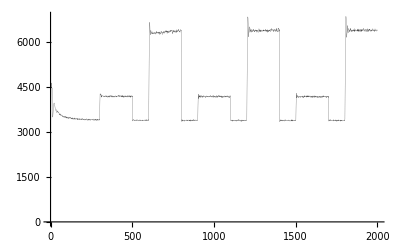

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2031.38, 3822.78, 5229.86, 6271.02, 6906.23, 7165.18, 7221.32, 7189.07, 7096.01, 6963.13, 6875.4, 6794.54, 6494.58, « 25 », 4400.69, 4417.82, 4374., 4351.31, 4287.17, 4293.34, 4299.17, 4304.49, 4245.21, 4221.33, 4145.61, 4082.56, « 1950 »}, « 3 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.38,3822.78,5229.86,6271.02,6906.23,7165.18,7221.32,7189.07,7096.01,6963.13,6875.4,6794.54,6494.58,6181.43,5947.16,5627.72,5161.52,4810.98,4589.84,4471.47,4329.78,4343.62,4330.23,4297.4,4266.21,4278.57,4322.97,4272.52,4378.69,4371.23,4351.73,4403.55,4448.23,4407.11,4394.52,4418.79,4482.98,4460.,4400.69,4417.82,4374.,4351.31,4287.17,4293.34,4299.17,4304.49,4245.21,4221.33,4145.61,4082.56,4101.25,4059.05,4035.9,3958.28,3952.18,3935.02,3913.46,3872.79,3822.65,3831.58,3802.73,3812.46,3777.2,3784.77,3760.3,3759.32,3728.02,3756.95,3720.4,3693.1,3695.81,3668.,3642.34,3645.54,3633.23,3630.49,3622.9,3570.87,3605.53,3591.64,3571.52,3565.9,3566.13,3554.23,3594.18,3579.75,3597.59,3544.71,3534.67,3563.,3530.75,3512.35,3561.24,3507.05,3513.74,3539.25,3526.01,3531.64,3534.36,3512.73,3547.06,3547.55,3502.56,3524.48,3512.52,3537.92,3490.99,3507.69,3517.14,3487.65,3457.64,3488.99,3526.67,3490.61,3504.56,3479.21,3498.11,3516.49,3493.27,3517.25,3492.92,3505.72,3468.83,3479.67,3513.59,3461.15,3475.16,3501.64,3499.81,3482.9,3517.76,3496.44,3498.56,3489.46,3477.03,3472.97,3477.13,3506.06,3511.83,3507.17,3498.62,3476.63,3469.92,3479.47,3487.57,3486.04,3483.2,3508.17,3493.24,3495.15,3470.86,3461.,3466.05,3473.94,3500.28,3510.61,3493.05,3485.17,3464.32,3491.53,3487.25,3492.12,3502.54,3486.03,3489.16,3481.07,3494.24,3497.22,3474.23,3460.3,3487.2,3474.82,3506.8,3461.32,3470.58,3466.84,3477.89,3484.91,3483.85,3471.2,3445.16,3462.17,3494.6,3459.71,3506.9,3505.99,3507.43,3453.64,3509.24,3467.66,3444.15,3452.53,3450.97,3462.95,3446.88,3462.46,3450.82,3466.68,3478.16,3465.07,3473.85,3478.51,3492.34,3471.9,3486.36,3497.43,3421.5,3449.18,3471.55,3457.01,3483.51,3442.39,3435.14,3431.11,3481.35,3488.13,3466.97,3434.65,3441.94,3439.46,3480.38,3463.43,3453.63,3442.87,3472.6,3448.27,3448.04,3472.8,3460.49,3459.73,3446.77,3462.51,3463.39,3432.67,3450.76,3454.36,3473.93,3485.19,3452.79,3476.67,3501.9,3457.86,3440.85,3491.93,3488.43,3463.32,3443.09,3475.57,3445.24,3471.48,3446.46,3448.32,3464.65,3459.49,3460.47,3482.07,3453.32,3468.81,3435.68,3514.59,3448.7,3459.85,3475.86,3469.19,3448.79,3475.3,3436.82,3475.26,3437.9,3446.7,3460.07,3439.8,3457.57,3453.25,3455.6,3455.53,3456.12,3441.16,3449.73,3465.76,3486.93,3464.45,3456.87,3441.27,3456.31,3473.5,3468.22,3464.79,3454.76,3472.3,3441.4,3480.25,3473.27,3455.79,3432.6,3437.36,3476.79,3483.59,3473.45,3462.12,3459.35,3445.92,3417.9,3444.9,3492.49,3426.62,3432.66,3473.84,3430.03,3448.08,3439.14,3445.36,3443.8,3433.44,3434.47,3432.74,3470.09,3461.49,3481.,3458.64,3462.55,3488.56,3460.53,3457.85,3468.87,3449.64,3480.15,3445.38,3467.82,3445.09,3436.95,3460.35,3458.02,3459.59,3474.12,3467.57,3426.32,3447.54,3449.16,3456.26,3461.21,3423.92,3469.5,3477.03,3448.06,3433.73,3445.87,3450.17,3450.47,3429.64,3465.,3446.73,3455.71,3443.14,3466.34,3437.84,3456.91,3464.82,3406.87,3443.05,3440.19,3442.95,3450.58,3445.77,3451.03,3468.18,3455.74,3456.5,3477.16,3440.81,3442.26,3479.86,3448.13,3441.52,3452.8,3429.69,3439.29,3464.82,3449.78,3477.03,3453.92,3437.88,3439.49,3428.42,3460.63,3499.12,3430.15,3436.63,3446.81,3462.37,3462.73,3439.02,3484.42,3453.24,3428.91,3455.92,3436.41,3431.21,3460.78,3416.23,3454.55,3460.33,3456.22,3454.62,3472.01,3424.71,3458.33,3457.92,3448.72,3439.65,3465.53,3460.58,3449.41,3443.59,3462.3,3444.62,3471.95,3461.51,3466.27,3472.87,3454.63,3456.03,3400.47,3451.9,3429.82,3419.86,3450.69,3432.88,3432.07,3467.92,3475.57,3431.14,3444.42,3441.63,3470.77,3440.83,3459.22,3437.23,3411.86,3452.61,3428.66,3435.46,3442.96,3415.88,3443.95,3455.31,3462.53,3469.78,3453.22,3429.73,3469.59,3442.85,3441.75,3466.49,3476.23,3451.1,3437.77,3443.96,3460.82,3424.03,3405.27,3427.98,3452.9,3450.83,3443.99,3444.09,3440.05,3457.76,3465.06,3449.81,3441.78,3468.73,3482.42,3448.83,3432.42,3461.51,3462.32,3473.99,3437.07,3441.32,3423.11,3424.64,3429.23,3440.42,3444.95,3452.4,3447.36,3421.62,3437.44,3461.48,3459.16,3439.5,3466.52,3439.,3461.25,3457.99,3464.79,3458.99,3433.09,3446.23,3459.06,3456.93,3430.96,3460.74,3482.95,3457.19,3434.93,3439.67,3456.9,3472.3,3441.1,3434.19,3460.63,3477.75,3462.16,3461.51,3444.09,3432.35,3412.01,3436.34,3457.46,3458.25,3460.88,3456.53,3430.04,3408.74,3458.24,3462.46,3464.43,3456.62,3420.31,3451.26,3445.79,3448.64,3408.19,3440.84,3454.99,3453.86,3415.18,3440.1,3444.66,3443.41,3435.32,3434.97,3459.29,3439.21,3450.07,3429.72,3428.96,3426.36,3431.15,3413.24,3438.33,3450.8,3455.02,3419.91,3473.02,3471.8,3453.45,3431.69,3457.17,3442.96,3458.82,3458.71,3402.41,3459.91,3450.33,3434.33,3430.41,3458.58,3439.28,3423.84,3422.08,3437.28,3452.82,3460.15,3449.9,3450.7,3463.19,3441.3,3474.83,3451.75,3446.83,3431.59,3455.11,3451.68,3431.8,3427.11,3437.81,3477.84,3436.35,3440.89,3423.47,3473.09,3448.86,3437.9,3450.17,3427.32,3446.38,3463.67,3453.33,3441.19,3438.56,3415.64,3424.07,3454.13,3417.36,3471.98,3477.55,3444.7,3419.79,3455.36,3434.99,3421.53,3462.05,3432.75,3445.49,3451.3,3449.57,3438.44,3432.25,3433.66,3434.26,3438.03,3456.09,3457.78,3476.39,3425.7,3461.62,3443.59,3449.1,3446.61,3450.85,3434.83,3399.87,3424.98,3431.25,3453.92,3441.66,3425.16,3444.7,3454.54,3427.98,3440.72,3458.49,3459.18,3429.6,3418.66,3449.16,3439.54,3444.38,3440.71,3446.44,3478.49,3421.72,3438.4,3466.26,3450.55,3438.67,3438.59,3431.32,3449.09,3437.87,3454.4,3468.13,3415.64,3461.61,3464.98,3449.34,3434.42,3451.23,3458.01,3446.89,3448.45,3456.73,3429.03,3465.14,3454.88,3423.22,3442.8,3454.79,3452.74,3420.77,3408.84,3443.21,3455.58,3449.03,3457.02,3433.16,3466.55,3464.62,3439.26,3442.9,3447.65,3434.89,3444.85,3465.37,3462.61,3452.8,3417.41,3429.7,3416.93,3456.47,3451.74,3450.02,3451.12,3454.59,3430.87,3454.94,3458.4,3459.29,3428.58,3437.19,3455.13,3451.26,3432.41,3438.85,3442.43,3450.38,3471.08,3456.9,3482.56,3482.08,3428.18,3454.59,3458.,3433.26,3445.23,3418.04,3439.08,3445.56,3472.47,3443.81,3429.82,3429.85,3448.48,3453.95,3450.47,3448.44,3457.98,3449.18,3438.45,3451.37,3461.47,3425.02,3442.14,3482.12,3445.43,3435.42,3471.41,3462.59,3456.2,3434.13,3464.73,3455.67,3449.21,3419.77,3459.6,3462.93,3434.77,3459.52,3423.85,3442.7,3464.14,3422.25,3459.79,3463.7,3429.65,3446.36,3446.8,3451.41,3475.76,3437.79,3450.16,3422.29,3456.69,3476.5,3470.85,3430.13,3441.51,3469.92,3443.84,3455.4,3447.37,3432.34,3469.39,3465.2,3435.62,3414.86,3423.17,3434.78,3443.71,3447.29,3417.99,3448.21,3440.13,3431.91,3445.04,3439.71,3449.36,3455.4,3434.,3442.3,3461.57,3429.7,3448.77,3452.46,3429.93,3435.9,3436.21,3471.17,3461.91,3453.97,3428.62,3411.9,3433.31,3478.18,3450.2,3441.57,3433.29,3459.99,3423.51,3413.29,3459.34,3440.97,3451.,3452.6,3444.3,3450.46,3441.01,3439.89,3442.37,3443.26,3422.84,3463.,3463.73,3418.92,3448.85,3412.37,3451.22,3460.33,3439.92,3428.99,3404.83,3411.49,3436.57,3450.51,3428.56,3447.93,3443.44,3461.01,3443.19,3412.66,3440.26,3420.34,3431.82,3433.58,3445.6,3457.24,3434.94,3437.5,3478.47,3424.85,3444.38,3423.32,3449.74,3438.08,3459.28,3429.65,3432.63,3446.21,3456.97,3460.87,3455.84,3449.48,3433.92,3460.06,3453.1,3423.8,3469.52,3463.98,3458.,3465.74,3434.12,3429.37,3457.97,3459.67,3473.78,3460.39,3448.45,3413.87,3442.85,3443.44,3471.94,3445.94,3420.28,3430.85,3439.48,3443.9,3413.25,3432.33,3443.26,3429.,3448.44,3443.86,3458.29,3451.05,3453.79,3469.16,3460.49,3450.86,3445.16,3419.25,3445.22,3424.99,3425.98,3441.07,3440.62,3453.74,3461.49,3434.52,3453.27,3453.79,3430.96,3435.8,3447.43,3448.16,3436.47,3476.19,3463.51,3462.86,3461.23,3433.75,3433.17,3446.29,3434.94,3436.77,3462.21,3442.09,3431.04,3434.14,3460.14,3453.19,3406.51,3429.27,3469.14,3466.01,3419.27,3437.48,3456.25,3438.14,3435.9,3426.65,3466.73,3459.07,3434.06,3436.12,3455.52,3471.47,3428.73,3443.62,3460.79,3441.21,3447.04,3435.32,3433.09,3469.01,3432.2,3441.98,3437.2,3426.81,3459.45,3432.18,3448.68,3425.37,3441.28,3468.84,3456.7,3451.1,3441.67,3437.53,3448.73,3425.41,3422.39,3432.38,3428.03,3445.18,3429.47,3425.74,3464.16,3438.48,3421.82,3457.63,3433.56,3471.86,3422.37,3423.39,3448.71,3446.28,3426.83,3433.08,3491.36,3421.52,3458.54,3478.16,3438.91,3456.03,3433.11,3447.89,3454.02,3455.09,3438.61,3432.38,3441.33,3432.87,3453.62,3465.55,3410.83,3443.19,3443.05,3455.25,3455.7,3443.18,3438.9,3428.86,3434.91,3445.75,3449.56,3429.15,3455.44,3425.29,3446.15,3446.6,3446.84,3427.94,3454.54,3431.18,3421.56,3460.82,3448.78,3403.09,3459.41,3420.19,3448.46,3449.3,3413.76,3447.72,3439.43,3439.58,3436.74,3442.81,3455.22,3439.91,3454.71,3481.09,3419.27,3427.18,3439.79,3438.49,3436.11,3427.48,3463.08,3436.88,3449.77,3412.73,3447.9,3451.14,3413.52,3433.64,3449.46,3455.71,3421.44,3433.25,3451.71,3436.81,3427.74,3422.82,3454.7,3462.79,3427.2,3455.79,3417.88,3445.11,3446.43,3455.89,3428.4,3492.05,3438.59,3445.62,3428.28,3438.33,3444.29,3436.,3446.55,3453.61,3440.7,3426.39,3427.38,3429.39,3438.45,3455.44,3424.,3426.23,3427.68,3462.64,3430.5,3456.62,3421.89,3451.63,3460.94,3434.69,3444.17,3476.82,3437.37,3470.44,3423.34,3438.85,3430.91,3445.03,3411.72,3450.6,3464.59,3410.51,3470.43,3437.12,3431.48,3441.86,3437.69,3442.55,3446.88,3443.89,3429.32,3438.26,3430.62,3461.52,3432.37,3451.52,3464.48,3450.28,3452.57,3464.61,3456.,3435.41,3449.05,3449.79,3449.59,3452.63,3466.44,3446.54,3438.6,3441.55,3424.65,3430.66,3425.66,3453.43,3419.01,3433.53,3432.87,3453.25,3446.06,3442.09,3451.62,3452.57,3424.7,3456.02,3442.65,3417.54,3468.43,3436.35,3428.58,3429.43,3456.24,3435.08,3439.3,3446.49,3441.28,3434.27,3424.27,3439.14,3415.79,3430.52,3463.79,3440.88,3422.02,3460.24,3437.75,3422.74,3443.64,3441.14,3427.5,3448.37,3464.21,3433.13,3471.52,3483.3,3451.38,3475.92,3422.51,3432.67,3460.26,3435.13,3453.11,3431.86,3470.39,3445.18,3443.8,3434.95,3467.26,3449.31,3446.21,3446.1,3448.96,3483.1,3423.34,3418.97,3433.26,3438.11,3473.54,3447.62,3436.49,3451.03,3450.45,3465.9,3422.71,3419.31,3441.85,3441.54,3438.83,3430.01,3405.75,3454.73,3457.08,3443.91,3446.15,3437.48,3453.22,3456.12,3452.45,3464.24,3421.29,3411.15,3452.54,3438.94,3458.23,3415.81,3423.42,3435.86,3433.25,3447.94,3455.51,3438.01,3457.44,3430.76,3434.33,3446.15,3424.62,3440.7,3418.41,3444.83,3457.58,3476.5,3464.34,3444.23,3438.05,3440.76,3430.02,3455.09,3446.75,3413.26,3447.83,3453.11,3440.8,3444.31,3458.14,3424.07,3456.78,3435.85,3440.74,3420.69,3419.08,3451.77,3435.18,3421.,3408.63,3442.16,3414.53,3437.79,3444.56,3431.85,3428.92,3437.71,3446.77,3423.51,3440.84,3419.15,3447.66,3417.88,3402.95,3457.2,3461.58,3442.32,3431.62,3432.88,3445.83,3441.34,3412.91,3451.26,3448.94,3454.54,3402.31,3423.15,3431.63,3422.21,3425.17,3459.48,3471.17,3452.99,3434.09,3419.98,3478.39,3468.43,3441.07,3462.48,3442.47,3446.93,3442.45,3458.54,3437.53,3423.57,3416.16,3452.55,3451.09,3446.77,3463.89,3477.07,3456.47,3465.11,3440.02,3442.24,3439.71,3455.14,3403.44,3414.61,3436.78,3484.11,3465.11,3429.1,3455.47,3445.66,3418.64,3399.2,3430.44,3469.35,3434.19,3440.69,3478.28,3427.94,3418.48,3440.78,3440.53,3428.62,3440.49,3432.53,3449.87,3431.65,3438.75,3436.72,3427.84,3432.91,3441.69,3467.04,3448.68,3473.7,3462.41,3451.31,3446.07,3460.63,3451.22,3464.09,3476.05,3432.96,3441.19,3422.64,3484.19,3455.1,3455.84,3454.43,3454.23,3417.24,3441.12,3467.88,3430.27,3424.97,3487.81,3462.48,3471.74,3419.49,3430.89,3435.88,3439.72,3422.82,3445.95,3456.11,3421.9,3440.93,3432.25,3458.88,3435.24,3446.89,3426.01,3396.81,3441.73,3455.11,3429.95,3450.37,3472.58,3430.54,3425.68,3423.18,3458.93,3397.23,3438.7,3465.04,3457.7,3440.54,3460.7,3452.54,3422.03,3446.98,3424.29,3431.38,3426.63,3446.34,3488.73,3482.21,3400.92,3432.79,3445.87,3431.33,3445.96,3445.59,3426.,3447.07,3472.15,3432.19,3460.28,3451.99,3422.08,3442.1,3439.12,3439.89,3433.33,3434.31,3450.22,3475.09,3466.28,3448.74,3437.63,3474.18,3444.23,3459.63,3436.18,3440.91,3426.55,3404.32,3431.52,3452.57,3440.19,3479.29,3435.94,3440.36,3462.79,3458.59,3456.66,3443.25,3458.51,3422.47,3417.48,3405.47,3429.44,3432.01,3475.93,3452.86,3407.66,3478.51,3471.95,3441.39,3453.95,3438.22,3456.19,3451.7,3425.79,3457.23,3440.52,3440.91,3449.79,3473.77,3449.15,3437.28,3427.08,3430.91,3467.53,3438.53,3435.15,3453.69,3429.85,3435.21,3439.15,3444.81,3452.44,3459.42,3436.57,3468.18,3445.15,3438.93,3426.51,3451.02,3460.55,3447.17,3448.28,3432.,3440.22,3439.1,3443.25,3433.05,3433.53,3452.4,3452.31,3451.24,3432.52,3435.25,3452.4,3416.28,3434.74,3448.4,3437.34,3450.23,3433.15,3432.09,3437.81,3421.89,3433.95,3404.99,3427.77,3408.68,3452.34,3432.38,3428.35,3446.03,3445.26,3412.44,3446.35,3402.76,3422.43,3423.69,3452.12,3468.73,3442.38,3418.21,3457.03,3443.27,3461.45,3415.48,3437.82,3433.77,3418.14,3450.11,3441.99,3451.98,3432.11,3437.4,3434.44,3405.73,3416.52,3438.98,3445.48,3398.27,3423.09,3478.35,3460.92,3412.8,3424.32,3432.87,3445.89,3453.43,3474.65,3420.32,3459.79,3429.31,3460.07,3479.27,3443.2,3448.26,3402.1,3456.35,3445.32,3422.23,3424.81,3430.02,3422.5,3413.06,3443.94,3451.31,3426.77,3441.1,3432.75,3434.14,3420.61,3410.69,3444.21,3457.58,3436.57,3429.14,3451.14,3411.43,3427.12,3446.87,3431.1,3425.72,3436.21,3424.19,3421.43,3449.41,3432.4,3454.27,3442.95,3437.63,3463.83,3423.34,3424.3,3449.69,3459.23,3438.59,3414.81,3447.51,3429.99,3449.95,3429.45,3440.56,3451.7,3423.78,3437.39,3436.7,3447.84,3444.29,3445.75,3448.56,3442.51,3465.64,3451.08,3409.2,3423.,3431.42,3443.15,3444.81,3442.,3449.82,3454.3,3473.96,3460.74,3427.55,3408.3,3424.96,3430.99,3424.62,3447.42,3458.11,3443.06,3437.84,3419.2,3453.27,3438.89,3456.68,3438.32,3431.48,3425.86,3420.71,3483.57,3464.82,3429.73,3421.17,3468.64,3451.97,3451.57,3442.03,3454.22,3427.83,3438.37,3462.32,3401.68,3425.88,3460.63,3452.59,3427.32,3441.41,3435.41,3416.55,3430.16,3433.77,3410.28,3422.75,3445.22,3449.77,3448.9,3440.03,3444.58,3424.56,3418.49,3426.03,3441.97,3435.08,3441.37,3449.91,3452.01,3410.02,3429.95,3443.1,3442.56,3424.22,3450.72,3434.14,3416.03,3473.03,3408.42,3466.27,3432.63,3444.63,3445.2,3461.08,3429.24,3445.18,3421.37,3440.06,3418.36,3433.66,3433.38,3432.01,3457.12,3419.91,3439.44,3424.75,3460.8,3434.35,3451.47,3432.58,3438.27,3462.41,3438.74,3432.93,3407.87,3456.45,3452.62,3419.82,3446.28,3453.63,3437.81,3443.33,3465.31,3437.28,3441.51,3403.86,3466.8,3443.9,3429.14,3427.3,3433.47,3463.44,3446.,3426.86,3431.44,3448.28,3456.61,3477.7,3444.52,3470.39,3426.71,3407.9,3449.19,3426.01,3450.77,3443.18,3429.01,3435.25,3443.07,3431.53,3433.03,3441.35,3470.99,3442.14,3424.44,3441.16,3413.81,3430.46,3424.66,3452.42,3454.7,3425.,3459.86,3444.08,3469.28,3444.48,3448.47,3465.65,3444.26,3453.78,3443.82,3405.68,3440.89,3449.26,3452.94,3465.92,3470.3,3422.6,3441.03,3444.28,3462.81,3438.36,3409.8,3449.83,3430.39,3442.93,3440.63,3458.52,3427.05,3402.94,3425.14,3438.91,3429.47,3447.31,3443.39,3435.38,3492.05,3431.74,3439.57,3441.81,3442.64,3446.79,3413.47,3393.82,3432.67,3440.61,3439.91,3435.49,3427.59,3427.25,3474.06,3437.24,3455.89,3444.27,3446.29,3458.54,3412.66,3444.92,3434.,3418.99,3440.17,3445.85,3453.16,3394.28,3442.4,3461.92,3447.79,3436.53,3429.97,3464.21,3424.76,3430.43,3464.72,3435.33,3431.66,3456.69,3410.77,3455.62,3453.13,3429.62,3415.9,3445.53,3445.03,3471.89,3437.74,3408.25,3465.56,3458.71,3443.9,3417.98,3415.95,3438.68,3440.,3446.33,3428.78,3438.24,3425.57,3456.03,3434.22,3435.85,3440.68,3441.41,3483.45,3442.1,3456.88,3440.88,3450.25,3434.32,3424.63,3434.43,3451.12,3434.93,3438.4,3430.63,3435.78,3460.62,3443.61,3464.76,3447.23,3459.36,3433.71,3451.62,3420.63,3417.89,3430.17,3457.15,3432.38,3427.62,3459.04,3439.85,3414.01,3448.41,3432.18,3422.51,3432.19,3464.71,3469.12,3399.93,3414.98,3447.57,3444.15,3418.24,3455.85,3436.51,3461.89,3423.32,3422.11,3451.28,3478.41,3442.99,3452.94,3466.45,3436.03,3457.64,3465.67,3428.38,3416.54,3419.65,3435.44,3419.95,3453.22,3469.64,3441.79,3440.33,3433.38,3440.3,3439.77,3426.84,3423.56,3452.37,3427.65,3432.76,3430.32,3442.29,3461.58,3464.78,3427.97,3425.42,3445.99,3428.71,3449.13,3453.52,3404.05,3436.07,3443.26,3413.51,3441.76,3444.99,3431.01,3421.46,3439.36,3418.88,3450.26,3434.3,3430.5,3426.97,3445.16,3447.82,3426.69,3445.68,3424.53,3459.78,3450.5,3447.17,3504.47},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.66, 3198.24, 3562.75, 3455.01, 3398.69, 3402.76, 3390.25, 3402.44, 3416., 3382.91, 3376.54, 3403.71, 3382.89, « 25 », 3401.15, 3417.57, 3403.79, 3409.6, 3406.93, 3408.16, 3368.89, 3377.84, 3387.54, 3392.45, 3401.77, 3419.46, « 1950 »}, « 3 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.66,3198.24,3562.75,3455.01,3398.69,3402.76,3390.25,3402.44,3416.,3382.91,3376.54,3403.71,3382.89,3364.41,3404.2,3384.74,3385.59,3415.8,3420.42,3391.97,3443.9,3422.48,3389.69,3406.52,3374.79,3434.09,3367.62,3383.22,3385.,3396.7,3390.87,3383.47,3399.01,3421.2,3408.9,3408.13,3392.13,3389.11,3401.15,3417.57,3403.79,3409.6,3406.93,3408.16,3368.89,3377.84,3387.54,3392.45,3401.77,3419.46,3388.02,3394.94,3363.24,3393.2,3398.62,3403.4,3428.21,3416.42,3380.67,3385.43,3400.59,3387.47,3394.57,3374.33,3362.06,3390.97,3416.79,3358.96,3398.05,3398.39,3397.22,3408.38,3389.68,3400.98,3398.52,3377.94,3418.71,3386.12,3396.87,3393.88,3415.44,3398.79,3400.59,3396.98,3427.82,3395.51,3379.56,3410.65,3400.11,3396.37,3370.99,3379.52,3377.41,3377.11,3380.61,3393.67,3405.75,3413.57,3388.37,3384.88,3386.35,3417.12,3384.08,3390.71,3415.48,3381.15,3387.91,3397.85,3381.59,3381.04,3410.45,3409.69,3378.53,3374.61,3370.,3394.05,3397.05,3396.19,3409.83,3421.25,3390.11,3404.56,3396.18,3386.69,3396.84,3423.2,3387.95,3375.07,3423.59,3378.22,3376.58,3374.08,3395.41,3418.01,3401.1,3422.26,3402.6,3393.74,3393.34,3400.17,3398.86,3394.15,3376.43,3407.37,3377.31,3384.91,3396.77,3393.31,3372.14,3384.75,3384.09,3380.8,3395.06,3378.72,3416.68,3405.97,3424.95,3399.58,3393.12,3388.77,3384.49,3411.25,3413.73,3389.77,3401.28,3420.48,3417.18,3375.87,3397.82,3400.67,3389.59,3390.47,3411.52,3382.47,3395.16,3391.63,3390.16,3389.94,3367.88,3397.51,3389.76,3400.49,3417.1,3383.14,3370.23,3397.8,3400.79,3398.16,3393.94,3412.11,3415.48,3416.05,3390.92,3402.94,3397.08,3390.87,3422.64,3400.05,3393.07,3406.49,3408.75,3390.93,3378.68,3403.42,3404.21,3420.4,3412.04,3407.29,3373.08,3377.88,3398.36,3394.86,3381.74,3386.77,3392.05,3376.57,3383.57,3377.35,3370.79,3410.95,3422.07,3407.94,3401.31,3426.47,3391.62,3379.37,3410.38,3396.91,3403.71,3406.14,3361.41,3384.48,3387.16,3404.97,3389.74,3419.1,3410.55,3397.45,3394.39,3393.59,3375.82,3402.92,3413.88,3412.21,3382.97,3398.58,3404.26,3393.9,3368.23,3392.05,3376.68,3397.58,3402.76,3372.29,3396.53,3369.53,3379.19,3424.9,3402.32,3372.87,3362.72,3401.06,3386.69,3410.93,3407.86,3394.39,3418.56,3420.2,3408.93,3385.99,3392.22,3398.78,3396.6,3376.52,3396.8,3398.51,3378.25,3383.73,3397.44,3401.2,3402.28,3398.72,3387.67,3408.44,3392.25,3402.69,3396.24,3394.54,3369.38,3391.23,3399.07,3410.27,3382.4,3396.24,3408.48,3393.04,3411.58,3375.85,3365.24,3366.78,3393.66,3399.81,3389.37,3381.09,3369.78,3379.43,3397.79,3407.38,3415.78,3419.08,3403.65,3407.87,3418.22,3373.01,3384.57,3398.67,3405.34,3400.44,3409.87,3393.62,3382.4,3396.6,3403.12,3392.82,3415.23,3380.42,3366.84,3403.92,3423.12,3404.78,3425.09,3397.37,3385.81,3400.68,3412.86,3412.06,3385.94,3403.89,3397.07,3379.38,3383.7,3420.8,3401.27,3396.74,3382.17,3387.71,3375.62,3404.22,3410.56,3381.11,3377.6,3396.07,3391.08,3408.4,3422.97,3387.46,3370.35,3396.88,3382.46,3388.97,3401.13,3387.83,3398.08,3400.06,3416.11,3400.47,3410.56,3385.46,3420.6,3406.84,3392.4,3382.91,3393.49,3407.46,3416.23,3392.4,3408.48,3402.75,3391.27,3410.89,3360.43,3379.37,3413.29,3394.34,3371.6,3409.28,3391.79,3406.78,3380.97,3420.61,3407.32,3386.5,3388.3,3402.1,3394.85,3391.93,3387.47,3380.76,3385.49,3399.78,3383.14,3398.12,3412.56,3385.75,3403.48,3395.89,3400.5,3385.59,3380.24,3394.49,3393.55,3417.45,3401.17,3364.52,3398.63,3386.93,3391.29,3377.8,3401.56,3398.51,3372.92,3404.34,3379.78,3393.66,3403.17,3400.5,3391.86,3391.9,3375.03,3386.,3392.45,3356.22,3393.58,3400.12,3380.49,3395.9,3391.98,3385.33,3387.2,3386.57,3406.53,3385.66,3385.61,3360.95,3396.95,3405.81,3396.57,3386.33,3392.34,3387.79,3390.68,3425.28,3388.3,3388.89,3366.2,3406.74,3420.89,3403.95,3403.25,3374.01,3374.84,3380.3,3401.15,3371.87,3402.91,3419.8,3383.68,3394.11,3395.23,3393.88,3406.45,3411.29,3393.99,3383.52,3398.52,3398.77,3383.64,3380.02,3420.23,3381.64,3399.83,3418.9,3405.5,3398.68,3375.93,3405.1,3389.9,3368.66,3405.74,3397.82,3402.04,3391.33,3391.28,3386.01,3395.37,3410.25,3403.08,3370.84,3358.98,3419.02,3391.36,3393.16,3401.99,3387.68,3385.16,3391.62,3412.12,3397.56,3387.47,3391.16,3383.23,3383.7,3395.41,3400.11,3407.17,3403.7,3399.33,3396.86,3423.38,3422.56,3410.43,3420.63,3392.45,3389.23,3397.68,3410.72,3389.82,3400.44,3381.57,3387.01,3407.4,3407.18,3401.05,3387.75,3407.96,3404.28,3398.78,3400.06,3397.13,3399.28,3382.67,3377.12,3403.69,3437.22,3402.93,3398.01,3399.58,3410.65,3398.92,3416.19,3411.51,3388.97,3392.03,3381.55,3410.21,3397.16,3386.25,3378.71,3390.8,3369.48,3386.5,3408.49,3397.33,3410.37,3370.98,3376.35,3377.36,3413.,3438.84,3384.31,3390.49,3376.92,3398.61,3376.36,3416.32,3408.11,3414.52,3404.21,3379.2,3396.9,3380.11,3360.52,3406.24,3382.33,3394.08,3386.83,3378.69,3409.97,3398.54,3420.99,3378.23,3390.82,3381.54,3384.17,3402.77,3384.63,3391.39,3395.36,3412.11,3394.,3388.39,3376.66,3413.3,3404.95,3403.81,3399.48,3414.64,3378.39,3402.66,3382.06,3405.46,3409.9,3396.04,3409.52,3393.83,3358.63,3370.32,3433.46,3398.98,3390.51,3392.76,3421.24,3393.12,3424.07,3386.78,3397.79,3411.28,3413.27,3406.98,3411.38,3394.99,3386.09,3416.26,3420.69,3369.06,3414.97,3388.52,3396.96,3406.39,3394.92,3399.14,3401.15,3404.46,3392.62,3378.69,3378.59,3398.28,3405.57,3406.52,3404.13,3392.55,3403.99,3394.52,3412.66,3398.75,3403.95,3409.52,3418.02,3396.06,3409.71,3425.08,3390.36,3417.08,3386.58,3390.91,3386.48,3409.31,3397.37,3423.27,3403.13,3390.79,3395.9,3398.26,3400.27,3416.12,3384.64,3374.42,3385.88,3397.22,3403.81,3402.01,3396.63,3395.43,3393.85,3399.39,3391.28,3383.88,3411.39,3402.28,3394.6,3393.31,3413.73,3404.59,3386.02,3389.99,3377.51,3379.95,3374.66,3383.2,3384.85,3403.13,3392.01,3410.18,3431.93,3381.25,3373.36,3391.89,3387.65,3391.47,3396.8,3376.53,3373.23,3374.36,3413.28,3405.19,3368.18,3366.29,3402.85,3407.57,3428.91,3397.43,3393.04,3402.93,3426.3,3409.39,3397.61,3383.52,3383.5,3373.1,3389.33,3417.75,3413.28,3402.01,3389.23,3405.99,3404.98,3372.,3388.51,3377.06,3379.32,3408.28,3383.87,3377.9,3385.21,3370.65,3380.43,3381.62,3397.68,3388.01,3401.67,3364.45,3386.88,3385.53,3380.33,3387.93,3393.89,3382.59,3407.09,3400.72,3401.78,3396.29,3410.19,3394.04,3376.2,3386.82,3394.07,3406.72,3404.29,3416.89,3388.72,3404.55,3395.71,3415.1,3368.79,3379.02,3394.48,3388.71,3416.41,3405.33,3401.37,3361.65,3410.54,3377.51,3379.78,3389.21,3405.92,3404.31,3386.6,3390.32,3387.55,3382.29,3395.03,3426.44,3417.76,3390.15,3403.05,3404.36,3377.12,3386.15,3407.28,3419.55,3395.21,3396.77,3386.76,3423.34,3401.99,3403.88,3401.25,3389.28,3384.17,3407.74,3378.99,3405.79,3419.45,3400.7,3382.93,3404.68,3401.99,3377.33,3414.16,3402.14,3394.08,3379.79,3413.44,3409.96,3380.,3401.51,3409.07,3382.06,3400.97,3418.32,3403.13,3392.28,3406.2,3430.45,3422.43,3415.2,3397.51,3392.62,3403.35,3424.29,3402.65,3404.03,3380.05,3406.31,3421.12,3371.09,3425.43,3410.63,3375.9,3382.91,3396.12,3380.95,3381.12,3407.48,3405.3,3411.39,3400.2,3414.9,3399.52,3409.78,3377.46,3396.62,3405.1,3386.04,3461.61,3417.42,3386.98,3389.09,3414.7,3403.17,3396.73,3391.6,3404.32,3402.82,3395.44,3384.86,3381.71,3420.54,3414.9,3387.48,3425.33,3406.68,3396.8,3379.9,3357.79,3395.79,3397.51,3406.91,3399.8,3402.32,3394.59,3385.33,3397.24,3422.61,3393.63,3389.53,3408.49,3397.08,3388.14,3399.4,3408.64,3399.85,3393.04,3405.75,3384.61,3395.76,3378.51,3404.23,3395.42,3422.21,3368.82,3410.12,3393.01,3385.84,3414.78,3407.2,3411.56,3383.34,3377.76,3406.69,3409.8,3389.15,3393.09,3395.1,3427.5,3413.23,3386.49,3408.86,3402.34,3411.57,3372.86,3363.15,3376.65,3413.82,3405.77,3378.86,3387.81,3390.81,3390.2,3399.41,3392.69,3421.2,3390.09,3404.03,3402.85,3380.92,3427.95,3393.86,3412.23,3409.33,3406.,3384.55,3411.18,3390.62,3405.78,3395.57,3398.5,3391.8,3382.26,3385.88,3398.39,3410.03,3407.98,3402.28,3378.94,3390.38,3390.84,3394.94,3406.38,3376.96,3409.09,3435.,3425.53,3387.42,3405.7,3405.17,3406.21,3386.66,3383.3,3379.94,3378.19,3398.52,3376.55,3417.39,3406.31,3391.71,3382.55,3430.92,3378.35,3389.11,3384.81,3410.83,3407.85,3406.63,3413.09,3402.55,3408.33,3393.56,3386.45,3397.39,3387.59,3391.06,3408.18,3413.6,3420.13,3399.3,3403.3,3389.25,3422.74,3415.66,3380.41,3416.73,3383.4,3428.7,3416.1,3405.61,3405.8,3373.16,3379.65,3385.21,3386.5,3413.98,3395.47,3401.6,3373.89,3361.93,3375.95,3389.92,3365.64,3347.93,3368.91,3399.14,3395.43,3383.7,3384.71,3387.96,3408.33,3411.67,3382.49,3367.65,3406.52,3410.41,3386.81,3401.98,3419.08,3393.17,3413.41,3416.42,3404.22,3393.48,3417.98,3408.86,3416.69,3411.48,3428.22,3408.91,3382.55,3379.32,3399.34,3385.05,3396.32,3376.78,3390.96,3388.62,3388.05,3393.6,3404.06,3353.17,3402.98,3396.15,3386.77,3378.48,3403.4,3391.3,3399.39,3382.81,3411.15,3387.08,3412.88,3390.64,3387.12,3402.55,3385.77,3408.92,3381.59,3389.45,3404.59,3395.85,3384.24,3390.9,3402.48,3372.07,3388.98,3392.49,3406.1,3391.37,3376.,3409.45,3383.77,3407.77,3379.17,3385.14,3394.37,3409.53,3384.83,3393.82,3383.28,3398.54,3372.23,3386.29,3411.99,3428.33,3410.18,3398.77,3422.83,3381.88,3417.83,3411.03,3429.68,3388.29,3397.99,3414.01,3391.44,3402.34,3430.51,3408.82,3398.15,3386.91,3390.31,3370.75,3359.1,3410.33,3389.72,3408.63,3389.15,3388.43,3402.15,3388.73,3386.43,3397.64,3404.06,3387.67,3372.34,3403.6,3412.68,3396.95,3391.79,3407.55,3398.68,3397.85,3387.,3376.71,3394.48,3383.03,3390.06,3397.88,3388.25,3380.13,3393.35,3382.88,3381.44,3387.71,3412.76,3386.84,3395.67,3412.49,3387.93,3373.14,3391.75,3408.98,3342.,3393.49,3408.03,3402.69,3422.15,3414.36,3403.61,3384.48,3393.79,3419.18,3391.85,3390.11,3405.77,3400.12,3397.16,3369.41,3386.51,3391.55,3424.45,3375.14,3406.12,3393.3,3396.87,3401.93,3395.83,3421.3,3403.99,3387.64,3398.72,3416.3,3373.74,3374.65,3413.45,3403.97,3400.77,3390.35,3416.05,3391.4,3397.24,3373.8,3388.88,3412.13,3402.47,3380.07,3387.12,3392.15,3382.18,3375.2,3356.78,3397.39,3384.89,3407.1,3407.53,3379.82,3420.79,3386.28,3418.58,3386.51,3410.77,3407.41,3395.35,3398.47,3379.42,3392.53,3398.09,3417.01,3394.04,3389.89,3389.74,3396.78,3405.52,3403.82,3422.45,3395.56,3378.61,3417.54,3383.82,3402.34,3387.55,3385.42,3396.43,3398.68,3397.,3406.88,3371.41,3383.85,3380.32,3377.74,3390.2,3397.9,3422.09,3389.86,3396.3,3398.56,3389.89,3394.79,3407.58,3379.34,3375.22,3395.48,3404.59,3412.13,3366.53,3415.86,3406.1,3395.27,3419.61,3411.5,3380.38,3359.32,3391.58,3419.85,3410.78,3385.19,3382.76,3412.62,3414.66,3380.69,3409.28,3396.15,3384.09,3388.44,3420.79,3397.91,3391.12,3385.14,3409.04,3396.37,3401.59,3425.,3389.31,3395.39,3379.11,3403.45,3386.49,3381.56,3413.58,3391.43,3392.57,3396.95,3383.48,3406.27,3426.77,3423.27,3395.59,3392.67,3392.01,3378.99,3399.82,3413.3,3418.99,3398.24,3375.2,3406.57,3401.97,3382.2,3399.69,3388.24,3389.56,3404.23,3390.32,3390.64,3404.32,3386.06,3383.52,3432.54,3383.02,3389.16,3417.97,3419.99,3404.54,3387.44,3411.11,3408.04,3421.08,3377.65,3393.59,3391.32,3398.1,3393.89,3387.15,3396.91,3407.48,3410.61,3408.71,3397.16,3372.89,3414.99,3402.12,3392.84,3392.61,3391.09,3368.68,3368.08,3385.85,3415.59,3400.65,3367.01,3407.76,3395.39,3402.73,3406.1,3393.75,3401.23,3396.38,3385.96,3403.7,3404.43,3396.2,3389.62,3395.48,3396.65,3384.7,3418.65,3387.03,3402.36,3395.83,3410.37,3383.87,3395.25,3397.15,3402.71,3400.65,3400.08,3371.85,3396.07,3391.01,3384.92,3402.91,3418.19,3390.89,3418.67,3406.77,3401.74,3413.42,3403.49,3397.99,3407.44,3403.4,3404.39,3402.88,3422.1,3384.34,3400.91,3400.11,3385.66,3400.09,3393.66,3406.06,3402.72,3403.73,3398.48,3393.62,3411.46,3371.45,3380.1,3398.19,3405.74,3381.8,3371.17,3403.8,3396.92,3404.06,3383.73,3384.28,3397.61,3391.9,3387.28,3383.6,3396.35,3400.22,3394.18,3418.82,3380.34,3394.45,3375.55,3388.59,3404.59,3401.43,3379.6,3401.36,3380.85,3397.09,3405.22,3413.63,3372.22,3387.3,3385.74,3427.49,3376.86,3387.31,3409.09,3390.17,3397.88,3390.99,3358.03,3375.73,3429.44,3373.77,3405.65,3402.15,3393.2,3414.16,3415.45,3389.91,3394.5,3383.31,3389.35,3399.69,3401.09,3394.59,3403.86,3404.47,3373.64,3389.62,3394.62,3391.47,3419.85,3400.71,3413.55,3390.1,3405.12,3395.77,3409.84,3403.9,3392.69,3406.08,3406.14,3408.55,3402.26,3394.08,3387.66,3407.73,3384.36,3394.31,3414.1,3402.59,3411.31,3392.75,3377.03,3408.88,3366.27,3403.42,3409.49,3376.46,3400.6,3400.52,3394.65,3404.33,3405.98,3426.38,3392.48,3402.15,3399.82,3392.13,3401.41,3393.41,3412.42,3398.15,3382.46,3419.81,3394.96,3402.77,3415.08,3403.29,3407.95,3401.77,3394.08,3390.08,3385.87,3404.41,3394.89,3375.03,3386.89,3394.64,3381.87,3402.04,3417.43,3404.77,3390.49,3401.19,3389.23,3426.21,3399.01,3393.7,3404.01,3398.73,3423.35,3403.06,3406.05,3397.94,3367.25,3412.38,3408.82,3403.28,3402.74,3403.4,3401.57,3397.81,3408.62,3431.2,3395.45,3390.59,3382.25,3400.03,3380.81,3384.62,3383.64,3413.31,3387.95,3413.12,3402.28,3381.43,3374.56,3425.3,3410.37,3366.22,3401.33,3400.06,3407.42,3382.65,3409.29,3374.3,3385.5,3426.54,3413.78,3373.86,3384.76,3398.98,3419.34,3431.67,3410.73,3391.76,3385.23,3368.34,3402.8,3375.66,3378.95,3391.4,3397.24,3409.51,3391.25,3399.35,3402.91,3383.63,3394.97,3375.37,3391.85,3389.54,3409.27,3395.12,3405.25,3418.32,3408.44,3390.17,3413.35,3388.82,3404.36,3436.53,3439.14,3414.1,3389.88,3422.34,3398.1,3396.53,3385.32,3397.79,3402.21,3397.19,3411.45,3425.53,3398.27,3401.05,3389.77,3414.65,3402.11,3385.21,3392.11,3368.7,3399.31,3385.12,3395.13,3380.1,3363.43,3409.54,3366.67,3385.99,3411.47,3356.22,3393.21,3415.42,3424.53,3403.03,3392.59,3401.63,3399.46,3400.36,3409.,3405.27,3393.99,3385.34,3387.46,3411.88,3402.68,3379.61,3381.01,3407.29,3386.18,3391.81,3373.84,3423.04,3409.33,3375.18,3360.87,3408.33,3381.62,3395.17,3393.69,3408.87,3384.35,3395.42,3408.52,3406.28,3371.,3371.88,3386.82,3404.94,3395.98,3403.01,3422.3,3392.24,3351.08,3410.16,3405.39,3394.7,3406.14,3412.73,3407.31,3370.63,3395.89,3401.82,3385.96,3404.94,3384.53,3414.6,3387.4,3423.91,3402.38,3409.18,3404.13,3416.08,3386.81,3410.48,3404.62,3401.18,3395.63,3411.33,3389.79,3382.19,3397.7,3411.96,3400.72,3394.45,3386.35,3379.25,3410.99,3420.69,3400.42,3381.29,3374.41,3402.35,3429.23,3404.23,3400.89,3383.87,3406.95,3391.48,3385.1,3409.08,3392.19,3411.36,3415.07,3377.76,3383.06,3400.69,3405.28,3377.67,3397.57,3388.22,3406.11,3406.62,3396.15,3407.9,3405.15,3406.13,3397.93,3388.52,3384.34,3377.26,3379.2,3415.89,3418.88,3397.83,3412.78,3406.39,3386.8,3412.73,3390.04,3377.37,3408.95,3387.84,3387.23,3381.09,3416.99,3414.71,3413.35,3396.79,3408.68,3398.65,3395.12,3416.65,3395.84,3392.02,3414.29,3397.26,3411.58,3406.36,3385.17,3380.39,3402.57,3391.65,3391.,3398.77,3388.48,3380.93,3376.14,3425.46,3400.59,3371.52,3376.91,3399.68,3417.12,3385.99,3382.94,3393.53,3398.88,3390.82,3398.05,3419.8,3395.39,3408.81,3418.02,3419.12,3385.78,3397.46,3413.98,3386.49,3404.76,3402.48,3391.76,3392.88,3416.67,3392.29,3417.73,3412.7,3405.68,3390.64,3396.03,3420.37,3391.9,3405.46,3390.48,3394.48,3414.73,3397.13,3374.32,3390.36,3385.33,3402.34,3422.68,3383.36,3408.34,3391.9,3389.17,3392.84,3410.77,3379.,3393.2,3387.41,3389.43,3421.46,3398.74,3399.71,3385.05,3447.42,3400.48,3384.,3392.93,3356.19,3401.98,3406.53,3388.05,3409.13,3399.35,3404.35,3396.56,3413.69,3400.56,3435.42,3409.38,3375.57,3400.49,3402.68,3377.05,3406.49,3392.43,3410.86,3391.23,3389.88,3416.02,3402.79,3376.62,3394.33,3411.78,3366.08,3414.76,3386.,3413.38,3401.58,3371.02,3389.08,3395.99,3386.2,3386.45,3389.35,3405.87,3391.75,3385.54,3399.18,3362.8,3395.2,3419.78,3388.13,3426.06,3402.87,3373.02,3397.51,3404.56,3371.18,3373.97,3379.52,3388.86,3383.67,3398.58,3406.29,3413.34,3399.13,3408.65,3394.09,3390.32,3420.2,3393.92,3392.63,3407.53,3386.28,3385.97,3394.46,3412.29,3397.33,3378.53,3417.16,3389.35,3406.19,3417.24,3404.65,3383.24,3396.15,3387.62,3398.13,3387.25,3398.54,3412.54,3420.08,3390.97,3422.39,3420.84,3432.82,3393.87,3392.02,3390.14,3385.73,3400.67,3396.12,3386.19,3418.49,3396.45,3396.4,3402.34,3389.2,3407.21,3398.98,3408.73,3409.47,3385.74,3384.85,3386.85,3385.94,3409.47,3377.77,3396.22,3385.71,3407.15,3434.73,3381.12,3381.22,3402.82,3413.33,3405.25,3405.06,3396.87,3390.81,3407.2,3385.43,3391.38,3427.64,3402.05,3378.6,3397.67,3402.4},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.78,3821.91,5147.84,6070.83,6519.05,6087.63,5212.89,4734.95,4352.74,4182.14,4076.72,3994.84,3929.1,3921.05,3820.31,3836.38,3804.13,3814.26,3720.85,3720.97,3720.85,3700.72,3678.88,3691.83,3665.53,3687.33,3713.36,3677.3,3678.5,3687.59,3626.22,3648.24,3615.08,3615.19,3630.93,3657.67,3614.65,3623.9,3665.11,3609.49,3579.01,3576.02,3598.88,3581.73,3634.69,3631.92,3614.69,3591.24,3614.46,3628.44,3626.86,3627.07,3630.36,3604.66,3588.97,3564.42,3566.8,3583.54,3591.5,3591.77,3554.78,3602.1,3586.72,3576.76,3563.8,3584.7,3597.4,3561.31,3578.49,3590.77,3588.16,3574.45,3532.49,3573.33,3550.01,3560.98,3549.14,3560.39,3549.65,3507.72,3544.14,3575.9,3553.85,3557.98,3572.93,3576.22,3538.65,3502.34,3535.65,3533.71,3532.56,3520.54,3500.97,3553.02,3536.35,3527.27,3517.1,3589.94,3515.51,3548.95,3563.48,3552.44,3497.89,3509.43,3576.01,3566.31,3577.11,3575.1,3513.35,3526.19,3533.98,3531.91,3542.54,3545.82,3523.66,3529.78,3567.86,3514.71,3497.85,3528.21,3512.04,3516.13,3533.35,3492.57,3494.66,3535.33,3486.54,3495.06,3521.46,3511.38,3510.72,3501.23,3513.27,3501.75,3510.47,3507.81,3520.24,3525.64,3504.1,3525.34,3494.1,3525.25,3537.91,3508.59,3522.41,3522.3,3526.41,3529.5,3525.01,3508.11,3543.56,3502.32,3500.51,3493.69,3491.39,3548.26,3501.11,3521.41,3517.51,3525.16,3526.44,3484.29,3525.87,3476.29,3504.05,3506.3,3505.44,3514.17,3544.79,3529.67,3509.57,3530.63,3539.15,3506.01,3543.5,3493.06,3481.43,3458.37,3538.73,3556.38,3506.17,3502.93,3508.8,3519.56,3522.6,3493.92,3503.21,3490.14,3521.07,3488.92,3478.78,3484.36,3514.59,3512.75,3481.63,3497.35,3458.89,3523.8,3518.12,3550.79,3495.12,3512.63,3544.98,3523.02,3501.42,3473.84,3530.23,3531.2,3505.32,3557.11,3524.36,3551.18,3512.06,3532.19,3529.09,3489.3,3498.1,3527.98,3462.63,3505.32,3490.81,3496.19,3511.92,3489.42,3489.62,3515.13,3537.08,3513.51,3538.84,3547.96,3496.76,3485.99,3480.9,3530.97,3486.31,3485.64,3493.43,3496.46,3513.72,3541.38,3504.48,3492.59,3521.59,3524.41,3518.84,3498.75,3519.15,3485.93,3504.36,3487.51,3537.05,3539.47,3473.21,3471.41,3457.33,3552.63,3513.75,3500.46,3522.94,3571.38,3526.44,3521.53,3541.65,3530.87,3546.13,3548.89,3518.6,3524.59,3526.94,3537.92,3516.24,3477.35,3531.17,3509.22,3563.6,3509.49,3501.9,3524.89,3501.23,3512.27,3505.64,3494.78,3567.08,3538.46,3508.57,3490.55,3555.86,3476.3,3504.57,3520.08,3533.2,3516.42,3537.26,3567.2,3574.47,3559.9,3521.75,3516.55,3559.86,3544.34,3540.91,3516.45,3553.48,3540.47,3551.22,3545.13,3532.67,3541.05,3533.89,3484.24,3500.02,3512.09,3483.79,3512.82,3533.88,3556.81,3544.64,3510.32,3511.47,3526.3,3546.02,3527.77,3501.23,3497.17,3509.79,3546.06,3506.99,3529.14,3469.73,3540.26,3525.43,3523.89,3510.26,3536.21,3561.47,3518.96,3500.32,3533.28,3514.88,3509.27,3490.76,3502.77,3505.11,3511.2,3548.12,3557.52,3534.77,3498.14,3526.18,3560.55,3524.26,3547.78,3533.71,3487.48,3495.63,3540.44,3515.79,3557.15,3535.09,3521.08,3509.5,3528.1,3519.07,3505.31,3549.37,3510.89,3555.45,3536.7,3519.32,3520.27,3521.54,3505.83,3494.77,3518.98,3504.15,3517.71,3505.79,3525.5,3481.17,3513.54,3503.91,3515.85,3515.19,3515.39,3539.02,3532.57,3515.27,3501.74,3568.39,3528.55,3522.64,3496.86,3500.81,3514.8,3532.94,3508.23,3480.9,3506.73,3557.08,3525.62,3521.88,3496.25,3508.98,3487.63,3504.39,3519.39,3489.72,3470.04,3483.19,3500.23,3523.41,3497.5,3492.53,3522.7,3489.33,3485.74,3490.93,3493.45,3499.77,3474.96,3489.84,3500.56,3479.87,3468.19,3545.55,3529.65,3538.98,3536.82,3521.51,3524.28,3552.99,3503.86,3512.12,3478.07,3514.3,3525.41,3554.61,3514.22,3553.53,3516.61,3487.31,3522.41,3514.53,3509.21,3531.83,3514.36,3548.09,3530.22,3539.11,3497.6,3502.17,3582.13,3491.96,3498.34,3500.05,3508.37,3500.19,3461.86,3497.75,3523.13,3478.03,3513.86,3508.86,3495.02,3495.65,3493.08,3474.11,3482.65,3533.62,3488.,3513.23,3505.57,3512.65,3499.26,3493.68,3500.91,3504.97,3492.52,3540.49,3554.48,3534.82,3488.62,3502.35,3507.69,3545.96,3495.3,3488.93,3501.93,3516.56,3481.77,3490.11,3518.5,3537.99,3533.77,3507.37,3520.43,3516.83,3509.4,3556.68,3490.31,3497.7,3487.66,3517.46,3516.05,3477.91,3506.55,3511.07,3514.2,3510.22,3496.9,3513.37,3500.46,3518.83,3552.25,3524.13,3481.01,3504.73,3542.6,3502.07,3522.85,3535.98,3516.45,3555.49,3480.7,3536.31,3511.15,3519.96,3491.84,3500.24,3501.21,3477.33,3488.69,3523.25,3479.16,3484.98,3474.01,3474.32,3499.21,3454.31,3451.69,3489.4,3507.88,3515.55,3496.03,3471.97,3520.87,3533.31,3474.17,3500.8,3493.06,3507.2,3462.42,3486.5,3509.68,3521.,3537.65,3499.3,3525.73,3545.24,3523.93,3516.59,3506.27,3499.65,3494.4,3478.6,3504.27,3543.8,3487.24,3491.88,3518.03,3485.12,3503.92,3534.84,3549.32,3525.44,3561.47,3502.59,3500.41,3469.41,3458.61,3471.97,3491.7,3471.5,3501.99,3505.22,3518.52,3492.23,3504.82,3467.83,3495.67,3492.04,3507.1,3490.22,3514.2,3517.47,3506.12,3486.38,3501.55,3510.33,3476.51,3487.06,3497.54,3522.24,3553.87,3501.31,3508.63,3493.51,3473.94,3550.05,3508.37,3478.45,3520.06,3508.36,3475.99,3468.07,3497.82,3495.78,3497.01,3473.03,3504.84,3490.67,3511.09,3511.85,3505.63,3486.44,3547.55,3513.71,3524.14,3502.02,3491.88,3526.38,3516.3,3515.6,3478.44,3495.85,3542.33,3512.74,3475.1,3548.22,3518.08,3554.54,3523.87,3503.04,3532.94,3546.13,3542.88,3569.16,3528.,3525.73,3512.48,3500.78,3520.74,3497.12,3522.04,3548.07,3532.96,3479.24,3503.64,3487.71,3473.25,3471.35,3511.76,3550.97,3529.34,3502.66,3542.6,3547.39,3525.11,3497.11,3459.86,3463.76,3509.08,3504.3,3520.85,3494.59,3485.62,3471.47,3502.09,3466.74,3464.52,3500.57,3478.29,3477.63,3483.83,3484.49,3480.52,3456.29,3469.35,3486.98,3475.94,3475.94,3485.11,3449.71,3483.44,3470.13,3476.95,3509.49,3456.62,3464.3,3476.61,3510.16,3483.97,3504.01,3483.13,3468.95,3533.86,3499.54,3473.33,3497.07,3542.67,3528.83,3525.05,3498.6,3511.25,3529.99,3569.14,3528.26,3511.43,3508.84,3514.21,3498.92,3511.02,3513.87,3515.21,3459.78,3494.49,3549.67,3505.29,3449.84,3474.13,3507.49,3533.17,3499.09,3465.9,3508.79,3484.85,3512.96,3470.,3481.88,3463.89,3491.75,3507.68,3465.86,3492.14,3526.69,3499.83,3513.61,3539.96,3533.25,3530.02,3544.24,3517.4,3527.48,3481.94,3492.73,3518.92,3509.39,3519.02,3548.96,3508.52,3488.57,3523.63,3523.63,3499.,3489.83,3497.19,3461.93,3443.83,3514.2,3512.6,3522.33,3584.87,3542.95,3507.16,3459.8,3497.35,3471.95,3514.62,3528.63,3509.93,3505.72,3476.22,3477.73,3466.28,3486.,3553.45,3580.32,3523.55,3521.61,3511.45,3508.32,3530.06,3553.5,3544.01,3504.57,3482.33,3501.7,3502.15,3508.71,3515.26,3539.3,3510.01,3536.73,3552.69,3533.08,3507.66,3533.81,3516.23,3525.76,3546.49,3496.3,3505.33,3527.77,3506.19,3531.71,3502.25,3507.45,3541.2,3562.05,3538.42,3528.63,3526.65,3536.66,3545.77,3535.93,3499.59,3518.94,3558.71,3536.62,3546.15,3511.61,3556.43,3517.87,3510.43,3493.24,3509.24,3498.38,3519.64,3524.83,3555.35,3494.11,3475.58,3476.94,3484.96,3470.17,3482.49,3486.79,3503.56,3520.32,3507.69,3478.86,3502.69,3458.7,3465.15,3510.02,3503.04,3518.56,3482.54,3469.04,3469.58,3495.76,3506.54,3492.54,3472.08,3499.76,3518.29,3512.9,3500.29,3489.58,3487.01,3523.23,3516.12,3493.49,3519.22,3533.48,3476.24,3491.75,3525.29,3515.02,3519.81,3508.23,3541.41,3506.29,3476.71,3508.03,3507.44,3483.46,3498.81,3530.29,3494.46,3492.04,3493.46,3476.04,3499.57,3511.99,3519.58,3506.19,3479.5,3504.22,3529.67,3512.54,3507.29,3535.61,3486.53,3460.21,3476.73,3510.29,3474.96,3481.1,3509.09,3543.68,3516.22,3512.04,3542.25,3505.23,3492.08,3483.44,3499.84,3478.18,3467.18,3472.96,3495.67,3491.99,3458.39,3501.95,3530.66,3488.9,3519.27,3541.52,3510.7,3502.06,3479.14,3491.96,3513.57,3488.66,3491.77,3470.43,3490.28,3443.95,3487.33,3452.97,3496.84,3519.46,3489.6,3476.14,3480.54,3537.45,3537.5,3479.44,3495.09,3490.55,3474.55,3473.94,3497.6,3464.64,3509.3,3527.64,3498.09,3464.51,3494.35,3456.81,3453.21,3483.05,3470.95,3467.41,3515.18,3489.37,3521.46,3526.33,3485.2,3507.76,3524.11,3529.94,3529.32,3473.85,3490.96,3483.26,3510.91,3521.23,3496.66,3547.09,3499.61,3519.42,3496.77,3487.05,3504.31,3508.28,3507.09,3455.1,3446.19,3481.07,3476.39,3483.71,3484.03,3478.24,3474.95,3481.67,3489.3,3472.84,3488.37,3482.26,3438.4,3467.38,3471.52,3464.98,3482.77,3503.37,3505.29,3500.27,3508.26,3474.57,3482.26,3490.88,3496.44,3538.3,3523.26,3510.23,3493.67,3526.37,3474.75,3516.56,3510.71,3538.03,3524.24,3496.83,3489.03,3537.08,3550.8,3563.34,3540.39,3504.07,3490.5,3506.44,3516.83,3495.8,3528.33,3523.18,3534.59,3503.36,3504.39,3541.75,3505.29,3477.3,3499.95,3499.44,3551.17,3481.44,3497.4,3506.07,3525.54,3524.42,3485.3,3469.75,3485.59,3492.75,3527.47,3569.62,3554.86,3538.67,3492.82,3524.02,3499.45,3522.11,3532.29,3538.21,3485.23,3468.38,3516.58,3534.41,3533.53,3528.06,3514.75,3528.67,3507.55,3497.49,3531.44,3533.95,3550.63,3523.7,3542.58,3551.08,3533.24,3539.4,3510.7,3511.93,3536.88,3525.61,3500.25,3498.93,3538.56,3537.03,3519.9,3489.88,3475.22,3521.99,3501.01,3517.79,3517.36,3479.42,3505.95,3532.06,3500.14,3514.73,3514.6,3510.01,3490.69,3515.02,3560.22,3529.78,3550.98,3536.34,3549.25,3522.3,3492.29,3572.18,3519.83,3514.85,3499.09,3481.91,3561.81,3523.48,3431.4,3514.87,3530.29,3520.58,3518.39,3512.03,3530.3,3488.45,3471.58,3519.07,3511.53,3469.61,3532.91,3457.82,3503.61,3516.92,3494.24,3478.58,3511.81,3520.88,3471.3,3482.58,3481.78,3478.24,3533.69,3539.25,3527.17,3544.71,3496.07,3465.1,3496.07,3491.38,3476.16,3511.14,3478.99,3468.14,3494.49,3465.57,3511.26,3485.73,3480.73,3505.28,3456.37,3498.43,3461.75,3482.19,3512.61,3502.86,3513.57,3453.79,3497.13,3477.82,3512.64,3515.75,3493.47,3515.46,3496.07,3517.85,3504.1,3502.88,3534.48,3482.67,3501.48,3481.29,3509.21,3496.6,3526.36,3521.92,3553.13,3533.92,3481.76,3487.83,3509.41,3533.92,3535.04,3502.74,3505.7,3521.22,3476.44,3522.57,3530.92,3529.89,3501.62,3494.5,3512.66,3520.52,3450.91,3503.72,3485.47,3511.37,3514.05,3498.65,3519.17,3501.28,3495.71,3465.43,3539.84,3503.24,3491.9,3479.84,3468.76,3465.53,3497.77,3484.06,3479.59,3528.95,3513.53,3508.75,3475.75,3473.34,3509.41,3497.11,3481.5,3516.63,3525.54,3514.8,3489.53,3559.49,3523.81,3509.38,3535.7,3510.52,3482.26,3491.4,3467.6,3512.29,3552.89,3524.7,3489.42,3512.93,3533.13,3545.29,3528.48,3510.66,3468.55,3501.93,3537.59,3493.33,3498.9,3560.12,3567.28,3515.9,3582.03,3552.03,3501.3,3498.2,3468.08,3467.,3493.29,3483.94,3500.57,3546.07,3513.73,3553.4,3518.83,3506.28,3532.95,3547.72,3526.79,3480.2,3522.3,3528.95,3478.33,3481.94,3522.33,3503.27,3530.89,3494.19,3508.37,3489.76,3482.22,3503.19,3528.05,3498.57,3468.54,3518.84,3441.61,3518.71,3522.88,3477.03,3488.19,3544.37,3619.87,3512.43,3504.7,3506.47,3500.37,3499.33,3498.8,3505.96,3494.91,3482.54,3501.72,3540.93,3509.83,3504.96,3498.04,3507.19,3547.35,3517.2,3488.76,3524.6,3537.81,3525.57,3516.65,3552.73,3540.84,3480.79,3514.48,3523.76,3526.64,3518.89,3545.37,3486.57,3554.21,3549.4,3544.96,3568.27,3572.04,3540.19,3486.,3508.85,3492.18,3515.72,3526.,3550.7,3525.19,3560.51,3537.94,3529.85,3527.62,3473.6,3488.23,3500.53,3507.91,3471.73,3516.99,3526.63,3541.38,3555.12,3513.45,3544.23,3538.64,3500.81,3472.34,3500.99,3489.46,3495.31,3478.39,3510.31,3531.71,3472.84,3534.37,3516.81,3517.17,3502.24,3507.45,3504.8,3510.55,3546.72,3563.58,3530.95,3504.97,3526.,3525.46,3513.8,3486.52,3494.78,3467.16,3468.71,3494.58,3520.22,3522.19,3464.9,3524.17,3498.4,3491.28,3498.17,3512.74,3508.44,3450.6,3493.5,3500.36,3526.95,3504.51,3467.53,3504.58,3490.31,3514.92,3485.1,3555.54,3540.77,3518.28,3488.43,3507.37,3498.12,3524.24,3502.48,3495.14,3499.8,3482.35,3494.97,3488.18,3437.29,3487.18,3512.55,3521.24,3495.46,3511.23,3495.18,3531.28,3511.6,3498.47,3547.66,3501.89,3503.15,3478.31,3476.45,3502.89,3499.,3511.59,3516.96,3518.3,3525.49,3500.15,3512.87,3493.49,3529.58,3525.28,3512.34,3522.99,3539.47,3515.83,3499.11,3503.42,3479.26,3508.69,3485.49,3525.25,3490.09,3499.97,3479.61,3516.62,3497.18,3469.93,3518.93,3543.08,3525.54,3480.79,3477.92,3525.58,3486.65,3519.8,3563.04,3559.19,3488.5,3514.3,3536.64,3522.56,3518.09,3530.6,3521.52,3521.31,3529.61,3527.88,3516.93,3472.34,3528.22,3546.03,3493.55,3498.53,3480.36,3516.77,3549.89,3515.01,3551.7,3495.83,3566.43,3512.2,3515.12,3538.75,3552.41,3543.92,3524.42,3474.96,3511.79,3504.76,3525.03,3493.31,3556.35,3476.62,3535.73,3521.3,3512.15,3528.45,3529.42,3521.39,3516.04,3475.94,3497.62,3488.55,3529.75,3489.,3502.73,3522.,3460.27,3531.93,3525.69,3513.56,3497.25,3513.13,3554.47,3515.11,3521.76,3481.53,3543.18,3506.23,3521.37,3528.87,3494.78,3503.95,3474.9,3526.3,3471.89,3458.89,3481.89,3506.61,3507.47,3469.82,3449.21,3475.99,3470.28,3530.59,3552.49,3505.77,3493.83,3487.88,3467.65,3508.78,3544.42,3524.17,3533.,3519.11,3537.96,3509.82,3509.72,3504.7,3495.91,3504.45,3463.11,3497.64,3518.55,3502.17,3481.29,3516.12,3552.04,3552.52,3552.7,3554.3,3549.21,3571.11,3518.11,3517.65,3528.63,3505.63,3545.47,3526.52,3509.72,3489.46,3506.16,3468.43,3517.35,3469.05,3495.58,3509.33,3481.5,3512.99,3522.98,3486.99,3484.6,3526.74,3515.97,3511.34,3525.81,3515.2,3482.81,3483.72,3504.61,3538.83,3542.37,3555.17,3529.31,3535.76,3523.45,3539.52,3506.33,3540.14,3543.62,3511.98,3528.06,3510.73,3554.16,3569.27,3536.68,3497.55,3525.09,3505.35,3510.5,3505.88,3474.91,3518.32,3516.03,3519.44,3518.13,3511.1,3525.84,3476.29,3509.95,3560.72,3508.12,3490.96,3491.7,3483.27,3546.05,3494.89,3526.5,3505.85,3556.3,3487.67,3574.25,3560.16,3495.37,3532.3,3513.9,3509.74,3491.42,3516.02,3489.67,3461.46,3501.11,3483.66,3477.83,3509.94,3505.03,3512.04,3519.92,3510.81,3517.43,3542.27,3532.73,3514.6,3515.03,3537.43,3507.75,3509.29,3533.56,3512.25,3495.54,3485.39,3513.58,3521.85,3542.07,3541.45,3512.71,3512.54,3535.18,3530.85,3527.32,3518.61,3513.04,3505.4,3513.06,3564.68,3499.86,3501.73,3567.03,3556.81,3526.21,3506.31,3552.74,3494.59,3500.32,3505.94,3498.41,3540.02,3491.68,3492.02,3514.19,3496.86,3551.16,3533.63,3538.82,3486.25,3494.98,3526.37,3530.05,3508.97,3514.49,3525.39,3506.36,3531.02,3510.89,3515.2,3470.07,3477.49,3480.98,3542.19,3526.99,3523.35,3530.4,3545.93,3541.49,3459.51,3500.5,3511.21,3538.74,3462.05,3490.24,3507.2,3520.11,3493.62,3521.36,3504.96,3449.23,3470.7,3523.84,3509.77,3493.56,3506.41,3498.96,3503.19,3515.16,3521.5,3510.17,3497.54,3499.64,3474.94,3485.76,3521.91,3508.61,3483.67,3445.32,3516.2,3523.63,3489.22,3475.85,3500.91,3468.45,3481.15,3474.3,3489.66,3493.75,3475.1,3506.86,3485.73,3499.04,3511.2,3502.78,3498.63,3503.92,3468.43,3504.49,3530.04,3527.54,3479.73,3532.48,3529.56,3512.87,3485.52,3534.73,3482.27,3479.18,3509.59,3505.03,3544.82,3523.79,3491.48,3523.9,3489.59,3512.09,3507.45,3508.4,3499.05,3471.82,3475.44,3502.32,3523.26,3523.2,3501.22,3486.96,3497.94,3461.88,3449.26,3521.42,3522.03,3529.59,3507.16,3499.25,3483.46,3514.93,3499.89,3461.98,3491.37,3471.93,3492.24,3484.57,3489.46,3523.52,3507.72,3517.95,3523.01,3478.43,3535.3,3498.32,3488.42,3522.32,3462.03,3454.23,3509.36,3525.49,3511.83,3508.33,3550.14,3495.81,3489.74,3476.16,3483.83,3530.16,3487.27,3500.94,3468.69,3480.15,3503.61,3489.73,3472.21,3483.9,3497.02,3516.12,3492.3,3518.02,3489.29,3477.34,3475.96,3476.27,3509.29,3526.55,3498.06,3469.02,3447.37,3482.1,3530.97,3514.29,3487.85,3501.01,3514.85,3536.62,3517.83,3506.99,3490.75,3501.63,3521.48,3524.07,3528.83,3525.7,3507.51,3497.94,3493.81,3448.05,3504.54,3496.58,3472.77,3472.23,3498.24,3522.36,3516.87,3535.31,3486.45,3483.1,3471.23,3476.97,3504.44,3489.96,3502.48,3523.5,3501.38,3516.97,3479.96,3476.51,3511.82,3517.86,3494.76,3487.89,3508.29,3510.96,3502.5,3490.2,3506.62,3508.69,3510.5,3505.98,3525.81,3556.56,3491.69,3505.55,3500.42,3494.97,3486.31,3472.09,3457.85,3499.87,3472.5,3472.33,3467.9,3511.24,3471.13,3482.75,3503.54,3454.8,3520.51,3497.66,3504.37,3521.36,3491.41,3493.69,3483.64,3464.18,3491.76,3448.82,3496.93,3478.24,3500.44,3481.76,3506.28,3480.8,3503.5,3495.35,3475.88,3488.54,3497.23,3481.34,3502.91,3528.37,3554.37,3541.95,3476.41,3494.68,3503.36,3485.4,3501.85,3488.11,3486.27,3506.7,3503.43,3527.45,3507.21,3514.,3484.34,3482.65,3509.8,3493.66,3481.06,3487.47,3531.12,3493.09,3497.81,3529.19,3550.04,3479.69,3484.86,3521.04,3493.34,3481.63,3485.1,3517.66,3496.65,3480.7,3558.47,3497.3,3520.65},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2032.38, 3828.78, 5259.37, 6282.28, 6927.38, 7140.37, 7190.9, 7141.57, 7112.18, 7082.79, 6999.35, 6972.7, 6792.02, 6579.46, « 24 », 4757.45, 4767.57, 4834.03, 4834.64, 4813.48, 4782.38, 4778.11, 4772.21, 4808.59, 4816.33, 4784.59, 4757.79, « 1950 »}, « 2 », « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2032.38,3828.78,5259.37,6282.28,6927.38,7140.37,7190.9,7141.57,7112.18,7082.79,6999.35,6972.7,6792.02,6579.46,6255.16,5979.43,5484.12,5029.46,4779.37,4726.23,4656.31,4465.75,4451.13,4369.78,4369.97,4384.1,4401.95,4437.43,4478.21,4554.27,4496.91,4612.9,4594.09,4617.21,4648.87,4670.22,4690.71,4710.25,4757.45,4767.57,4834.03,4834.64,4813.48,4782.38,4778.11,4772.21,4808.59,4816.33,4784.59,4757.79,4669.67,4601.46,4671.7,4654.47,4586.95,4651.64,4680.52,4624.01,4584.55,4569.07,4545.97,4467.59,4508.,4453.02,4462.61,4485.9,4430.72,4418.45,4365.26,4384.9,4316.67,4272.78,4238.12,4281.79,4309.2,4301.84,4261.67,4228.07,4131.8,4076.38,4161.35,4136.65,4154.62,4102.91,4086.5,4056.56,4091.65,4059.48,4054.16,4056.41,4122.18,4045.35,4032.56,4023.49,4034.02,4011.61,3972.26,3981.65,3987.16,3973.45,3960.83,3913.89,3910.73,3934.16,3947.01,3929.11,3919.1,3902.64,3901.77,3893.08,3936.84,3884.72,3895.63,3899.23,3906.39,3948.09,3915.79,3912.57,3972.78,3907.21,3896.01,3852.32,3882.58,3828.64,3868.38,3833.86,3800.,3849.65,3880.59,3796.12,3780.06,3834.46,3863.24,3815.69,3857.93,3809.69,3828.13,3799.33,3815.44,3815.66,3787.16,3789.45,3777.95,3801.46,3765.67,3797.86,3767.64,3800.17,3805.38,3791.66,3835.81,3828.44,3813.85,3785.93,3774.65,3751.68,3775.56,3763.21,3739.33,3776.03,3739.62,3767.31,3745.09,3743.36,3776.28,3715.62,3771.27,3759.48,3784.33,3774.85,3775.18,3751.07,3768.81,3777.62,3790.59,3707.35,3731.35,3718.68,3722.37,3735.65,3756.03,3717.31,3761.84,3748.27,3712.81,3750.32,3783.22,3795.26,3759.2,3792.55,3698.59,3683.74,3720.37,3736.56,3768.06,3772.67,3767.84,3751.51,3742.59,3736.93,3697.05,3699.71,3728.14,3708.39,3680.78,3702.49,3677.93,3680.8,3709.03,3681.05,3723.88,3673.97,3737.64,3687.9,3722.49,3696.65,3735.73,3728.66,3753.28,3705.96,3753.84,3720.,3686.38,3732.87,3724.6,3724.44,3715.45,3669.07,3730.69,3718.32,3670.55,3715.36,3720.86,3710.,3713.56,3698.04,3724.38,3694.37,3674.77,3727.76,3670.82,3687.17,3696.88,3671.,3734.99,3694.76,3746.19,3662.12,3709.26,3693.49,3748.99,3707.76,3689.4,3696.8,3721.52,3709.04,3744.2,3702.36,3686.26,3667.47,3744.8,3698.93,3696.91,3678.77,3669.64,3713.6,3714.79,3697.46,3742.91,3675.66,3731.06,3738.02,3722.97,3683.93,3700.11,3688.15,3695.23,3753.63,3744.25,3660.02,3617.77,3709.85,3677.24,3713.19,3679.02,3698.06,3730.99,3687.27,3676.87,3745.13,3708.53,3667.58,3691.47,3664.51,3689.37,3702.49,3671.13,3656.57,3696.15,3648.36,3728.48,3709.73,3667.01,3671.68,3651.56,3679.92,3680.98,3707.04,3686.21,3688.59,3657.49,3609.94,3680.,3687.5,3694.66,3677.55,3654.22,3643.9,3682.21,3652.93,3644.83,3691.62,3660.85,3668.86,3632.04,3668.26,3672.63,3685.34,3668.53,3679.19,3698.45,3666.7,3671.48,3663.79,3727.98,3708.64,3680.84,3686.26,3726.76,3686.68,3649.27,3649.72,3681.75,3690.25,3655.11,3677.13,3678.13,3685.95,3650.59,3633.68,3623.35,3640.34,3660.56,3607.59,3607.08,3617.38,3612.2,3601.28,3614.63,3627.32,3621.19,3590.89,3673.58,3625.88,3597.99,3607.27,3608.91,3574.35,3633.42,3653.64,3657.71,3648.59,3613.39,3626.47,3629.1,3628.52,3615.19,3631.81,3644.49,3657.53,3602.53,3604.13,3606.27,3620.53,3641.44,3606.11,3606.39,3629.02,3659.75,3616.29,3599.44,3632.76,3639.84,3638.55,3627.22,3656.3,3633.95,3610.74,3642.29,3635.32,3614.08,3630.92,3640.09,3617.77,3632.58,3604.52,3641.22,3610.72,3628.6,3597.25,3619.29,3659.48,3639.9,3636.49,3638.61,3630.94,3623.67,3634.23,3636.52,3630.26,3613.27,3650.03,3683.82,3631.18,3624.06,3630.59,3644.01,3610.39,3654.2,3625.77,3614.37,3620.09,3652.83,3649.99,3628.38,3601.09,3619.94,3587.66,3609.4,3636.64,3625.5,3616.05,3596.26,3623.92,3601.49,3622.96,3625.11,3653.51,3691.51,3664.93,3639.03,3643.95,3658.58,3618.56,3660.61,3632.72,3602.65,3604.35,3615.39,3593.81,3589.63,3624.81,3597.44,3616.65,3593.5,3613.73,3627.01,3614.23,3604.57,3596.75,3651.64,3626.66,3592.15,3662.99,3609.2,3577.62,3612.58,3629.56,3582.55,3592.66,3626.1,3638.05,3656.59,3639.78,3620.61,3638.31,3651.09,3616.41,3604.21,3658.78,3656.48,3668.91,3664.75,3617.43,3650.44,3601.86,3599.5,3616.19,3631.77,3612.89,3614.68,3641.57,3589.59,3578.88,3616.48,3623.28,3599.31,3616.81,3575.52,3607.56,3615.63,3619.47,3588.6,3593.72,3638.19,3656.5,3657.44,3615.32,3622.73,3621.43,3596.07,3623.77,3598.87,3616.5,3561.1,3575.83,3575.62,3603.48,3637.71,3595.73,3570.04,3574.34,3592.88,3624.65,3631.41,3600.75,3568.65,3585.12,3607.1,3578.67,3553.84,3607.1,3561.57,3551.93,3621.13,3563.74,3560.99,3578.53,3556.47,3566.12,3573.45,3545.38,3615.29,3582.24,3641.26,3604.66,3595.92,3613.23,3619.31,3626.04,3634.21,3653.4,3609.22,3589.,3576.66,3583.56,3568.73,3576.68,3578.45,3574.68,3590.42,3597.29,3590.06,3605.41,3603.34,3624.56,3596.1,3620.79,3554.14,3567.04,3640.,3602.84,3578.4,3571.92,3559.05,3563.25,3580.41,3588.43,3564.19,3565.82,3562.07,3579.54,3637.91,3642.41,3629.01,3644.66,3608.18,3591.31,3611.87,3595.25,3627.01,3603.36,3619.83,3607.83,3629.67,3619.69,3593.01,3610.82,3613.55,3614.16,3618.64,3614.89,3598.,3628.07,3574.99,3587.96,3614.54,3632.83,3649.22,3656.87,3598.3,3603.6,3628.91,3614.25,3602.62,3600.35,3579.84,3589.77,3596.61,3594.28,3572.37,3608.79,3637.17,3632.43,3646.93,3609.6,3609.06,3571.43,3611.38,3598.18,3593.32,3656.97,3606.95,3598.41,3597.67,3645.62,3653.15,3582.39,3591.57,3579.39,3589.86,3584.05,3580.73,3605.7,3567.87,3575.61,3602.62,3567.1,3568.22,3596.06,3631.05,3614.35,3592.84,3594.59,3600.88,3575.45,3580.29,3609.86,3595.03,3581.27,3573.1,3559.07,3611.52,3578.33,3609.64,3606.21,3598.79,3580.49,3583.94,3634.6,3602.35,3609.74,3559.01,3589.52,3618.63,3580.97,3589.96,3585.37,3560.59,3528.56,3573.9,3570.03,3558.19,3590.19,3550.61,3574.12,3592.45,3583.87,3563.13,3574.95,3606.12,3579.23,3570.25,3553.6,3579.49,3571.09,3541.38,3577.76,3545.28,3517.51,3540.68,3547.97,3550.72,3539.63,3560.81,3567.9,3546.09,3559.88,3564.04,3568.92,3568.03,3563.71,3567.33,3559.15,3595.,3596.55,3585.16,3602.99,3596.6,3587.44,3577.75,3590.91,3598.54,3574.86,3590.85,3590.46,3591.51,3630.95,3597.56,3580.75,3591.74,3599.82,3565.7,3623.24,3611.42,3571.76,3574.67,3585.51,3584.46,3554.34,3542.15,3559.16,3564.42,3565.83,3574.64,3602.19,3608.89,3566.22,3581.73,3625.55,3559.87,3572.86,3597.65,3617.23,3552.31,3581.66,3584.77,3597.34,3566.94,3559.23,3527.15,3563.01,3557.98,3526.86,3547.44,3526.27,3579.04,3589.37,3555.07,3557.74,3573.05,3587.93,3560.75,3592.58,3583.62,3606.37,3598.12,3535.17,3570.75,3560.08,3573.38,3546.75,3570.74,3576.04,3573.75,3587.61,3558.81,3539.65,3567.42,3564.93,3554.09,3600.61,3581.75,3557.95,3583.75,3554.55,3606.98,3598.74,3603.24,3579.03,3572.51,3552.22,3544.53,3538.28,3565.95,3559.77,3548.52,3567.17,3535.44,3605.03,3571.47,3562.81,3583.29,3548.39,3544.08,3562.25,3538.22,3583.68,3582.79,3565.42,3561.58,3541.57,3531.99,3551.62,3554.11,3540.64,3556.7,3555.4,3530.93,3595.52,3598.26,3544.29,3595.91,3590.46,3517.75,3557.86,3559.21,3566.99,3565.02,3506.87,3520.51,3572.37,3527.79,3554.56,3563.46,3545.31,3565.2,3572.97,3563.54,3585.09,3579.72,3528.16,3554.97,3563.8,3521.08,3592.03,3584.4,3544.49,3558.16,3583.34,3562.37,3563.7,3575.18,3537.99,3588.22,3553.55,3543.66,3574.8,3555.45,3573.4,3578.44,3559.17,3551.61,3534.79,3562.79,3576.82,3525.16,3553.38,3558.53,3544.99,3541.63,3552.17,3561.13,3546.35,3548.7,3525.93,3540.39,3540.08,3539.05,3538.28,3543.34,3506.38,3547.67,3560.38,3525.1,3534.2,3568.41,3545.78,3561.51,3585.16,3573.27,3552.41,3569.71,3568.59,3564.75,3557.33,3570.16,3567.24,3570.64,3548.07,3563.48,3544.84,3584.92,3573.2,3590.3,3568.39,3605.46,3586.05,3517.25,3549.1,3554.39,3561.44,3587.94,3536.59,3519.68,3587.65,3579.85,3573.01,3609.63,3594.26,3568.58,3583.7,3567.86,3574.85,3593.96,3561.68,3541.98,3515.24,3538.11,3555.74,3596.15,3550.99,3531.62,3578.04,3561.38,3555.78,3554.29,3528.26,3552.8,3545.02,3495.8,3539.31,3559.4,3568.96,3539.93,3591.75,3588.98,3575.27,3548.17,3603.08,3576.75,3562.19,3564.96,3550.89,3544.28,3551.91,3549.18,3526.77,3561.36,3536.58,3524.,3525.44,3548.82,3572.62,3529.38,3579.9,3592.81,3581.75,3577.48,3534.7,3589.66,3547.01,3539.07,3571.38,3579.46,3560.39,3560.46,3572.1,3594.84,3529.53,3570.79,3551.86,3523.28,3549.51,3584.89,3530.6,3564.45,3538.6,3535.86,3547.19,3531.7,3541.49,3501.92,3537.13,3568.42,3515.35,3530.5,3516.04,3513.46,3523.89,3525.03,3530.48,3545.62,3536.51,3528.86,3532.5,3539.56,3517.81,3500.55,3545.66,3562.6,3521.84,3536.48,3538.18,3522.63,3553.66,3553.06,3523.44,3561.08,3571.78,3522.22,3559.86,3540.89,3551.08,3577.98,3578.74,3563.38,3572.2,3543.7,3575.57,3549.58,3537.66,3540.55,3566.89,3540.5,3529.51,3514.14,3528.63,3546.6,3550.9,3505.49,3540.14,3551.9,3533.27,3543.27,3534.52,3527.99,3556.23,3570.83,3599.63,3543.,3555.4,3553.66,3524.27,3549.03,3540.02,3545.5,3549.45,3564.15,3535.29,3552.06,3532.95,3514.17,3556.12,3562.96,3567.66,3540.83,3561.4,3574.47,3557.1,3549.92,3546.94,3564.13,3528.28,3521.54,3587.55,3590.24,3567.18,3547.23,3556.25,3555.53,3549.75,3565.12,3541.7,3520.1,3557.15,3540.85,3537.14,3571.49,3544.1,3538.35,3525.4,3508.18,3541.44,3551.22,3536.12,3524.06,3535.3,3560.96,3525.94,3558.68,3564.46,3537.93,3516.47,3546.61,3526.87,3547.89,3555.48,3548.3,3561.5,3565.74,3566.71,3543.71,3560.67,3563.47,3564.79,3523.03,3563.95,3556.32,3536.31,3536.6,3525.95,3535.62,3521.75,3539.69,3548.66,3569.76,3519.17,3553.,3540.24,3528.54,3535.21,3542.08,3528.52,3556.81,3521.04,3559.71,3546.25,3502.86,3539.1,3524.24,3541.63,3528.04,3554.86,3547.6,3578.08,3555.91,3552.1,3523.26,3530.61,3555.23,3545.96,3517.09,3533.29,3545.8,3535.61,3568.15,3574.35,3576.86,3567.56,3538.49,3610.16,3573.58,3579.15,3541.22,3516.47,3574.94,3573.77,3529.78,3586.92,3574.11,3619.55,3558.03,3566.91,3531.31,3566.78,3528.69,3560.14,3545.39,3557.95,3551.43,3520.57,3528.43,3560.69,3523.95,3581.73,3537.62,3494.69,3533.74,3545.67,3559.25,3499.16,3542.13,3577.86,3546.86,3542.95,3536.5,3495.79,3529.52,3509.78,3542.83,3537.72,3511.17,3504.11,3522.6,3534.82,3528.69,3532.78,3510.35,3517.38,3519.4,3529.47,3548.3,3538.86,3539.36,3538.8,3510.62,3514.8,3493.82,3522.01,3535.27,3532.24,3555.27,3499.73,3534.17,3554.48,3534.23,3544.28,3534.64,3557.53,3525.89,3501.8,3544.95,3531.74,3514.62,3568.75,3529.17,3518.87,3523.23,3548.28,3533.27,3538.33,3522.38,3544.61,3583.88,3563.44,3529.84,3528.52,3543.05,3546.94,3560.37,3551.98,3539.15,3560.35,3575.37,3525.3,3545.54,3529.23,3531.53,3535.62,3540.29,3522.05,3519.43,3569.5,3531.74,3561.12,3535.66,3556.49,3559.04,3550.21,3564.,3530.,3554.86,3535.86,3524.2,3541.87,3547.98,3520.53,3533.51,3539.08,3531.71,3536.43,3522.13,3531.15,3554.81,3519.53,3575.4,3575.69,3573.93,3546.56,3571.21,3550.58,3553.27,3526.59,3583.98,3602.86,3550.67,3556.28,3572.84,3521.57,3600.71,3545.14,3572.92,3549.62,3556.23,3522.41,3521.31,3516.35,3567.55,3553.64,3573.36,3557.06,3529.64,3512.08,3536.63,3584.92,3540.44,3536.19,3548.09,3532.1,3531.64,3562.42,3547.46,3535.34,3574.49,3550.06,3533.18,3563.13,3528.45,3551.02,3520.54,3524.38,3510.4,3517.73,3580.42,3548.46,3572.14,3532.67,3585.34,3551.9,3510.25,3538.82,3531.49,3559.1,3552.49,3520.73,3554.29,3535.55,3526.45,3543.59,3513.85,3583.83,3556.64,3542.23,3579.7,3549.23,3591.76,3546.41,3517.61,3538.65,3556.92,3522.52,3510.13,3534.64,3570.29,3539.44,3551.21,3529.07,3536.17,3543.63,3534.87,3529.76,3518.56,3535.07,3540.7,3536.64,3532.51,3534.15,3546.56,3545.71,3523.22,3605.65,3539.6,3545.63,3567.03,3502.48,3557.12,3518.58,3534.,3539.73,3560.87,3537.85,3575.58,3527.31,3524.22,3548.34,3532.7,3549.07,3549.48,3558.6,3525.37,3536.95,3540.31,3539.98,3568.55,3572.58,3546.76,3537.66,3510.82,3548.72,3516.3,3540.29,3542.01,3541.25,3491.14,3541.11,3504.47,3529.77,3561.84,3546.44,3517.42,3513.85,3546.02,3520.14,3522.77,3534.12,3555.58,3528.8,3543.23,3528.37,3552.83,3524.21,3500.32,3527.18,3550.37,3504.6,3528.15,3550.64,3555.93,3552.01,3501.2,3544.74,3560.87,3560.38,3551.07,3542.79,3548.25,3503.07,3579.31,3516.99,3487.91,3525.43,3516.76,3541.74,3547.05,3519.53,3551.28,3520.96,3504.28,3507.42,3516.77,3532.85,3542.47,3509.12,3525.62,3539.82,3542.73,3534.07,3527.62,3506.64,3537.73,3545.57,3498.52,3509.14,3546.49,3525.47,3515.11,3521.41,3533.27,3523.85,3516.41,3518.32,3521.99,3506.96,3490.11,3516.8,3555.2,3515.54,3529.95,3562.04,3523.66,3515.5,3487.8,3555.52,3521.67,3523.7,3529.48,3519.88,3558.57,3542.72,3535.61,3553.1,3551.25,3563.46,3542.34,3527.99,3549.21,3545.78,3542.67,3530.76,3585.91,3554.49,3594.27,3552.91,3545.53,3547.93,3538.11,3526.43,3524.16,3570.04,3537.37,3520.96,3532.43,3519.19,3526.59,3515.52,3551.05,3485.,3506.6,3531.64,3512.04,3548.45,3540.99,3531.25,3552.36,3514.25,3509.21,3544.3,3496.75,3521.96,3522.38,3493.21,3528.53,3502.65,3497.1,3594.39,3537.3,3502.51,3511.09,3558.99,3533.7,3504.36,3513.95,3562.45,3521.17,3535.48,3552.6,3535.88,3531.04,3527.89,3540.15,3503.77,3572.6,3591.65,3556.7,3579.27,3526.55,3551.98,3542.3,3562.79,3515.6,3520.1,3556.77,3578.72,3508.98,3536.52,3563.32,3569.34,3513.25,3519.04,3565.95,3496.52,3532.76,3496.13,3538.78,3490.23,3534.42,3557.55,3524.26,3521.06,3539.95,3584.42,3585.23,3543.62,3542.1,3524.98,3534.69,3534.99,3537.29,3553.86,3493.79,3518.85,3564.75,3541.21,3543.38,3525.74,3532.81,3521.45,3544.67,3565.16,3576.21,3552.02,3547.88,3522.14,3513.64,3540.87,3522.82,3555.16,3513.1,3562.26,3517.09,3513.53,3533.43,3531.22,3512.84,3515.84,3518.06,3572.66,3515.75,3524.86,3512.74,3519.76,3527.34,3515.46,3541.26,3476.8,3592.16,3495.65,3480.12,3514.41,3520.83,3527.57,3518.99,3513.58,3550.1,3543.24,3525.18,3536.98,3544.5,3531.98,3515.6,3569.02,3534.84,3543.54,3569.47,3530.95,3529.21,3536.51,3522.11,3555.42,3572.22,3527.72,3543.38,3539.02,3529.39,3531.26,3529.21,3528.11,3562.61,3518.63,3534.57,3537.43,3547.84,3541.64,3557.1,3534.12,3573.67,3509.37,3536.02,3516.33,3511.46,3555.31,3533.48,3552.22,3570.78,3517.5,3554.22,3534.57,3567.89,3576.4,3563.95,3550.75,3515.13,3507.62,3532.29,3538.34,3536.67,3509.49,3535.32,3525.36,3525.56,3537.45,3509.64,3531.03,3521.15,3564.57,3552.66,3540.51,3516.68,3469.47,3553.1,3518.02,3541.76,3562.5,3550.48,3535.67,3501.39,3503.71,3521.23,3537.06,3529.7,3530.97,3539.66,3496.39,3491.85,3550.73,3535.,3484.97,3495.79,3504.6,3527.25,3540.41,3540.98,3520.47,3521.96,3536.11,3522.93,3505.86,3545.33,3501.51,3551.92,3550.08,3532.9,3530.08,3519.9,3548.99,3539.2,3499.91,3515.16,3552.47,3518.,3522.7,3529.45,3512.32,3509.23,3503.54,3513.23,3527.94,3516.06,3538.72,3540.6,3564.07,3516.64,3541.32,3532.44,3499.31,3502.55,3512.65,3527.34,3543.23,3559.79,3519.71,3520.33,3541.69,3502.17,3506.43,3570.51,3522.66,3509.17,3515.06,3524.17,3545.,3504.43,3530.65,3535.02,3543.23,3505.34,3482.64,3542.44,3535.01,3541.88,3503.25,3532.31,3532.67,3510.9,3525.99,3519.22,3504.89,3496.45,3525.43,3555.19,3538.08,3560.59,3546.23,3532.99,3490.06,3528.12,3522.36,3545.95,3539.37,3555.56,3559.1,3517.62,3544.24,3509.76,3540.16,3537.8,3545.77,3512.21,3518.34,3481.69,3496.31,3493.01,3496.92,3482.1,3509.74,3544.33,3540.65,3534.18,3518.55,3521.64,3536.96,3546.12,3532.85,3476.71,3540.33,3503.65,3551.42,3520.98,3496.34,3542.87,3476.98,3512.77,3513.81,3510.6,3532.84,3496.8,3523.6,3534.53,3548.67,3502.02,3516.63,3559.54,3553.53,3503.08,3517.63,3537.81,3521.12,3542.84,3534.07,3552.01,3571.6,3521.29,3480.53,3491.72,3548.2,3512.24,3496.26,3504.22,3521.57,3486.23,3524.62,3522.51,3519.81,3529.94,3537.07,3530.93,3512.46,3503.13,3575.13,3558.62,3516.48,3513.84,3509.47,3514.85,3591.39,3524.38,3523.51,3528.38,3518.32,3501.81,3524.74,3500.55,3541.52,3529.01,3516.9,3518.75,3525.13,3496.74,3515.96,3516.08,3495.21,3502.93,3554.8,3520.94,3521.45,3523.53,3519.36,3499.38,3530.01,3519.63,3524.49,3529.01,3513.81,3509.45,3496.02,3517.54,3554.65,3493.05,3516.3,3476.02,3490.68,3524.26,3495.7,3498.86,3517.41,3529.74,3553.06,3521.89,3543.02,3516.9,3500.23,3492.57,3541.23,3527.03,3519.68,3476.28,3528.98,3512.78,3548.29,3514.21,3498.97,3495.64,3490.69,3482.47,3492.28,3470.58,3508.05,3460.21,3519.89,3508.47,3500.16,3532.4,3500.75,3481.52,3526.68,3534.86,3500.95,3544.03,3525.25,3480.17,3540.93,3542.,3524.12,3520.15,3533.98,3521.38,3529.41,3525.51,3517.16,3476.58,3498.07,3565.29,3528.62,3555.81,3492.,3532.,3552.72,3505.22,3511.5},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[{2031.38, 3822.78, 5229.86, 6271.02, 6906.23, 7165.18, 7221.32, 7189.07, 7096.01, 6963.13, 6875.4, 6794.54, 6494.58, « 26 », 4417.82, 4374., 4351.31, 4287.17, 4293.34, 4299.17, 4304.49, 4245.21, 4221.33, 4145.61, 4082.56, « 1950 »}, « 3 »], « 4 », Frame → True].

Show[ListPlot[{2031.38,3822.78,5229.86,6271.02,6906.23,7165.18,7221.32,7189.07,7096.01,6963.13,6875.4,6794.54,6494.58,6181.43,5947.16,5627.72,5161.52,4810.98,4589.84,4471.47,4329.78,4343.62,4330.23,4297.4,4266.21,4278.57,4322.97,4272.52,4378.69,4371.23,4351.73,4403.55,4448.23,4407.11,4394.52,4418.79,4482.98,4460.,4400.69,4417.82,4374.,4351.31,4287.17,4293.34,4299.17,4304.49,4245.21,4221.33,4145.61,4082.56,4101.25,4059.05,4035.9,3958.28,3952.18,3935.02,3913.46,3872.79,3822.65,3831.58,3802.73,3812.46,3777.2,3784.77,3760.3,3759.32,3728.02,3756.95,3720.4,3693.1,3695.81,3668.,3642.34,3645.54,3633.23,3630.49,3622.9,3570.87,3605.53,3591.64,3571.52,3565.9,3566.13,3554.23,3594.18,3579.75,3597.59,3544.71,3534.67,3563.,3530.75,3512.35,3561.24,3507.05,3513.74,3539.25,3526.01,3531.64,3534.36,3512.73,3547.06,3547.55,3502.56,3524.48,3512.52,3537.92,3490.99,3507.69,3517.14,3487.65,3457.64,3488.99,3526.67,3490.61,3504.56,3479.21,3498.11,3516.49,3493.27,3517.25,3492.92,3505.72,3468.83,3479.67,3513.59,3461.15,3475.16,3501.64,3499.81,3482.9,3517.76,3496.44,3498.56,3489.46,3477.03,3472.97,3477.13,3506.06,3511.83,3507.17,3498.62,3476.63,3469.92,3479.47,3487.57,3486.04,3483.2,3508.17,3493.24,3495.15,3470.86,3461.,3466.05,3473.94,3500.28,3510.61,3493.05,3485.17,3464.32,3491.53,3487.25,3492.12,3502.54,3486.03,3489.16,3481.07,3494.24,3497.22,3474.23,3460.3,3487.2,3474.82,3506.8,3461.32,3470.58,3466.84,3477.89,3484.91,3483.85,3471.2,3445.16,3462.17,3494.6,3459.71,3506.9,3505.99,3507.43,3453.64,3509.24,3467.66,3444.15,3452.53,3450.97,3462.95,3446.88,3462.46,3450.82,3466.68,3478.16,3465.07,3473.85,3478.51,3492.34,3471.9,3486.36,3497.43,3421.5,3449.18,3471.55,3457.01,3483.51,3442.39,3435.14,3431.11,3481.35,3488.13,3466.97,3434.65,3441.94,3439.46,3480.38,3463.43,3453.63,3442.87,3472.6,3448.27,3448.04,3472.8,3460.49,3459.73,3446.77,3462.51,3463.39,3432.67,3450.76,3454.36,3473.93,3485.19,3452.79,3476.67,3501.9,3457.86,3440.85,3491.93,3488.43,3463.32,3443.09,3475.57,3445.24,3471.48,3446.46,3448.32,3464.65,3459.49,3460.47,3482.07,3453.32,3468.81,3435.68,3514.59,3448.7,3459.85,3475.86,3469.19,3448.79,3475.3,3436.82,3475.26,3437.9,3446.7,3460.07,3439.8,3457.57,3453.25,3455.6,3455.53,3456.12,3441.16,3449.73,3465.76,3486.93,3464.45,3456.87,3441.27,3456.31,3473.5,3468.22,3464.79,3454.76,3472.3,3441.4,3480.25,3473.27,3455.79,3432.6,3437.36,3476.79,3483.59,3473.45,3462.12,3459.35,3445.92,3417.9,3444.9,3492.49,3426.62,3432.66,3473.84,3430.03,3448.08,3439.14,3445.36,3443.8,3433.44,3434.47,3432.74,3470.09,3461.49,3481.,3458.64,3462.55,3488.56,3460.53,3457.85,3468.87,3449.64,3480.15,3445.38,3467.82,3445.09,3436.95,3460.35,3458.02,3459.59,3474.12,3467.57,3426.32,3447.54,3449.16,3456.26,3461.21,3423.92,3469.5,3477.03,3448.06,3433.73,3445.87,3450.17,3450.47,3429.64,3465.,3446.73,3455.71,3443.14,3466.34,3437.84,3456.91,3464.82,3406.87,3443.05,3440.19,3442.95,3450.58,3445.77,3451.03,3468.18,3455.74,3456.5,3477.16,3440.81,3442.26,3479.86,3448.13,3441.52,3452.8,3429.69,3439.29,3464.82,3449.78,3477.03,3453.92,3437.88,3439.49,3428.42,3460.63,3499.12,3430.15,3436.63,3446.81,3462.37,3462.73,3439.02,3484.42,3453.24,3428.91,3455.92,3436.41,3431.21,3460.78,3416.23,3454.55,3460.33,3456.22,3454.62,3472.01,3424.71,3458.33,3457.92,3448.72,3439.65,3465.53,3460.58,3449.41,3443.59,3462.3,3444.62,3471.95,3461.51,3466.27,3472.87,3454.63,3456.03,3400.47,3451.9,3429.82,3419.86,3450.69,3432.88,3432.07,3467.92,3475.57,3431.14,3444.42,3441.63,3470.77,3440.83,3459.22,3437.23,3411.86,3452.61,3428.66,3435.46,3442.96,3415.88,3443.95,3455.31,3462.53,3469.78,3453.22,3429.73,3469.59,3442.85,3441.75,3466.49,3476.23,3451.1,3437.77,3443.96,3460.82,3424.03,3405.27,3427.98,3452.9,3450.83,3443.99,3444.09,3440.05,3457.76,3465.06,3449.81,3441.78,3468.73,3482.42,3448.83,3432.42,3461.51,3462.32,3473.99,3437.07,3441.32,3423.11,3424.64,3429.23,3440.42,3444.95,3452.4,3447.36,3421.62,3437.44,3461.48,3459.16,3439.5,3466.52,3439.,3461.25,3457.99,3464.79,3458.99,3433.09,3446.23,3459.06,3456.93,3430.96,3460.74,3482.95,3457.19,3434.93,3439.67,3456.9,3472.3,3441.1,3434.19,3460.63,3477.75,3462.16,3461.51,3444.09,3432.35,3412.01,3436.34,3457.46,3458.25,3460.88,3456.53,3430.04,3408.74,3458.24,3462.46,3464.43,3456.62,3420.31,3451.26,3445.79,3448.64,3408.19,3440.84,3454.99,3453.86,3415.18,3440.1,3444.66,3443.41,3435.32,3434.97,3459.29,3439.21,3450.07,3429.72,3428.96,3426.36,3431.15,3413.24,3438.33,3450.8,3455.02,3419.91,3473.02,3471.8,3453.45,3431.69,3457.17,3442.96,3458.82,3458.71,3402.41,3459.91,3450.33,3434.33,3430.41,3458.58,3439.28,3423.84,3422.08,3437.28,3452.82,3460.15,3449.9,3450.7,3463.19,3441.3,3474.83,3451.75,3446.83,3431.59,3455.11,3451.68,3431.8,3427.11,3437.81,3477.84,3436.35,3440.89,3423.47,3473.09,3448.86,3437.9,3450.17,3427.32,3446.38,3463.67,3453.33,3441.19,3438.56,3415.64,3424.07,3454.13,3417.36,3471.98,3477.55,3444.7,3419.79,3455.36,3434.99,3421.53,3462.05,3432.75,3445.49,3451.3,3449.57,3438.44,3432.25,3433.66,3434.26,3438.03,3456.09,3457.78,3476.39,3425.7,3461.62,3443.59,3449.1,3446.61,3450.85,3434.83,3399.87,3424.98,3431.25,3453.92,3441.66,3425.16,3444.7,3454.54,3427.98,3440.72,3458.49,3459.18,3429.6,3418.66,3449.16,3439.54,3444.38,3440.71,3446.44,3478.49,3421.72,3438.4,3466.26,3450.55,3438.67,3438.59,3431.32,3449.09,3437.87,3454.4,3468.13,3415.64,3461.61,3464.98,3449.34,3434.42,3451.23,3458.01,3446.89,3448.45,3456.73,3429.03,3465.14,3454.88,3423.22,3442.8,3454.79,3452.74,3420.77,3408.84,3443.21,3455.58,3449.03,3457.02,3433.16,3466.55,3464.62,3439.26,3442.9,3447.65,3434.89,3444.85,3465.37,3462.61,3452.8,3417.41,3429.7,3416.93,3456.47,3451.74,3450.02,3451.12,3454.59,3430.87,3454.94,3458.4,3459.29,3428.58,3437.19,3455.13,3451.26,3432.41,3438.85,3442.43,3450.38,3471.08,3456.9,3482.56,3482.08,3428.18,3454.59,3458.,3433.26,3445.23,3418.04,3439.08,3445.56,3472.47,3443.81,3429.82,3429.85,3448.48,3453.95,3450.47,3448.44,3457.98,3449.18,3438.45,3451.37,3461.47,3425.02,3442.14,3482.12,3445.43,3435.42,3471.41,3462.59,3456.2,3434.13,3464.73,3455.67,3449.21,3419.77,3459.6,3462.93,3434.77,3459.52,3423.85,3442.7,3464.14,3422.25,3459.79,3463.7,3429.65,3446.36,3446.8,3451.41,3475.76,3437.79,3450.16,3422.29,3456.69,3476.5,3470.85,3430.13,3441.51,3469.92,3443.84,3455.4,3447.37,3432.34,3469.39,3465.2,3435.62,3414.86,3423.17,3434.78,3443.71,3447.29,3417.99,3448.21,3440.13,3431.91,3445.04,3439.71,3449.36,3455.4,3434.,3442.3,3461.57,3429.7,3448.77,3452.46,3429.93,3435.9,3436.21,3471.17,3461.91,3453.97,3428.62,3411.9,3433.31,3478.18,3450.2,3441.57,3433.29,3459.99,3423.51,3413.29,3459.34,3440.97,3451.,3452.6,3444.3,3450.46,3441.01,3439.89,3442.37,3443.26,3422.84,3463.,3463.73,3418.92,3448.85,3412.37,3451.22,3460.33,3439.92,3428.99,3404.83,3411.49,3436.57,3450.51,3428.56,3447.93,3443.44,3461.01,3443.19,3412.66,3440.26,3420.34,3431.82,3433.58,3445.6,3457.24,3434.94,3437.5,3478.47,3424.85,3444.38,3423.32,3449.74,3438.08,3459.28,3429.65,3432.63,3446.21,3456.97,3460.87,3455.84,3449.48,3433.92,3460.06,3453.1,3423.8,3469.52,3463.98,3458.,3465.74,3434.12,3429.37,3457.97,3459.67,3473.78,3460.39,3448.45,3413.87,3442.85,3443.44,3471.94,3445.94,3420.28,3430.85,3439.48,3443.9,3413.25,3432.33,3443.26,3429.,3448.44,3443.86,3458.29,3451.05,3453.79,3469.16,3460.49,3450.86,3445.16,3419.25,3445.22,3424.99,3425.98,3441.07,3440.62,3453.74,3461.49,3434.52,3453.27,3453.79,3430.96,3435.8,3447.43,3448.16,3436.47,3476.19,3463.51,3462.86,3461.23,3433.75,3433.17,3446.29,3434.94,3436.77,3462.21,3442.09,3431.04,3434.14,3460.14,3453.19,3406.51,3429.27,3469.14,3466.01,3419.27,3437.48,3456.25,3438.14,3435.9,3426.65,3466.73,3459.07,3434.06,3436.12,3455.52,3471.47,3428.73,3443.62,3460.79,3441.21,3447.04,3435.32,3433.09,3469.01,3432.2,3441.98,3437.2,3426.81,3459.45,3432.18,3448.68,3425.37,3441.28,3468.84,3456.7,3451.1,3441.67,3437.53,3448.73,3425.41,3422.39,3432.38,3428.03,3445.18,3429.47,3425.74,3464.16,3438.48,3421.82,3457.63,3433.56,3471.86,3422.37,3423.39,3448.71,3446.28,3426.83,3433.08,3491.36,3421.52,3458.54,3478.16,3438.91,3456.03,3433.11,3447.89,3454.02,3455.09,3438.61,3432.38,3441.33,3432.87,3453.62,3465.55,3410.83,3443.19,3443.05,3455.25,3455.7,3443.18,3438.9,3428.86,3434.91,3445.75,3449.56,3429.15,3455.44,3425.29,3446.15,3446.6,3446.84,3427.94,3454.54,3431.18,3421.56,3460.82,3448.78,3403.09,3459.41,3420.19,3448.46,3449.3,3413.76,3447.72,3439.43,3439.58,3436.74,3442.81,3455.22,3439.91,3454.71,3481.09,3419.27,3427.18,3439.79,3438.49,3436.11,3427.48,3463.08,3436.88,3449.77,3412.73,3447.9,3451.14,3413.52,3433.64,3449.46,3455.71,3421.44,3433.25,3451.71,3436.81,3427.74,3422.82,3454.7,3462.79,3427.2,3455.79,3417.88,3445.11,3446.43,3455.89,3428.4,3492.05,3438.59,3445.62,3428.28,3438.33,3444.29,3436.,3446.55,3453.61,3440.7,3426.39,3427.38,3429.39,3438.45,3455.44,3424.,3426.23,3427.68,3462.64,3430.5,3456.62,3421.89,3451.63,3460.94,3434.69,3444.17,3476.82,3437.37,3470.44,3423.34,3438.85,3430.91,3445.03,3411.72,3450.6,3464.59,3410.51,3470.43,3437.12,3431.48,3441.86,3437.69,3442.55,3446.88,3443.89,3429.32,3438.26,3430.62,3461.52,3432.37,3451.52,3464.48,3450.28,3452.57,3464.61,3456.,3435.41,3449.05,3449.79,3449.59,3452.63,3466.44,3446.54,3438.6,3441.55,3424.65,3430.66,3425.66,3453.43,3419.01,3433.53,3432.87,3453.25,3446.06,3442.09,3451.62,3452.57,3424.7,3456.02,3442.65,3417.54,3468.43,3436.35,3428.58,3429.43,3456.24,3435.08,3439.3,3446.49,3441.28,3434.27,3424.27,3439.14,3415.79,3430.52,3463.79,3440.88,3422.02,3460.24,3437.75,3422.74,3443.64,3441.14,3427.5,3448.37,3464.21,3433.13,3471.52,3483.3,3451.38,3475.92,3422.51,3432.67,3460.26,3435.13,3453.11,3431.86,3470.39,3445.18,3443.8,3434.95,3467.26,3449.31,3446.21,3446.1,3448.96,3483.1,3423.34,3418.97,3433.26,3438.11,3473.54,3447.62,3436.49,3451.03,3450.45,3465.9,3422.71,3419.31,3441.85,3441.54,3438.83,3430.01,3405.75,3454.73,3457.08,3443.91,3446.15,3437.48,3453.22,3456.12,3452.45,3464.24,3421.29,3411.15,3452.54,3438.94,3458.23,3415.81,3423.42,3435.86,3433.25,3447.94,3455.51,3438.01,3457.44,3430.76,3434.33,3446.15,3424.62,3440.7,3418.41,3444.83,3457.58,3476.5,3464.34,3444.23,3438.05,3440.76,3430.02,3455.09,3446.75,3413.26,3447.83,3453.11,3440.8,3444.31,3458.14,3424.07,3456.78,3435.85,3440.74,3420.69,3419.08,3451.77,3435.18,3421.,3408.63,3442.16,3414.53,3437.79,3444.56,3431.85,3428.92,3437.71,3446.77,3423.51,3440.84,3419.15,3447.66,3417.88,3402.95,3457.2,3461.58,3442.32,3431.62,3432.88,3445.83,3441.34,3412.91,3451.26,3448.94,3454.54,3402.31,3423.15,3431.63,3422.21,3425.17,3459.48,3471.17,3452.99,3434.09,3419.98,3478.39,3468.43,3441.07,3462.48,3442.47,3446.93,3442.45,3458.54,3437.53,3423.57,3416.16,3452.55,3451.09,3446.77,3463.89,3477.07,3456.47,3465.11,3440.02,3442.24,3439.71,3455.14,3403.44,3414.61,3436.78,3484.11,3465.11,3429.1,3455.47,3445.66,3418.64,3399.2,3430.44,3469.35,3434.19,3440.69,3478.28,3427.94,3418.48,3440.78,3440.53,3428.62,3440.49,3432.53,3449.87,3431.65,3438.75,3436.72,3427.84,3432.91,3441.69,3467.04,3448.68,3473.7,3462.41,3451.31,3446.07,3460.63,3451.22,3464.09,3476.05,3432.96,3441.19,3422.64,3484.19,3455.1,3455.84,3454.43,3454.23,3417.24,3441.12,3467.88,3430.27,3424.97,3487.81,3462.48,3471.74,3419.49,3430.89,3435.88,3439.72,3422.82,3445.95,3456.11,3421.9,3440.93,3432.25,3458.88,3435.24,3446.89,3426.01,3396.81,3441.73,3455.11,3429.95,3450.37,3472.58,3430.54,3425.68,3423.18,3458.93,3397.23,3438.7,3465.04,3457.7,3440.54,3460.7,3452.54,3422.03,3446.98,3424.29,3431.38,3426.63,3446.34,3488.73,3482.21,3400.92,3432.79,3445.87,3431.33,3445.96,3445.59,3426.,3447.07,3472.15,3432.19,3460.28,3451.99,3422.08,3442.1,3439.12,3439.89,3433.33,3434.31,3450.22,3475.09,3466.28,3448.74,3437.63,3474.18,3444.23,3459.63,3436.18,3440.91,3426.55,3404.32,3431.52,3452.57,3440.19,3479.29,3435.94,3440.36,3462.79,3458.59,3456.66,3443.25,3458.51,3422.47,3417.48,3405.47,3429.44,3432.01,3475.93,3452.86,3407.66,3478.51,3471.95,3441.39,3453.95,3438.22,3456.19,3451.7,3425.79,3457.23,3440.52,3440.91,3449.79,3473.77,3449.15,3437.28,3427.08,3430.91,3467.53,3438.53,3435.15,3453.69,3429.85,3435.21,3439.15,3444.81,3452.44,3459.42,3436.57,3468.18,3445.15,3438.93,3426.51,3451.02,3460.55,3447.17,3448.28,3432.,3440.22,3439.1,3443.25,3433.05,3433.53,3452.4,3452.31,3451.24,3432.52,3435.25,3452.4,3416.28,3434.74,3448.4,3437.34,3450.23,3433.15,3432.09,3437.81,3421.89,3433.95,3404.99,3427.77,3408.68,3452.34,3432.38,3428.35,3446.03,3445.26,3412.44,3446.35,3402.76,3422.43,3423.69,3452.12,3468.73,3442.38,3418.21,3457.03,3443.27,3461.45,3415.48,3437.82,3433.77,3418.14,3450.11,3441.99,3451.98,3432.11,3437.4,3434.44,3405.73,3416.52,3438.98,3445.48,3398.27,3423.09,3478.35,3460.92,3412.8,3424.32,3432.87,3445.89,3453.43,3474.65,3420.32,3459.79,3429.31,3460.07,3479.27,3443.2,3448.26,3402.1,3456.35,3445.32,3422.23,3424.81,3430.02,3422.5,3413.06,3443.94,3451.31,3426.77,3441.1,3432.75,3434.14,3420.61,3410.69,3444.21,3457.58,3436.57,3429.14,3451.14,3411.43,3427.12,3446.87,3431.1,3425.72,3436.21,3424.19,3421.43,3449.41,3432.4,3454.27,3442.95,3437.63,3463.83,3423.34,3424.3,3449.69,3459.23,3438.59,3414.81,3447.51,3429.99,3449.95,3429.45,3440.56,3451.7,3423.78,3437.39,3436.7,3447.84,3444.29,3445.75,3448.56,3442.51,3465.64,3451.08,3409.2,3423.,3431.42,3443.15,3444.81,3442.,3449.82,3454.3,3473.96,3460.74,3427.55,3408.3,3424.96,3430.99,3424.62,3447.42,3458.11,3443.06,3437.84,3419.2,3453.27,3438.89,3456.68,3438.32,3431.48,3425.86,3420.71,3483.57,3464.82,3429.73,3421.17,3468.64,3451.97,3451.57,3442.03,3454.22,3427.83,3438.37,3462.32,3401.68,3425.88,3460.63,3452.59,3427.32,3441.41,3435.41,3416.55,3430.16,3433.77,3410.28,3422.75,3445.22,3449.77,3448.9,3440.03,3444.58,3424.56,3418.49,3426.03,3441.97,3435.08,3441.37,3449.91,3452.01,3410.02,3429.95,3443.1,3442.56,3424.22,3450.72,3434.14,3416.03,3473.03,3408.42,3466.27,3432.63,3444.63,3445.2,3461.08,3429.24,3445.18,3421.37,3440.06,3418.36,3433.66,3433.38,3432.01,3457.12,3419.91,3439.44,3424.75,3460.8,3434.35,3451.47,3432.58,3438.27,3462.41,3438.74,3432.93,3407.87,3456.45,3452.62,3419.82,3446.28,3453.63,3437.81,3443.33,3465.31,3437.28,3441.51,3403.86,3466.8,3443.9,3429.14,3427.3,3433.47,3463.44,3446.,3426.86,3431.44,3448.28,3456.61,3477.7,3444.52,3470.39,3426.71,3407.9,3449.19,3426.01,3450.77,3443.18,3429.01,3435.25,3443.07,3431.53,3433.03,3441.35,3470.99,3442.14,3424.44,3441.16,3413.81,3430.46,3424.66,3452.42,3454.7,3425.,3459.86,3444.08,3469.28,3444.48,3448.47,3465.65,3444.26,3453.78,3443.82,3405.68,3440.89,3449.26,3452.94,3465.92,3470.3,3422.6,3441.03,3444.28,3462.81,3438.36,3409.8,3449.83,3430.39,3442.93,3440.63,3458.52,3427.05,3402.94,3425.14,3438.91,3429.47,3447.31,3443.39,3435.38,3492.05,3431.74,3439.57,3441.81,3442.64,3446.79,3413.47,3393.82,3432.67,3440.61,3439.91,3435.49,3427.59,3427.25,3474.06,3437.24,3455.89,3444.27,3446.29,3458.54,3412.66,3444.92,3434.,3418.99,3440.17,3445.85,3453.16,3394.28,3442.4,3461.92,3447.79,3436.53,3429.97,3464.21,3424.76,3430.43,3464.72,3435.33,3431.66,3456.69,3410.77,3455.62,3453.13,3429.62,3415.9,3445.53,3445.03,3471.89,3437.74,3408.25,3465.56,3458.71,3443.9,3417.98,3415.95,3438.68,3440.,3446.33,3428.78,3438.24,3425.57,3456.03,3434.22,3435.85,3440.68,3441.41,3483.45,3442.1,3456.88,3440.88,3450.25,3434.32,3424.63,3434.43,3451.12,3434.93,3438.4,3430.63,3435.78,3460.62,3443.61,3464.76,3447.23,3459.36,3433.71,3451.62,3420.63,3417.89,3430.17,3457.15,3432.38,3427.62,3459.04,3439.85,3414.01,3448.41,3432.18,3422.51,3432.19,3464.71,3469.12,3399.93,3414.98,3447.57,3444.15,3418.24,3455.85,3436.51,3461.89,3423.32,3422.11,3451.28,3478.41,3442.99,3452.94,3466.45,3436.03,3457.64,3465.67,3428.38,3416.54,3419.65,3435.44,3419.95,3453.22,3469.64,3441.79,3440.33,3433.38,3440.3,3439.77,3426.84,3423.56,3452.37,3427.65,3432.76,3430.32,3442.29,3461.58,3464.78,3427.97,3425.42,3445.99,3428.71,3449.13,3453.52,3404.05,3436.07,3443.26,3413.51,3441.76,3444.99,3431.01,3421.46,3439.36,3418.88,3450.26,3434.3,3430.5,3426.97,3445.16,3447.82,3426.69,3445.68,3424.53,3459.78,3450.5,3447.17,3504.47},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2029.78,3821.91,5147.84,6070.83,6519.05,6087.63,5212.89,4734.95,4352.74,4182.14,4076.72,3994.84,3929.1,3921.05,3820.31,3836.38,3804.13,3814.26,3720.85,3720.97,3720.85,3700.72,3678.88,3691.83,3665.53,3687.33,3713.36,3677.3,3678.5,3687.59,3626.22,3648.24,3615.08,3615.19,3630.93,3657.67,3614.65,3623.9,3665.11,3609.49,3579.01,3576.02,3598.88,3581.73,3634.69,3631.92,3614.69,3591.24,3614.46,3628.44,3626.86,3627.07,3630.36,3604.66,3588.97,3564.42,3566.8,3583.54,3591.5,3591.77,3554.78,3602.1,3586.72,3576.76,3563.8,3584.7,3597.4,3561.31,3578.49,3590.77,3588.16,3574.45,3532.49,3573.33,3550.01,3560.98,3549.14,3560.39,3549.65,3507.72,3544.14,3575.9,3553.85,3557.98,3572.93,3576.22,3538.65,3502.34,3535.65,3533.71,3532.56,3520.54,3500.97,3553.02,3536.35,3527.27,3517.1,3589.94,3515.51,3548.95,3563.48,3552.44,3497.89,3509.43,3576.01,3566.31,3577.11,3575.1,3513.35,3526.19,3533.98,3531.91,3542.54,3545.82,3523.66,3529.78,3567.86,3514.71,3497.85,3528.21,3512.04,3516.13,3533.35,3492.57,3494.66,3535.33,3486.54,3495.06,3521.46,3511.38,3510.72,3501.23,3513.27,3501.75,3510.47,3507.81,3520.24,3525.64,3504.1,3525.34,3494.1,3525.25,3537.91,3508.59,3522.41,3522.3,3526.41,3529.5,3525.01,3508.11,3543.56,3502.32,3500.51,3493.69,3491.39,3548.26,3501.11,3521.41,3517.51,3525.16,3526.44,3484.29,3525.87,3476.29,3504.05,3506.3,3505.44,3514.17,3544.79,3529.67,3509.57,3530.63,3539.15,3506.01,3543.5,3493.06,3481.43,3458.37,3538.73,3556.38,3506.17,3502.93,3508.8,3519.56,3522.6,3493.92,3503.21,3490.14,3521.07,3488.92,3478.78,3484.36,3514.59,3512.75,3481.63,3497.35,3458.89,3523.8,3518.12,3550.79,3495.12,3512.63,3544.98,3523.02,3501.42,3473.84,3530.23,3531.2,3505.32,3557.11,3524.36,3551.18,3512.06,3532.19,3529.09,3489.3,3498.1,3527.98,3462.63,3505.32,3490.81,3496.19,3511.92,3489.42,3489.62,3515.13,3537.08,3513.51,3538.84,3547.96,3496.76,3485.99,3480.9,3530.97,3486.31,3485.64,3493.43,3496.46,3513.72,3541.38,3504.48,3492.59,3521.59,3524.41,3518.84,3498.75,3519.15,3485.93,3504.36,3487.51,3537.05,3539.47,3473.21,3471.41,3457.33,3552.63,3513.75,3500.46,3522.94,3571.38,3526.44,3521.53,3541.65,3530.87,3546.13,3548.89,3518.6,3524.59,3526.94,3537.92,3516.24,3477.35,3531.17,3509.22,3563.6,3509.49,3501.9,3524.89,3501.23,3512.27,3505.64,3494.78,3567.08,3538.46,3508.57,3490.55,3555.86,3476.3,3504.57,3520.08,3533.2,3516.42,3537.26,3567.2,3574.47,3559.9,3521.75,3516.55,3559.86,3544.34,3540.91,3516.45,3553.48,3540.47,3551.22,3545.13,3532.67,3541.05,3533.89,3484.24,3500.02,3512.09,3483.79,3512.82,3533.88,3556.81,3544.64,3510.32,3511.47,3526.3,3546.02,3527.77,3501.23,3497.17,3509.79,3546.06,3506.99,3529.14,3469.73,3540.26,3525.43,3523.89,3510.26,3536.21,3561.47,3518.96,3500.32,3533.28,3514.88,3509.27,3490.76,3502.77,3505.11,3511.2,3548.12,3557.52,3534.77,3498.14,3526.18,3560.55,3524.26,3547.78,3533.71,3487.48,3495.63,3540.44,3515.79,3557.15,3535.09,3521.08,3509.5,3528.1,3519.07,3505.31,3549.37,3510.89,3555.45,3536.7,3519.32,3520.27,3521.54,3505.83,3494.77,3518.98,3504.15,3517.71,3505.79,3525.5,3481.17,3513.54,3503.91,3515.85,3515.19,3515.39,3539.02,3532.57,3515.27,3501.74,3568.39,3528.55,3522.64,3496.86,3500.81,3514.8,3532.94,3508.23,3480.9,3506.73,3557.08,3525.62,3521.88,3496.25,3508.98,3487.63,3504.39,3519.39,3489.72,3470.04,3483.19,3500.23,3523.41,3497.5,3492.53,3522.7,3489.33,3485.74,3490.93,3493.45,3499.77,3474.96,3489.84,3500.56,3479.87,3468.19,3545.55,3529.65,3538.98,3536.82,3521.51,3524.28,3552.99,3503.86,3512.12,3478.07,3514.3,3525.41,3554.61,3514.22,3553.53,3516.61,3487.31,3522.41,3514.53,3509.21,3531.83,3514.36,3548.09,3530.22,3539.11,3497.6,3502.17,3582.13,3491.96,3498.34,3500.05,3508.37,3500.19,3461.86,3497.75,3523.13,3478.03,3513.86,3508.86,3495.02,3495.65,3493.08,3474.11,3482.65,3533.62,3488.,3513.23,3505.57,3512.65,3499.26,3493.68,3500.91,3504.97,3492.52,3540.49,3554.48,3534.82,3488.62,3502.35,3507.69,3545.96,3495.3,3488.93,3501.93,3516.56,3481.77,3490.11,3518.5,3537.99,3533.77,3507.37,3520.43,3516.83,3509.4,3556.68,3490.31,3497.7,3487.66,3517.46,3516.05,3477.91,3506.55,3511.07,3514.2,3510.22,3496.9,3513.37,3500.46,3518.83,3552.25,3524.13,3481.01,3504.73,3542.6,3502.07,3522.85,3535.98,3516.45,3555.49,3480.7,3536.31,3511.15,3519.96,3491.84,3500.24,3501.21,3477.33,3488.69,3523.25,3479.16,3484.98,3474.01,3474.32,3499.21,3454.31,3451.69,3489.4,3507.88,3515.55,3496.03,3471.97,3520.87,3533.31,3474.17,3500.8,3493.06,3507.2,3462.42,3486.5,3509.68,3521.,3537.65,3499.3,3525.73,3545.24,3523.93,3516.59,3506.27,3499.65,3494.4,3478.6,3504.27,3543.8,3487.24,3491.88,3518.03,3485.12,3503.92,3534.84,3549.32,3525.44,3561.47,3502.59,3500.41,3469.41,3458.61,3471.97,3491.7,3471.5,3501.99,3505.22,3518.52,3492.23,3504.82,3467.83,3495.67,3492.04,3507.1,3490.22,3514.2,3517.47,3506.12,3486.38,3501.55,3510.33,3476.51,3487.06,3497.54,3522.24,3553.87,3501.31,3508.63,3493.51,3473.94,3550.05,3508.37,3478.45,3520.06,3508.36,3475.99,3468.07,3497.82,3495.78,3497.01,3473.03,3504.84,3490.67,3511.09,3511.85,3505.63,3486.44,3547.55,3513.71,3524.14,3502.02,3491.88,3526.38,3516.3,3515.6,3478.44,3495.85,3542.33,3512.74,3475.1,3548.22,3518.08,3554.54,3523.87,3503.04,3532.94,3546.13,3542.88,3569.16,3528.,3525.73,3512.48,3500.78,3520.74,3497.12,3522.04,3548.07,3532.96,3479.24,3503.64,3487.71,3473.25,3471.35,3511.76,3550.97,3529.34,3502.66,3542.6,3547.39,3525.11,3497.11,3459.86,3463.76,3509.08,3504.3,3520.85,3494.59,3485.62,3471.47,3502.09,3466.74,3464.52,3500.57,3478.29,3477.63,3483.83,3484.49,3480.52,3456.29,3469.35,3486.98,3475.94,3475.94,3485.11,3449.71,3483.44,3470.13,3476.95,3509.49,3456.62,3464.3,3476.61,3510.16,3483.97,3504.01,3483.13,3468.95,3533.86,3499.54,3473.33,3497.07,3542.67,3528.83,3525.05,3498.6,3511.25,3529.99,3569.14,3528.26,3511.43,3508.84,3514.21,3498.92,3511.02,3513.87,3515.21,3459.78,3494.49,3549.67,3505.29,3449.84,3474.13,3507.49,3533.17,3499.09,3465.9,3508.79,3484.85,3512.96,3470.,3481.88,3463.89,3491.75,3507.68,3465.86,3492.14,3526.69,3499.83,3513.61,3539.96,3533.25,3530.02,3544.24,3517.4,3527.48,3481.94,3492.73,3518.92,3509.39,3519.02,3548.96,3508.52,3488.57,3523.63,3523.63,3499.,3489.83,3497.19,3461.93,3443.83,3514.2,3512.6,3522.33,3584.87,3542.95,3507.16,3459.8,3497.35,3471.95,3514.62,3528.63,3509.93,3505.72,3476.22,3477.73,3466.28,3486.,3553.45,3580.32,3523.55,3521.61,3511.45,3508.32,3530.06,3553.5,3544.01,3504.57,3482.33,3501.7,3502.15,3508.71,3515.26,3539.3,3510.01,3536.73,3552.69,3533.08,3507.66,3533.81,3516.23,3525.76,3546.49,3496.3,3505.33,3527.77,3506.19,3531.71,3502.25,3507.45,3541.2,3562.05,3538.42,3528.63,3526.65,3536.66,3545.77,3535.93,3499.59,3518.94,3558.71,3536.62,3546.15,3511.61,3556.43,3517.87,3510.43,3493.24,3509.24,3498.38,3519.64,3524.83,3555.35,3494.11,3475.58,3476.94,3484.96,3470.17,3482.49,3486.79,3503.56,3520.32,3507.69,3478.86,3502.69,3458.7,3465.15,3510.02,3503.04,3518.56,3482.54,3469.04,3469.58,3495.76,3506.54,3492.54,3472.08,3499.76,3518.29,3512.9,3500.29,3489.58,3487.01,3523.23,3516.12,3493.49,3519.22,3533.48,3476.24,3491.75,3525.29,3515.02,3519.81,3508.23,3541.41,3506.29,3476.71,3508.03,3507.44,3483.46,3498.81,3530.29,3494.46,3492.04,3493.46,3476.04,3499.57,3511.99,3519.58,3506.19,3479.5,3504.22,3529.67,3512.54,3507.29,3535.61,3486.53,3460.21,3476.73,3510.29,3474.96,3481.1,3509.09,3543.68,3516.22,3512.04,3542.25,3505.23,3492.08,3483.44,3499.84,3478.18,3467.18,3472.96,3495.67,3491.99,3458.39,3501.95,3530.66,3488.9,3519.27,3541.52,3510.7,3502.06,3479.14,3491.96,3513.57,3488.66,3491.77,3470.43,3490.28,3443.95,3487.33,3452.97,3496.84,3519.46,3489.6,3476.14,3480.54,3537.45,3537.5,3479.44,3495.09,3490.55,3474.55,3473.94,3497.6,3464.64,3509.3,3527.64,3498.09,3464.51,3494.35,3456.81,3453.21,3483.05,3470.95,3467.41,3515.18,3489.37,3521.46,3526.33,3485.2,3507.76,3524.11,3529.94,3529.32,3473.85,3490.96,3483.26,3510.91,3521.23,3496.66,3547.09,3499.61,3519.42,3496.77,3487.05,3504.31,3508.28,3507.09,3455.1,3446.19,3481.07,3476.39,3483.71,3484.03,3478.24,3474.95,3481.67,3489.3,3472.84,3488.37,3482.26,3438.4,3467.38,3471.52,3464.98,3482.77,3503.37,3505.29,3500.27,3508.26,3474.57,3482.26,3490.88,3496.44,3538.3,3523.26,3510.23,3493.67,3526.37,3474.75,3516.56,3510.71,3538.03,3524.24,3496.83,3489.03,3537.08,3550.8,3563.34,3540.39,3504.07,3490.5,3506.44,3516.83,3495.8,3528.33,3523.18,3534.59,3503.36,3504.39,3541.75,3505.29,3477.3,3499.95,3499.44,3551.17,3481.44,3497.4,3506.07,3525.54,3524.42,3485.3,3469.75,3485.59,3492.75,3527.47,3569.62,3554.86,3538.67,3492.82,3524.02,3499.45,3522.11,3532.29,3538.21,3485.23,3468.38,3516.58,3534.41,3533.53,3528.06,3514.75,3528.67,3507.55,3497.49,3531.44,3533.95,3550.63,3523.7,3542.58,3551.08,3533.24,3539.4,3510.7,3511.93,3536.88,3525.61,3500.25,3498.93,3538.56,3537.03,3519.9,3489.88,3475.22,3521.99,3501.01,3517.79,3517.36,3479.42,3505.95,3532.06,3500.14,3514.73,3514.6,3510.01,3490.69,3515.02,3560.22,3529.78,3550.98,3536.34,3549.25,3522.3,3492.29,3572.18,3519.83,3514.85,3499.09,3481.91,3561.81,3523.48,3431.4,3514.87,3530.29,3520.58,3518.39,3512.03,3530.3,3488.45,3471.58,3519.07,3511.53,3469.61,3532.91,3457.82,3503.61,3516.92,3494.24,3478.58,3511.81,3520.88,3471.3,3482.58,3481.78,3478.24,3533.69,3539.25,3527.17,3544.71,3496.07,3465.1,3496.07,3491.38,3476.16,3511.14,3478.99,3468.14,3494.49,3465.57,3511.26,3485.73,3480.73,3505.28,3456.37,3498.43,3461.75,3482.19,3512.61,3502.86,3513.57,3453.79,3497.13,3477.82,3512.64,3515.75,3493.47,3515.46,3496.07,3517.85,3504.1,3502.88,3534.48,3482.67,3501.48,3481.29,3509.21,3496.6,3526.36,3521.92,3553.13,3533.92,3481.76,3487.83,3509.41,3533.92,3535.04,3502.74,3505.7,3521.22,3476.44,3522.57,3530.92,3529.89,3501.62,3494.5,3512.66,3520.52,3450.91,3503.72,3485.47,3511.37,3514.05,3498.65,3519.17,3501.28,3495.71,3465.43,3539.84,3503.24,3491.9,3479.84,3468.76,3465.53,3497.77,3484.06,3479.59,3528.95,3513.53,3508.75,3475.75,3473.34,3509.41,3497.11,3481.5,3516.63,3525.54,3514.8,3489.53,3559.49,3523.81,3509.38,3535.7,3510.52,3482.26,3491.4,3467.6,3512.29,3552.89,3524.7,3489.42,3512.93,3533.13,3545.29,3528.48,3510.66,3468.55,3501.93,3537.59,3493.33,3498.9,3560.12,3567.28,3515.9,3582.03,3552.03,3501.3,3498.2,3468.08,3467.,3493.29,3483.94,3500.57,3546.07,3513.73,3553.4,3518.83,3506.28,3532.95,3547.72,3526.79,3480.2,3522.3,3528.95,3478.33,3481.94,3522.33,3503.27,3530.89,3494.19,3508.37,3489.76,3482.22,3503.19,3528.05,3498.57,3468.54,3518.84,3441.61,3518.71,3522.88,3477.03,3488.19,3544.37,3619.87,3512.43,3504.7,3506.47,3500.37,3499.33,3498.8,3505.96,3494.91,3482.54,3501.72,3540.93,3509.83,3504.96,3498.04,3507.19,3547.35,3517.2,3488.76,3524.6,3537.81,3525.57,3516.65,3552.73,3540.84,3480.79,3514.48,3523.76,3526.64,3518.89,3545.37,3486.57,3554.21,3549.4,3544.96,3568.27,3572.04,3540.19,3486.,3508.85,3492.18,3515.72,3526.,3550.7,3525.19,3560.51,3537.94,3529.85,3527.62,3473.6,3488.23,3500.53,3507.91,3471.73,3516.99,3526.63,3541.38,3555.12,3513.45,3544.23,3538.64,3500.81,3472.34,3500.99,3489.46,3495.31,3478.39,3510.31,3531.71,3472.84,3534.37,3516.81,3517.17,3502.24,3507.45,3504.8,3510.55,3546.72,3563.58,3530.95,3504.97,3526.,3525.46,3513.8,3486.52,3494.78,3467.16,3468.71,3494.58,3520.22,3522.19,3464.9,3524.17,3498.4,3491.28,3498.17,3512.74,3508.44,3450.6,3493.5,3500.36,3526.95,3504.51,3467.53,3504.58,3490.31,3514.92,3485.1,3555.54,3540.77,3518.28,3488.43,3507.37,3498.12,3524.24,3502.48,3495.14,3499.8,3482.35,3494.97,3488.18,3437.29,3487.18,3512.55,3521.24,3495.46,3511.23,3495.18,3531.28,3511.6,3498.47,3547.66,3501.89,3503.15,3478.31,3476.45,3502.89,3499.,3511.59,3516.96,3518.3,3525.49,3500.15,3512.87,3493.49,3529.58,3525.28,3512.34,3522.99,3539.47,3515.83,3499.11,3503.42,3479.26,3508.69,3485.49,3525.25,3490.09,3499.97,3479.61,3516.62,3497.18,3469.93,3518.93,3543.08,3525.54,3480.79,3477.92,3525.58,3486.65,3519.8,3563.04,3559.19,3488.5,3514.3,3536.64,3522.56,3518.09,3530.6,3521.52,3521.31,3529.61,3527.88,3516.93,3472.34,3528.22,3546.03,3493.55,3498.53,3480.36,3516.77,3549.89,3515.01,3551.7,3495.83,3566.43,3512.2,3515.12,3538.75,3552.41,3543.92,3524.42,3474.96,3511.79,3504.76,3525.03,3493.31,3556.35,3476.62,3535.73,3521.3,3512.15,3528.45,3529.42,3521.39,3516.04,3475.94,3497.62,3488.55,3529.75,3489.,3502.73,3522.,3460.27,3531.93,3525.69,3513.56,3497.25,3513.13,3554.47,3515.11,3521.76,3481.53,3543.18,3506.23,3521.37,3528.87,3494.78,3503.95,3474.9,3526.3,3471.89,3458.89,3481.89,3506.61,3507.47,3469.82,3449.21,3475.99,3470.28,3530.59,3552.49,3505.77,3493.83,3487.88,3467.65,3508.78,3544.42,3524.17,3533.,3519.11,3537.96,3509.82,3509.72,3504.7,3495.91,3504.45,3463.11,3497.64,3518.55,3502.17,3481.29,3516.12,3552.04,3552.52,3552.7,3554.3,3549.21,3571.11,3518.11,3517.65,3528.63,3505.63,3545.47,3526.52,3509.72,3489.46,3506.16,3468.43,3517.35,3469.05,3495.58,3509.33,3481.5,3512.99,3522.98,3486.99,3484.6,3526.74,3515.97,3511.34,3525.81,3515.2,3482.81,3483.72,3504.61,3538.83,3542.37,3555.17,3529.31,3535.76,3523.45,3539.52,3506.33,3540.14,3543.62,3511.98,3528.06,3510.73,3554.16,3569.27,3536.68,3497.55,3525.09,3505.35,3510.5,3505.88,3474.91,3518.32,3516.03,3519.44,3518.13,3511.1,3525.84,3476.29,3509.95,3560.72,3508.12,3490.96,3491.7,3483.27,3546.05,3494.89,3526.5,3505.85,3556.3,3487.67,3574.25,3560.16,3495.37,3532.3,3513.9,3509.74,3491.42,3516.02,3489.67,3461.46,3501.11,3483.66,3477.83,3509.94,3505.03,3512.04,3519.92,3510.81,3517.43,3542.27,3532.73,3514.6,3515.03,3537.43,3507.75,3509.29,3533.56,3512.25,3495.54,3485.39,3513.58,3521.85,3542.07,3541.45,3512.71,3512.54,3535.18,3530.85,3527.32,3518.61,3513.04,3505.4,3513.06,3564.68,3499.86,3501.73,3567.03,3556.81,3526.21,3506.31,3552.74,3494.59,3500.32,3505.94,3498.41,3540.02,3491.68,3492.02,3514.19,3496.86,3551.16,3533.63,3538.82,3486.25,3494.98,3526.37,3530.05,3508.97,3514.49,3525.39,3506.36,3531.02,3510.89,3515.2,3470.07,3477.49,3480.98,3542.19,3526.99,3523.35,3530.4,3545.93,3541.49,3459.51,3500.5,3511.21,3538.74,3462.05,3490.24,3507.2,3520.11,3493.62,3521.36,3504.96,3449.23,3470.7,3523.84,3509.77,3493.56,3506.41,3498.96,3503.19,3515.16,3521.5,3510.17,3497.54,3499.64,3474.94,3485.76,3521.91,3508.61,3483.67,3445.32,3516.2,3523.63,3489.22,3475.85,3500.91,3468.45,3481.15,3474.3,3489.66,3493.75,3475.1,3506.86,3485.73,3499.04,3511.2,3502.78,3498.63,3503.92,3468.43,3504.49,3530.04,3527.54,3479.73,3532.48,3529.56,3512.87,3485.52,3534.73,3482.27,3479.18,3509.59,3505.03,3544.82,3523.79,3491.48,3523.9,3489.59,3512.09,3507.45,3508.4,3499.05,3471.82,3475.44,3502.32,3523.26,3523.2,3501.22,3486.96,3497.94,3461.88,3449.26,3521.42,3522.03,3529.59,3507.16,3499.25,3483.46,3514.93,3499.89,3461.98,3491.37,3471.93,3492.24,3484.57,3489.46,3523.52,3507.72,3517.95,3523.01,3478.43,3535.3,3498.32,3488.42,3522.32,3462.03,3454.23,3509.36,3525.49,3511.83,3508.33,3550.14,3495.81,3489.74,3476.16,3483.83,3530.16,3487.27,3500.94,3468.69,3480.15,3503.61,3489.73,3472.21,3483.9,3497.02,3516.12,3492.3,3518.02,3489.29,3477.34,3475.96,3476.27,3509.29,3526.55,3498.06,3469.02,3447.37,3482.1,3530.97,3514.29,3487.85,3501.01,3514.85,3536.62,3517.83,3506.99,3490.75,3501.63,3521.48,3524.07,3528.83,3525.7,3507.51,3497.94,3493.81,3448.05,3504.54,3496.58,3472.77,3472.23,3498.24,3522.36,3516.87,3535.31,3486.45,3483.1,3471.23,3476.97,3504.44,3489.96,3502.48,3523.5,3501.38,3516.97,3479.96,3476.51,3511.82,3517.86,3494.76,3487.89,3508.29,3510.96,3502.5,3490.2,3506.62,3508.69,3510.5,3505.98,3525.81,3556.56,3491.69,3505.55,3500.42,3494.97,3486.31,3472.09,3457.85,3499.87,3472.5,3472.33,3467.9,3511.24,3471.13,3482.75,3503.54,3454.8,3520.51,3497.66,3504.37,3521.36,3491.41,3493.69,3483.64,3464.18,3491.76,3448.82,3496.93,3478.24,3500.44,3481.76,3506.28,3480.8,3503.5,3495.35,3475.88,3488.54,3497.23,3481.34,3502.91,3528.37,3554.37,3541.95,3476.41,3494.68,3503.36,3485.4,3501.85,3488.11,3486.27,3506.7,3503.43,3527.45,3507.21,3514.,3484.34,3482.65,3509.8,3493.66,3481.06,3487.47,3531.12,3493.09,3497.81,3529.19,3550.04,3479.69,3484.86,3521.04,3493.34,3481.63,3485.1,3517.66,3496.65,3480.7,3558.47,3497.3,3520.65},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2032.38,3828.78,5259.37,6282.28,6927.38,7140.37,7190.9,7141.57,7112.18,7082.79,6999.35,6972.7,6792.02,6579.46,6255.16,5979.43,5484.12,5029.46,4779.37,4726.23,4656.31,4465.75,4451.13,4369.78,4369.97,4384.1,4401.95,4437.43,4478.21,4554.27,4496.91,4612.9,4594.09,4617.21,4648.87,4670.22,4690.71,4710.25,4757.45,4767.57,4834.03,4834.64,4813.48,4782.38,4778.11,4772.21,4808.59,4816.33,4784.59,4757.79,4669.67,4601.46,4671.7,4654.47,4586.95,4651.64,4680.52,4624.01,4584.55,4569.07,4545.97,4467.59,4508.,4453.02,4462.61,4485.9,4430.72,4418.45,4365.26,4384.9,4316.67,4272.78,4238.12,4281.79,4309.2,4301.84,4261.67,4228.07,4131.8,4076.38,4161.35,4136.65,4154.62,4102.91,4086.5,4056.56,4091.65,4059.48,4054.16,4056.41,4122.18,4045.35,4032.56,4023.49,4034.02,4011.61,3972.26,3981.65,3987.16,3973.45,3960.83,3913.89,3910.73,3934.16,3947.01,3929.11,3919.1,3902.64,3901.77,3893.08,3936.84,3884.72,3895.63,3899.23,3906.39,3948.09,3915.79,3912.57,3972.78,3907.21,3896.01,3852.32,3882.58,3828.64,3868.38,3833.86,3800.,3849.65,3880.59,3796.12,3780.06,3834.46,3863.24,3815.69,3857.93,3809.69,3828.13,3799.33,3815.44,3815.66,3787.16,3789.45,3777.95,3801.46,3765.67,3797.86,3767.64,3800.17,3805.38,3791.66,3835.81,3828.44,3813.85,3785.93,3774.65,3751.68,3775.56,3763.21,3739.33,3776.03,3739.62,3767.31,3745.09,3743.36,3776.28,3715.62,3771.27,3759.48,3784.33,3774.85,3775.18,3751.07,3768.81,3777.62,3790.59,3707.35,3731.35,3718.68,3722.37,3735.65,3756.03,3717.31,3761.84,3748.27,3712.81,3750.32,3783.22,3795.26,3759.2,3792.55,3698.59,3683.74,3720.37,3736.56,3768.06,3772.67,3767.84,3751.51,3742.59,3736.93,3697.05,3699.71,3728.14,3708.39,3680.78,3702.49,3677.93,3680.8,3709.03,3681.05,3723.88,3673.97,3737.64,3687.9,3722.49,3696.65,3735.73,3728.66,3753.28,3705.96,3753.84,3720.,3686.38,3732.87,3724.6,3724.44,3715.45,3669.07,3730.69,3718.32,3670.55,3715.36,3720.86,3710.,3713.56,3698.04,3724.38,3694.37,3674.77,3727.76,3670.82,3687.17,3696.88,3671.,3734.99,3694.76,3746.19,3662.12,3709.26,3693.49,3748.99,3707.76,3689.4,3696.8,3721.52,3709.04,3744.2,3702.36,3686.26,3667.47,3744.8,3698.93,3696.91,3678.77,3669.64,3713.6,3714.79,3697.46,3742.91,3675.66,3731.06,3738.02,3722.97,3683.93,3700.11,3688.15,3695.23,3753.63,3744.25,3660.02,3617.77,3709.85,3677.24,3713.19,3679.02,3698.06,3730.99,3687.27,3676.87,3745.13,3708.53,3667.58,3691.47,3664.51,3689.37,3702.49,3671.13,3656.57,3696.15,3648.36,3728.48,3709.73,3667.01,3671.68,3651.56,3679.92,3680.98,3707.04,3686.21,3688.59,3657.49,3609.94,3680.,3687.5,3694.66,3677.55,3654.22,3643.9,3682.21,3652.93,3644.83,3691.62,3660.85,3668.86,3632.04,3668.26,3672.63,3685.34,3668.53,3679.19,3698.45,3666.7,3671.48,3663.79,3727.98,3708.64,3680.84,3686.26,3726.76,3686.68,3649.27,3649.72,3681.75,3690.25,3655.11,3677.13,3678.13,3685.95,3650.59,3633.68,3623.35,3640.34,3660.56,3607.59,3607.08,3617.38,3612.2,3601.28,3614.63,3627.32,3621.19,3590.89,3673.58,3625.88,3597.99,3607.27,3608.91,3574.35,3633.42,3653.64,3657.71,3648.59,3613.39,3626.47,3629.1,3628.52,3615.19,3631.81,3644.49,3657.53,3602.53,3604.13,3606.27,3620.53,3641.44,3606.11,3606.39,3629.02,3659.75,3616.29,3599.44,3632.76,3639.84,3638.55,3627.22,3656.3,3633.95,3610.74,3642.29,3635.32,3614.08,3630.92,3640.09,3617.77,3632.58,3604.52,3641.22,3610.72,3628.6,3597.25,3619.29,3659.48,3639.9,3636.49,3638.61,3630.94,3623.67,3634.23,3636.52,3630.26,3613.27,3650.03,3683.82,3631.18,3624.06,3630.59,3644.01,3610.39,3654.2,3625.77,3614.37,3620.09,3652.83,3649.99,3628.38,3601.09,3619.94,3587.66,3609.4,3636.64,3625.5,3616.05,3596.26,3623.92,3601.49,3622.96,3625.11,3653.51,3691.51,3664.93,3639.03,3643.95,3658.58,3618.56,3660.61,3632.72,3602.65,3604.35,3615.39,3593.81,3589.63,3624.81,3597.44,3616.65,3593.5,3613.73,3627.01,3614.23,3604.57,3596.75,3651.64,3626.66,3592.15,3662.99,3609.2,3577.62,3612.58,3629.56,3582.55,3592.66,3626.1,3638.05,3656.59,3639.78,3620.61,3638.31,3651.09,3616.41,3604.21,3658.78,3656.48,3668.91,3664.75,3617.43,3650.44,3601.86,3599.5,3616.19,3631.77,3612.89,3614.68,3641.57,3589.59,3578.88,3616.48,3623.28,3599.31,3616.81,3575.52,3607.56,3615.63,3619.47,3588.6,3593.72,3638.19,3656.5,3657.44,3615.32,3622.73,3621.43,3596.07,3623.77,3598.87,3616.5,3561.1,3575.83,3575.62,3603.48,3637.71,3595.73,3570.04,3574.34,3592.88,3624.65,3631.41,3600.75,3568.65,3585.12,3607.1,3578.67,3553.84,3607.1,3561.57,3551.93,3621.13,3563.74,3560.99,3578.53,3556.47,3566.12,3573.45,3545.38,3615.29,3582.24,3641.26,3604.66,3595.92,3613.23,3619.31,3626.04,3634.21,3653.4,3609.22,3589.,3576.66,3583.56,3568.73,3576.68,3578.45,3574.68,3590.42,3597.29,3590.06,3605.41,3603.34,3624.56,3596.1,3620.79,3554.14,3567.04,3640.,3602.84,3578.4,3571.92,3559.05,3563.25,3580.41,3588.43,3564.19,3565.82,3562.07,3579.54,3637.91,3642.41,3629.01,3644.66,3608.18,3591.31,3611.87,3595.25,3627.01,3603.36,3619.83,3607.83,3629.67,3619.69,3593.01,3610.82,3613.55,3614.16,3618.64,3614.89,3598.,3628.07,3574.99,3587.96,3614.54,3632.83,3649.22,3656.87,3598.3,3603.6,3628.91,3614.25,3602.62,3600.35,3579.84,3589.77,3596.61,3594.28,3572.37,3608.79,3637.17,3632.43,3646.93,3609.6,3609.06,3571.43,3611.38,3598.18,3593.32,3656.97,3606.95,3598.41,3597.67,3645.62,3653.15,3582.39,3591.57,3579.39,3589.86,3584.05,3580.73,3605.7,3567.87,3575.61,3602.62,3567.1,3568.22,3596.06,3631.05,3614.35,3592.84,3594.59,3600.88,3575.45,3580.29,3609.86,3595.03,3581.27,3573.1,3559.07,3611.52,3578.33,3609.64,3606.21,3598.79,3580.49,3583.94,3634.6,3602.35,3609.74,3559.01,3589.52,3618.63,3580.97,3589.96,3585.37,3560.59,3528.56,3573.9,3570.03,3558.19,3590.19,3550.61,3574.12,3592.45,3583.87,3563.13,3574.95,3606.12,3579.23,3570.25,3553.6,3579.49,3571.09,3541.38,3577.76,3545.28,3517.51,3540.68,3547.97,3550.72,3539.63,3560.81,3567.9,3546.09,3559.88,3564.04,3568.92,3568.03,3563.71,3567.33,3559.15,3595.,3596.55,3585.16,3602.99,3596.6,3587.44,3577.75,3590.91,3598.54,3574.86,3590.85,3590.46,3591.51,3630.95,3597.56,3580.75,3591.74,3599.82,3565.7,3623.24,3611.42,3571.76,3574.67,3585.51,3584.46,3554.34,3542.15,3559.16,3564.42,3565.83,3574.64,3602.19,3608.89,3566.22,3581.73,3625.55,3559.87,3572.86,3597.65,3617.23,3552.31,3581.66,3584.77,3597.34,3566.94,3559.23,3527.15,3563.01,3557.98,3526.86,3547.44,3526.27,3579.04,3589.37,3555.07,3557.74,3573.05,3587.93,3560.75,3592.58,3583.62,3606.37,3598.12,3535.17,3570.75,3560.08,3573.38,3546.75,3570.74,3576.04,3573.75,3587.61,3558.81,3539.65,3567.42,3564.93,3554.09,3600.61,3581.75,3557.95,3583.75,3554.55,3606.98,3598.74,3603.24,3579.03,3572.51,3552.22,3544.53,3538.28,3565.95,3559.77,3548.52,3567.17,3535.44,3605.03,3571.47,3562.81,3583.29,3548.39,3544.08,3562.25,3538.22,3583.68,3582.79,3565.42,3561.58,3541.57,3531.99,3551.62,3554.11,3540.64,3556.7,3555.4,3530.93,3595.52,3598.26,3544.29,3595.91,3590.46,3517.75,3557.86,3559.21,3566.99,3565.02,3506.87,3520.51,3572.37,3527.79,3554.56,3563.46,3545.31,3565.2,3572.97,3563.54,3585.09,3579.72,3528.16,3554.97,3563.8,3521.08,3592.03,3584.4,3544.49,3558.16,3583.34,3562.37,3563.7,3575.18,3537.99,3588.22,3553.55,3543.66,3574.8,3555.45,3573.4,3578.44,3559.17,3551.61,3534.79,3562.79,3576.82,3525.16,3553.38,3558.53,3544.99,3541.63,3552.17,3561.13,3546.35,3548.7,3525.93,3540.39,3540.08,3539.05,3538.28,3543.34,3506.38,3547.67,3560.38,3525.1,3534.2,3568.41,3545.78,3561.51,3585.16,3573.27,3552.41,3569.71,3568.59,3564.75,3557.33,3570.16,3567.24,3570.64,3548.07,3563.48,3544.84,3584.92,3573.2,3590.3,3568.39,3605.46,3586.05,3517.25,3549.1,3554.39,3561.44,3587.94,3536.59,3519.68,3587.65,3579.85,3573.01,3609.63,3594.26,3568.58,3583.7,3567.86,3574.85,3593.96,3561.68,3541.98,3515.24,3538.11,3555.74,3596.15,3550.99,3531.62,3578.04,3561.38,3555.78,3554.29,3528.26,3552.8,3545.02,3495.8,3539.31,3559.4,3568.96,3539.93,3591.75,3588.98,3575.27,3548.17,3603.08,3576.75,3562.19,3564.96,3550.89,3544.28,3551.91,3549.18,3526.77,3561.36,3536.58,3524.,3525.44,3548.82,3572.62,3529.38,3579.9,3592.81,3581.75,3577.48,3534.7,3589.66,3547.01,3539.07,3571.38,3579.46,3560.39,3560.46,3572.1,3594.84,3529.53,3570.79,3551.86,3523.28,3549.51,3584.89,3530.6,3564.45,3538.6,3535.86,3547.19,3531.7,3541.49,3501.92,3537.13,3568.42,3515.35,3530.5,3516.04,3513.46,3523.89,3525.03,3530.48,3545.62,3536.51,3528.86,3532.5,3539.56,3517.81,3500.55,3545.66,3562.6,3521.84,3536.48,3538.18,3522.63,3553.66,3553.06,3523.44,3561.08,3571.78,3522.22,3559.86,3540.89,3551.08,3577.98,3578.74,3563.38,3572.2,3543.7,3575.57,3549.58,3537.66,3540.55,3566.89,3540.5,3529.51,3514.14,3528.63,3546.6,3550.9,3505.49,3540.14,3551.9,3533.27,3543.27,3534.52,3527.99,3556.23,3570.83,3599.63,3543.,3555.4,3553.66,3524.27,3549.03,3540.02,3545.5,3549.45,3564.15,3535.29,3552.06,3532.95,3514.17,3556.12,3562.96,3567.66,3540.83,3561.4,3574.47,3557.1,3549.92,3546.94,3564.13,3528.28,3521.54,3587.55,3590.24,3567.18,3547.23,3556.25,3555.53,3549.75,3565.12,3541.7,3520.1,3557.15,3540.85,3537.14,3571.49,3544.1,3538.35,3525.4,3508.18,3541.44,3551.22,3536.12,3524.06,3535.3,3560.96,3525.94,3558.68,3564.46,3537.93,3516.47,3546.61,3526.87,3547.89,3555.48,3548.3,3561.5,3565.74,3566.71,3543.71,3560.67,3563.47,3564.79,3523.03,3563.95,3556.32,3536.31,3536.6,3525.95,3535.62,3521.75,3539.69,3548.66,3569.76,3519.17,3553.,3540.24,3528.54,3535.21,3542.08,3528.52,3556.81,3521.04,3559.71,3546.25,3502.86,3539.1,3524.24,3541.63,3528.04,3554.86,3547.6,3578.08,3555.91,3552.1,3523.26,3530.61,3555.23,3545.96,3517.09,3533.29,3545.8,3535.61,3568.15,3574.35,3576.86,3567.56,3538.49,3610.16,3573.58,3579.15,3541.22,3516.47,3574.94,3573.77,3529.78,3586.92,3574.11,3619.55,3558.03,3566.91,3531.31,3566.78,3528.69,3560.14,3545.39,3557.95,3551.43,3520.57,3528.43,3560.69,3523.95,3581.73,3537.62,3494.69,3533.74,3545.67,3559.25,3499.16,3542.13,3577.86,3546.86,3542.95,3536.5,3495.79,3529.52,3509.78,3542.83,3537.72,3511.17,3504.11,3522.6,3534.82,3528.69,3532.78,3510.35,3517.38,3519.4,3529.47,3548.3,3538.86,3539.36,3538.8,3510.62,3514.8,3493.82,3522.01,3535.27,3532.24,3555.27,3499.73,3534.17,3554.48,3534.23,3544.28,3534.64,3557.53,3525.89,3501.8,3544.95,3531.74,3514.62,3568.75,3529.17,3518.87,3523.23,3548.28,3533.27,3538.33,3522.38,3544.61,3583.88,3563.44,3529.84,3528.52,3543.05,3546.94,3560.37,3551.98,3539.15,3560.35,3575.37,3525.3,3545.54,3529.23,3531.53,3535.62,3540.29,3522.05,3519.43,3569.5,3531.74,3561.12,3535.66,3556.49,3559.04,3550.21,3564.,3530.,3554.86,3535.86,3524.2,3541.87,3547.98,3520.53,3533.51,3539.08,3531.71,3536.43,3522.13,3531.15,3554.81,3519.53,3575.4,3575.69,3573.93,3546.56,3571.21,3550.58,3553.27,3526.59,3583.98,3602.86,3550.67,3556.28,3572.84,3521.57,3600.71,3545.14,3572.92,3549.62,3556.23,3522.41,3521.31,3516.35,3567.55,3553.64,3573.36,3557.06,3529.64,3512.08,3536.63,3584.92,3540.44,3536.19,3548.09,3532.1,3531.64,3562.42,3547.46,3535.34,3574.49,3550.06,3533.18,3563.13,3528.45,3551.02,3520.54,3524.38,3510.4,3517.73,3580.42,3548.46,3572.14,3532.67,3585.34,3551.9,3510.25,3538.82,3531.49,3559.1,3552.49,3520.73,3554.29,3535.55,3526.45,3543.59,3513.85,3583.83,3556.64,3542.23,3579.7,3549.23,3591.76,3546.41,3517.61,3538.65,3556.92,3522.52,3510.13,3534.64,3570.29,3539.44,3551.21,3529.07,3536.17,3543.63,3534.87,3529.76,3518.56,3535.07,3540.7,3536.64,3532.51,3534.15,3546.56,3545.71,3523.22,3605.65,3539.6,3545.63,3567.03,3502.48,3557.12,3518.58,3534.,3539.73,3560.87,3537.85,3575.58,3527.31,3524.22,3548.34,3532.7,3549.07,3549.48,3558.6,3525.37,3536.95,3540.31,3539.98,3568.55,3572.58,3546.76,3537.66,3510.82,3548.72,3516.3,3540.29,3542.01,3541.25,3491.14,3541.11,3504.47,3529.77,3561.84,3546.44,3517.42,3513.85,3546.02,3520.14,3522.77,3534.12,3555.58,3528.8,3543.23,3528.37,3552.83,3524.21,3500.32,3527.18,3550.37,3504.6,3528.15,3550.64,3555.93,3552.01,3501.2,3544.74,3560.87,3560.38,3551.07,3542.79,3548.25,3503.07,3579.31,3516.99,3487.91,3525.43,3516.76,3541.74,3547.05,3519.53,3551.28,3520.96,3504.28,3507.42,3516.77,3532.85,3542.47,3509.12,3525.62,3539.82,3542.73,3534.07,3527.62,3506.64,3537.73,3545.57,3498.52,3509.14,3546.49,3525.47,3515.11,3521.41,3533.27,3523.85,3516.41,3518.32,3521.99,3506.96,3490.11,3516.8,3555.2,3515.54,3529.95,3562.04,3523.66,3515.5,3487.8,3555.52,3521.67,3523.7,3529.48,3519.88,3558.57,3542.72,3535.61,3553.1,3551.25,3563.46,3542.34,3527.99,3549.21,3545.78,3542.67,3530.76,3585.91,3554.49,3594.27,3552.91,3545.53,3547.93,3538.11,3526.43,3524.16,3570.04,3537.37,3520.96,3532.43,3519.19,3526.59,3515.52,3551.05,3485.,3506.6,3531.64,3512.04,3548.45,3540.99,3531.25,3552.36,3514.25,3509.21,3544.3,3496.75,3521.96,3522.38,3493.21,3528.53,3502.65,3497.1,3594.39,3537.3,3502.51,3511.09,3558.99,3533.7,3504.36,3513.95,3562.45,3521.17,3535.48,3552.6,3535.88,3531.04,3527.89,3540.15,3503.77,3572.6,3591.65,3556.7,3579.27,3526.55,3551.98,3542.3,3562.79,3515.6,3520.1,3556.77,3578.72,3508.98,3536.52,3563.32,3569.34,3513.25,3519.04,3565.95,3496.52,3532.76,3496.13,3538.78,3490.23,3534.42,3557.55,3524.26,3521.06,3539.95,3584.42,3585.23,3543.62,3542.1,3524.98,3534.69,3534.99,3537.29,3553.86,3493.79,3518.85,3564.75,3541.21,3543.38,3525.74,3532.81,3521.45,3544.67,3565.16,3576.21,3552.02,3547.88,3522.14,3513.64,3540.87,3522.82,3555.16,3513.1,3562.26,3517.09,3513.53,3533.43,3531.22,3512.84,3515.84,3518.06,3572.66,3515.75,3524.86,3512.74,3519.76,3527.34,3515.46,3541.26,3476.8,3592.16,3495.65,3480.12,3514.41,3520.83,3527.57,3518.99,3513.58,3550.1,3543.24,3525.18,3536.98,3544.5,3531.98,3515.6,3569.02,3534.84,3543.54,3569.47,3530.95,3529.21,3536.51,3522.11,3555.42,3572.22,3527.72,3543.38,3539.02,3529.39,3531.26,3529.21,3528.11,3562.61,3518.63,3534.57,3537.43,3547.84,3541.64,3557.1,3534.12,3573.67,3509.37,3536.02,3516.33,3511.46,3555.31,3533.48,3552.22,3570.78,3517.5,3554.22,3534.57,3567.89,3576.4,3563.95,3550.75,3515.13,3507.62,3532.29,3538.34,3536.67,3509.49,3535.32,3525.36,3525.56,3537.45,3509.64,3531.03,3521.15,3564.57,3552.66,3540.51,3516.68,3469.47,3553.1,3518.02,3541.76,3562.5,3550.48,3535.67,3501.39,3503.71,3521.23,3537.06,3529.7,3530.97,3539.66,3496.39,3491.85,3550.73,3535.,3484.97,3495.79,3504.6,3527.25,3540.41,3540.98,3520.47,3521.96,3536.11,3522.93,3505.86,3545.33,3501.51,3551.92,3550.08,3532.9,3530.08,3519.9,3548.99,3539.2,3499.91,3515.16,3552.47,3518.,3522.7,3529.45,3512.32,3509.23,3503.54,3513.23,3527.94,3516.06,3538.72,3540.6,3564.07,3516.64,3541.32,3532.44,3499.31,3502.55,3512.65,3527.34,3543.23,3559.79,3519.71,3520.33,3541.69,3502.17,3506.43,3570.51,3522.66,3509.17,3515.06,3524.17,3545.,3504.43,3530.65,3535.02,3543.23,3505.34,3482.64,3542.44,3535.01,3541.88,3503.25,3532.31,3532.67,3510.9,3525.99,3519.22,3504.89,3496.45,3525.43,3555.19,3538.08,3560.59,3546.23,3532.99,3490.06,3528.12,3522.36,3545.95,3539.37,3555.56,3559.1,3517.62,3544.24,3509.76,3540.16,3537.8,3545.77,3512.21,3518.34,3481.69,3496.31,3493.01,3496.92,3482.1,3509.74,3544.33,3540.65,3534.18,3518.55,3521.64,3536.96,3546.12,3532.85,3476.71,3540.33,3503.65,3551.42,3520.98,3496.34,3542.87,3476.98,3512.77,3513.81,3510.6,3532.84,3496.8,3523.6,3534.53,3548.67,3502.02,3516.63,3559.54,3553.53,3503.08,3517.63,3537.81,3521.12,3542.84,3534.07,3552.01,3571.6,3521.29,3480.53,3491.72,3548.2,3512.24,3496.26,3504.22,3521.57,3486.23,3524.62,3522.51,3519.81,3529.94,3537.07,3530.93,3512.46,3503.13,3575.13,3558.62,3516.48,3513.84,3509.47,3514.85,3591.39,3524.38,3523.51,3528.38,3518.32,3501.81,3524.74,3500.55,3541.52,3529.01,3516.9,3518.75,3525.13,3496.74,3515.96,3516.08,3495.21,3502.93,3554.8,3520.94,3521.45,3523.53,3519.36,3499.38,3530.01,3519.63,3524.49,3529.01,3513.81,3509.45,3496.02,3517.54,3554.65,3493.05,3516.3,3476.02,3490.68,3524.26,3495.7,3498.86,3517.41,3529.74,3553.06,3521.89,3543.02,3516.9,3500.23,3492.57,3541.23,3527.03,3519.68,3476.28,3528.98,3512.78,3548.29,3514.21,3498.97,3495.64,3490.69,3482.47,3492.28,3470.58,3508.05,3460.21,3519.89,3508.47,3500.16,3532.4,3500.75,3481.52,3526.68,3534.86,3500.95,3544.03,3525.25,3480.17,3540.93,3542.,3524.12,3520.15,3533.98,3521.38,3529.41,3525.51,3517.16,3476.58,3498.07,3565.29,3528.62,3555.81,3492.,3532.,3552.72,3505.22,3511.5},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

3383.36